## First we look for graphs with K4 and 5 nodes

```mathematica
specials=Select[Keys[newAssoc],ToString[newAssoc[#]["comp"]]≠"Greater"&&With[{g=newAssoc[#]["graph"]},VertexCount[g]==5 && EdgeCount[g]==6]&]
```

{364,9490,22708,27246,28764}

```mathematica
Table[ColorTablePrint2[key],{key,specials}]//Column
```

-Graphics-364b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-4 α+2 α1-4 β+2 β1+2 γ+2 γ1-10 δ+2 δ1+2 ϵ+2 ϵ1Greater
( | = | ≠
1<->2 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1) | 1/2 (2 b02+2 b03-2 b05-2 b10-b11+b12+b13-b14+b15-4 b17-4 b18+2 b20+b21+3 b22+3 b23+b24-3 b25-2 b27-2 b28+2 b30+2 b35+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-8 β+4 γ+2 γ1-10 δ+2 δ1+2 ϵ1)
1<->3 | α-α1-δ1 | b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-5 α+3 α1-4 β+2 β1+2 γ+2 γ1-10 δ+3 δ1+2 ϵ+2 ϵ1
1<->4 | β-β1-ϵ1 | b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-4 α+2 α1-5 β+3 β1+2 γ+2 γ1-10 δ+2 δ1+2 ϵ+3 ϵ1
1<->5 | 1/2 (2 b02+2 b03-2 b05-2 b10-b11+b12+b13-b14+b15-4 b17-4 b18+2 b20+b21+3 b22+3 b23+b24-3 b25-2 b27-2 b28+2 b30+2 b35+3 b36-3 b37-3 b38+3 b39+3 b40+2 α1-10 β+2 β1+4 γ+2 γ1-10 δ+4 δ1+4 ϵ1) | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-8 α+2 α1+2 β+2 β1+2 γ1-10 δ+4 ϵ)
2<->3 | 0 | b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-4 α+2 α1-4 β+2 β1+2 γ+2 γ1-10 δ+2 δ1+2 ϵ+2 ϵ1
2<->4 | 0 | b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-4 α+2 α1-4 β+2 β1+2 γ+2 γ1-10 δ+2 δ1+2 ϵ+2 ϵ1
2<->5 | 0 | b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-4 α+2 α1-4 β+2 β1+2 γ+2 γ1-10 δ+2 δ1+2 ϵ+2 ϵ1
3<->4 | 0 | b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-4 α+2 α1-4 β+2 β1+2 γ+2 γ1-10 δ+2 δ1+2 ϵ+2 ϵ1
3<->5 | 0 | b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-4 α+2 α1-4 β+2 β1+2 γ+2 γ1-10 δ+2 δ1+2 ϵ+2 ϵ1
4<->5 | 0 | b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-4 α+2 α1-4 β+2 β1+2 γ+2 γ1-10 δ+2 δ1+2 ϵ+2 ϵ1)
-Graphics-94902 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+2 α1+2 β+2 β1-4 γ+2 γ1-4 δ+2 δ1+2 ϵ+2 ϵ1Greater
( | = | ≠
1<->2 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1) | 1/2 (2 b01-2 b03+2 b05-2 b08+b11-b12+b13-b14+b15-4 b16+2 b18-4 b20+3 b21+b22-3 b23+b24+3 b25-2 b26+2 b28-2 b30+2 b33-3 b36+3 b37+3 b38+3 b39-3 b40-10 α+4 β-8 γ+2 γ1+2 δ+2 δ1+2 ϵ1)
1<->3 | 0 | 2 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+2 α1+2 β+2 β1-4 γ+2 γ1-4 δ+2 δ1+2 ϵ+2 ϵ1
1<->4 | 0 | 2 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+2 α1+2 β+2 β1-4 γ+2 γ1-4 δ+2 δ1+2 ϵ+2 ϵ1
1<->5 | 0 | 2 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+2 α1+2 β+2 β1-4 γ+2 γ1-4 δ+2 δ1+2 ϵ+2 ϵ1
2<->3 | 1/2 (2 b01-2 b03+2 b05-2 b08+b11-b12+b13-b14+b15-4 b16+2 b18-4 b20+3 b21+b22-3 b23+b24+3 b25-2 b26+2 b28-2 b30+2 b33-3 b36+3 b37+3 b38+3 b39-3 b40-10 α+2 α1+4 β+2 β1-10 γ+4 γ1+4 δ1+2 ϵ1) | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+2 α1+2 β1+2 γ-8 δ+4 ϵ+2 ϵ1)
2<->4 | -α1+γ-γ1 | 2 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+3 α1+2 β+2 β1-5 γ+3 γ1-4 δ+2 δ1+2 ϵ+2 ϵ1
2<->5 | -β1+δ-δ1 | 2 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+2 α1+2 β+3 β1-4 γ+2 γ1-5 δ+3 δ1+2 ϵ+2 ϵ1
3<->4 | 0 | 2 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+2 α1+2 β+2 β1-4 γ+2 γ1-4 δ+2 δ1+2 ϵ+2 ϵ1
3<->5 | 0 | 2 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+2 α1+2 β+2 β1-4 γ+2 γ1-4 δ+2 δ1+2 ϵ+2 ϵ1
4<->5 | 0 | 2 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+2 α1+2 β+2 β1-4 γ+2 γ1-4 δ+2 δ1+2 ϵ+2 ϵ1)
-Graphics-22708b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-4 α+2 α1+2 β+2 β1-10 γ+2 γ1+2 δ+2 δ1-4 ϵ+2 ϵ1Greater
( | = | ≠
1<->2 | 0 | b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-4 α+2 α1+2 β+2 β1-10 γ+2 γ1+2 δ+2 δ1-4 ϵ+2 ϵ1
1<->3 | α-α1-δ1 | b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-5 α+3 α1+2 β+2 β1-10 γ+2 γ1+2 δ+3 δ1-4 ϵ+2 ϵ1
1<->4 | 0 | b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-4 α+2 α1+2 β+2 β1-10 γ+2 γ1+2 δ+2 δ1-4 ϵ+2 ϵ1
1<->5 | 0 | b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-4 α+2 α1+2 β+2 β1-10 γ+2 γ1+2 δ+2 δ1-4 ϵ+2 ϵ1
2<->3 | 1/2 (2 b01-2 b03+2 b05-2 b08+b11-b12+b13-b14+b15-4 b16+2 b18-4 b20+3 b21+b22-3 b23+b24+3 b25-2 b26+2 b28-2 b30+2 b33-3 b36+3 b37+3 b38+3 b39-3 b40-10 α+2 α1+4 β+2 β1-10 γ+4 γ1+4 δ1+2 ϵ1) | 1/2 (-2 b02+2 b04+2 b05-2 b07-b11+b12-b13+b14+b15+2 b17-4 b19-4 b20+b21-3 b22+b23+3 b24+3 b25+2 b27-2 b29-2 b30+2 b32+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+2 α1+2 β1-10 γ+4 δ-8 ϵ+2 ϵ1)
2<->4 | 0 | b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-4 α+2 α1+2 β+2 β1-10 γ+2 γ1+2 δ+2 δ1-4 ϵ+2 ϵ1
2<->5 | 0 | b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-4 α+2 α1+2 β+2 β1-10 γ+2 γ1+2 δ+2 δ1-4 ϵ+2 ϵ1
3<->4 | 1/2 (-2 b02+2 b04+2 b05-2 b07-b11+b12-b13+b14+b15+2 b17-4 b19-4 b20+b21-3 b22+b23+3 b24+3 b25+2 b27-2 b29-2 b30+2 b32+3 b36+3 b37+3 b38-3 b39-3 b40+4 α1+2 β1-10 γ+2 γ1+4 δ+2 δ1-10 ϵ+4 ϵ1) | 1/2 (2 b01-2 b03+2 b05-2 b08+b11-b12+b13-b14+b15-4 b16+2 b18-4 b20+3 b21+b22-3 b23+b24+3 b25-2 b26+2 b28-2 b30+2 b33-3 b36+3 b37+3 b38+3 b39-3 b40-8 α+4 β+2 β1-10 γ+2 γ1+2 δ1+2 ϵ)
3<->5 | -γ1+ϵ-ϵ1 | b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-4 α+2 α1+2 β+2 β1-10 γ+3 γ1+2 δ+2 δ1-5 ϵ+3 ϵ1
4<->5 | 0 | b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-4 α+2 α1+2 β+2 β1-10 γ+2 γ1+2 δ+2 δ1-4 ϵ+2 ϵ1)
-Graphics-27246-b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+2 α1-4 β+2 β1-4 γ+2 γ1+2 δ+2 δ1-10 ϵ+2 ϵ1Greater
( | = | ≠
1<->2 | 0 | -b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+2 α1-4 β+2 β1-4 γ+2 γ1+2 δ+2 δ1-10 ϵ+2 ϵ1
1<->3 | 0 | -b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+2 α1-4 β+2 β1-4 γ+2 γ1+2 δ+2 δ1-10 ϵ+2 ϵ1
1<->4 | β-β1-ϵ1 | -b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+2 α1-5 β+3 β1-4 γ+2 γ1+2 δ+2 δ1-10 ϵ+3 ϵ1
1<->5 | 0 | -b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+2 α1-4 β+2 β1-4 γ+2 γ1+2 δ+2 δ1-10 ϵ+2 ϵ1
2<->3 | 0 | -b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+2 α1-4 β+2 β1-4 γ+2 γ1+2 δ+2 δ1-10 ϵ+2 ϵ1
2<->4 | -α1+γ-γ1 | -b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+3 α1-4 β+2 β1-5 γ+3 γ1+2 δ+2 δ1-10 ϵ+2 ϵ1
2<->5 | 0 | -b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+2 α1-4 β+2 β1-4 γ+2 γ1+2 δ+2 δ1-10 ϵ+2 ϵ1
3<->4 | 1/2 (-2 b02+2 b04+2 b05-2 b07-b11+b12-b13+b14+b15+2 b17-4 b19-4 b20+b21-3 b22+b23+3 b24+3 b25+2 b27-2 b29-2 b30+2 b32+3 b36+3 b37+3 b38-3 b39-3 b40+4 α1+2 β1-10 γ+2 γ1+4 δ+2 δ1-10 ϵ+4 ϵ1) | 1/2 (-2 b01+2 b03+2 b04-2 b06+b11-b12+b13+b14-b15+2 b16-4 b18-4 b19-3 b21+b22+3 b23+3 b24+b25+2 b26-2 b28-2 b29+2 b31+3 b36+3 b37-3 b38-3 b39+3 b40+4 α-8 β+2 β1+2 γ+2 γ1+2 δ1-10 ϵ)
3<->5 | 0 | -b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+2 α1-4 β+2 β1-4 γ+2 γ1+2 δ+2 δ1-10 ϵ+2 ϵ1
4<->5 | 1/2 (-2 b01+2 b03+2 b04-2 b06+b11-b12+b13+b14-b15+2 b16-4 b18-4 b19-3 b21+b22+3 b23+3 b24+b25+2 b26-2 b28-2 b29+2 b31+3 b36+3 b37-3 b38-3 b39+3 b40+4 α+2 α1-10 β+4 β1+4 γ1+2 δ1-10 ϵ+2 ϵ1) | 1/2 (-2 b02+2 b04+2 b05-2 b07-b11+b12-b13+b14+b15+2 b17-4 b19-4 b20+b21-3 b22+b23+3 b24+3 b25+2 b27-2 b29-2 b30+2 b32+3 b36+3 b37+3 b38-3 b39-3 b40+2 α1+2 β-8 γ+4 δ+2 δ1-10 ϵ+2 ϵ1))
-Graphics-28764-b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1Greater
( | = | ≠
1<->2 | 0 | -b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1
1<->3 | 0 | -b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1
1<->4 | 0 | -b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1
1<->5 | 1/2 (2 b02+2 b03-2 b05-2 b10-b11+b12+b13-b14+b15-4 b17-4 b18+2 b20+b21+3 b22+3 b23+b24-3 b25-2 b27-2 b28+2 b30+2 b35+3 b36-3 b37-3 b38+3 b39+3 b40+2 α1-10 β+2 β1+4 γ+2 γ1-10 δ+4 δ1+4 ϵ1) | 1/2 (-2 b01+2 b03+2 b04-2 b06+b11-b12+b13+b14-b15+2 b16-4 b18-4 b19-3 b21+b22+3 b23+3 b24+b25+2 b26-2 b28-2 b29+2 b31+3 b36+3 b37-3 b38-3 b39+3 b40+4 α+2 α1-10 β+2 β1+2 γ1+2 δ-8 ϵ)
2<->3 | 0 | -b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1
2<->4 | 0 | -b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1
2<->5 | -β1+δ-δ1 | -b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+3 β1+2 γ+2 γ1-5 δ+3 δ1-4 ϵ+2 ϵ1
3<->4 | 0 | -b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1
3<->5 | -γ1+ϵ-ϵ1 | -b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+3 γ1-4 δ+2 δ1-5 ϵ+3 ϵ1
4<->5 | 1/2 (-2 b01+2 b03+2 b04-2 b06+b11-b12+b13+b14-b15+2 b16-4 b18-4 b19-3 b21+b22+3 b23+3 b24+b25+2 b26-2 b28-2 b29+2 b31+3 b36+3 b37-3 b38-3 b39+3 b40+4 α+2 α1-10 β+4 β1+4 γ1+2 δ1-10 ϵ+2 ϵ1) | 1/2 (2 b02+2 b03-2 b05-2 b10-b11+b12+b13-b14+b15-4 b17-4 b18+2 b20+b21+3 b22+3 b23+b24-3 b25-2 b27-2 b28+2 b30+2 b35+3 b36-3 b37-3 b38+3 b39+3 b40+2 α1-10 β+4 γ-8 δ+2 δ1+2 ϵ+2 ϵ1))

```mathematica
specials
```

{364,9490,22708,27246,28764}

```mathematica
newAssoc[28764]["compwhy"]="If -β1+δ-δ1==0 (2<->5) or -γ1+ϵ-ϵ1==0(3<->5) then the problem would be solved"
```

If -β1+δ-δ1==0 (2<->5) or -γ1+ϵ-ϵ1==0(3<->5) then the problem would be solved

```mathematica
newAssoc[27246]["compwhy"]="If β-β1-ϵ1==0 (1<->4) or -α1+γ-γ1==0(2<->4) then the problem would be solved"
```

If β-β1-ϵ1==0 (1<->4) or -α1+γ-γ1==0(2<->4) then the problem would be solved

```mathematica
newAssoc[22708]["compwhy"]="If α-α1-δ1==0 (1<->3) or -γ1+ϵ-ϵ1==0(3<->5) then the problem would be solved"
```

If α-α1-δ1==0 (1<->3) or -γ1+ϵ-ϵ1==0(3<->5) then the problem would be solved

```mathematica
newAssoc[9490]["compwhy"]="If -α1+γ-γ1==0 (2<->4) or -β1+δ-δ1==0(2<->5) then the problem would be solved"
```

If -α1+γ-γ1==0 (2<->4) or -β1+δ-δ1==0(2<->5) then the problem would be solved

```mathematica
newAssoc[364]["compwhy"]="If α-α1-δ1==0 (1<->3) or β-β1-ϵ1==0(1<->4) then the problem would be solved"
```

If α-α1-δ1==0 (1<->3) or β-β1-ϵ1==0(1<->4) then the problem would be solved

```mathematica
Table[newAssoc[key]["comp"]=Greater,{key,specials}]
```

{Greater,Greater,Greater,Greater,Greater}

## Using relation propagation

```mathematica
CompGraph[comp_,graph_]:=Framed[Labeled[graph,Style[comp,If[comp=="Greater",Green,Red]]]]
```

```mathematica
CompGraph[key_]:=Labeled[CompGraph[ToString[newAssoc[key]["comp"]],newAssoc[key]["graph"]],key]
```

# If a = b + c and either b or c > 0 then also a > 0

```mathematica
CheckCompFromRelations[key_]:=Block[{current=newAssoc[key],rel2, lhs, rhs,one,two,three,onecomp,twocomp,threecomp, why},
Table[
rel2=Simplify[rel];
lhs=rel2[[1]];
rhs=rel2[[2]];
If[Length[lhs]==0,
one=SymbolToKey[lhs];
two=SymbolToKey[rhs[[1]]];
three=SymbolToKey[rhs[[2]]];
,
one=SymbolToKey[rhs];
two=SymbolToKey[lhs[[1]]];
three=SymbolToKey[lhs[[2]]]
];
onecomp=ToString[newAssoc[one]["comp"]];
twocomp=ToString[newAssoc[two]["comp"]];
threecomp=ToString[newAssoc[three]["comp"]];
If[onecomp=="GreaterEqual",
If[(twocomp=="Greater" )||( threecomp=="Greater"),
why="the relation holds : " <> ToString[rel2];
If[twocomp=="Greater",why=why <> " and x" <> ToString[two]<> " has a strictly positive colofour"];
If[threecomp=="Greater",why=why <> " and x" <> ToString[three]<> " has a strictly positive colofour"];
Print[{one,two,three,rel2,why,CompGraph[onecomp, graphassoc[one]]==CompGraph[twocomp,  graphassoc[ two]]+ CompGraph[threecomp, graphassoc[ three]]}];
newAssoc[one]["compwhy"]=why;
newAssoc[one]["comp"]=Greater;
]
];
,{rel,current["relations"]}
];
]
```

```mathematica
Table[CheckCompFromRelations[key],{key,Keys[newAssoc]}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

1895

## Set all items that contain α-α1-δ1 to greater because it would immediately solve the problem

```mathematica
Table[newAssoc[key]["comp"]=Greater;newAssoc[key]["compwhy"]="If α-α1-δ1==0 then the problem would be solved";key,{key, Select[Keys[newAssoc],ToString[newAssoc[#]["comp"]]≠"Greater"&&
(With[{flat=Flatten[newAssoc[#]["colortable3"]]},
MemberQ[flat,α-α1-δ1] 
])&]}]
```

{1093,2551,3280,20047,20776,22234,22711,22717,22720,22951,22954,22960,22963,33889,35353,36084,36085}

## Set all items that contain β-β1-ϵ1 to greater because it would immediately solve the problem

```mathematica
Table[newAssoc[key]["comp"]=Greater;newAssoc[key]["compwhy"]="If β-β1-ϵ1==0 then the problem would be solved";key,{key, Select[Keys[newAssoc],ToString[newAssoc[#]["comp"]]≠"Greater"&&
(With[{flat=Flatten[newAssoc[#]["colortable3"]]},
MemberQ[flat,β-β1-ϵ1] 
])&]}]
```

{6925,7654,11947,25141,26608,27247,27255,27256,27327,27328,27336,27337,31468,31711}

## Set all items that contain -γ1+ϵ-ϵ1 to greater because it would immediately solve the problem

```mathematica
Table[newAssoc[key]["comp"]=Greater;newAssoc[key]["compwhy"]="If -γ1+ϵ-ϵ1==0 then the problem would be solved";key,{key, Select[Keys[newAssoc],ToString[newAssoc[#]["comp"]]≠"Greater"&&
(With[{flat=Flatten[newAssoc[#]["colortable3"]]},
MemberQ[flat,-γ1+ϵ-ϵ1] 
])&]}]
```

{9844,22237,28765,28791,28792,29257,29269,29278,29493,29494,29512,29520,29521,29527}

## Set all items that contain -β1+δ-δ1 to greater because it would immediately solve the problem

```mathematica
Table[newAssoc[key]["comp"]=Greater;newAssoc[key]["compwhy"]="If -β1+δ-δ1==0 then the problem would be solved";key,{key, Select[Keys[newAssoc],ToString[newAssoc[#]["comp"]]≠"Greater"&&
(With[{flat=Flatten[newAssoc[#]["colortable3"]]},
MemberQ[flat,-β1+δ-δ1] 
])&]}]
```

{9571,9733,9814,28767,28768,29173,29254,29305,29416,29469,29496,29497,29542,29551}

## Set all items that contain -α1+γ-γ1 to greater because it would immediately solve the problem

```mathematica
Table[newAssoc[key]["comp"]=Greater;newAssoc[key]["compwhy"]="If -α1+γ-γ1==0 then the problem would be solved";key,{key, Select[Keys[newAssoc],ToString[newAssoc[#]["comp"]]≠"Greater"&&
(With[{flat=Flatten[newAssoc[#]["colortable3"]]},
MemberQ[flat,-α1+γ-γ1] 
])&]}]
```

{7735,9517,9760,28876,29200,29433,29434,29442,29443,29577,29605}

## Propagate the relations

```mathematica
Table[CheckCompFromRelations[key],{key,Keys[newAssoc]}]
```

{2554,22237,49210,x22237+x49210==x2554,the relation holds : x22237 + x49210 == x2554 and x22237 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{5377,25141,51475,x25141+x51475==x5377,the relation holds : x25141 + x51475 == x5377 and x25141 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{7006,30334,7735,x30334+x7735==x7006,the relation holds : x30334 + x7735 == x7006 and x7735 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{7707,29577,51475,x29577+x51475==x7707,the relation holds : x29577 + x51475 == x7707 and x29577 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{9574,29257,49210,x29257+x49210==x9574,the relation holds : x29257 + x49210 == x9574 and x29257 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{11704,11947,31954,x11704==x11947+x31954,the relation holds : x11704 == x11947 + x31954 and x11947 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{21967,29257,36817,x21967==x29257+x36817,the relation holds : x21967 == x29257 + x36817 and x29257 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{24898,25141,31954,x24898==x25141+x31954,the relation holds : x24898 == x25141 + x31954 and x25141 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{28848,29577,30334,x28848==x29577+x30334,the relation holds : x28848 == x29577 + x30334 and x29577 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{29223,29469,29797,x29223==x29469+x29797,the relation holds : x29223 == x29469 + x29797 and x29469 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{29296,29305,29560,x29296==x29305+x29560,the relation holds : x29296 == x29305 + x29560 and x29305 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{29460,29469,29560,x29460==x29469+x29560,the relation holds : x29460 == x29469 + x29560 and x29469 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{33157,35353,38281,x33157==x35353+x38281,the relation holds : x33157 == x35353 + x38281 and x35353 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{33888,33889,36086,x33888==x33889+x36086,the relation holds : x33888 == x33889 + x36086 and x33889 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{35352,35353,36086,x35352==x35353+x36086,the relation holds : x35352 == x35353 + x36086 and x35353 has a strictly positive colofour,-Graphics-GreaterEqual==-Graphics-GreaterEqual+-Graphics-Greater}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
stubborn=Select[Keys[newAssoc],ToString[newAssoc[#]["comp"]]≠"Greater"&]
```

{448,7738,9112,9598,9841,11680,11950,22318,24922,25168,28794,28795,29272,29281,29514,29515,29523,29524,29525,29533,29560,29608,29633,29767,29797,30253,30334,31444,31492,31714,31738,31954,31984,33834,33916,35406,35434,36030,36086,36112,36138,36166,36194,36817,36898,38281,38308,49207,49210,51475,51478}

```mathematica
Put[newAssoc,"d:\\newassocfive-alfacolortables-graph54-b36++.m"];Length[newAssoc]
```

1895

```mathematica
ineqs5=Fold[And,Table[newAssoc[key]["comp"][newAssoc[key]["colofour2"],0],{key,Keys[newAssoc]}]]//Simplify;Length[ineqs5]
```

1648

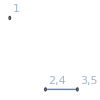
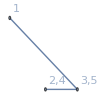
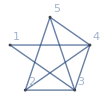
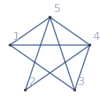
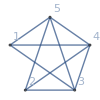
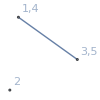
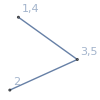
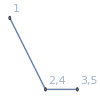
{-Graphics-448,-Graphics-7738,-Graphics-9112,-Graphics-9598,-Graphics-9841,-Graphics-11680,-Graphics-11950,-Graphics-22318,-Graphics-24922,-Graphics-25168,-Graphics-28794,-Graphics-28795,-Graphics-29272,-Graphics-29281,-Graphics-29514,-Graphics-29515,-Graphics-29523,-Graphics-29524,-Graphics-29525,-Graphics-29533,-Graphics-29560,-Graphics-29608,-Graphics-29633,-Graphics-29767,-Graphics-29797,-Graphics-30253,-Graphics-30334,-Graphics-31444,-Graphics-31492,-Graphics-31714,-Graphics-31738,-Graphics-31954,-Graphics-31984,-Graphics-33834,-Graphics-33916,-Graphics-35406,-Graphics-35434,-Graphics-36030,-Graphics-36086,-Graphics-36112,-Graphics-36138,-Graphics-36166,-Graphics-36194,-Graphics-36817,-Graphics-36898,-Graphics-38281,-Graphics-38308,-Graphics-49207,-Graphics-49210,-Graphics-51475,-Graphics-51478}

```mathematica
Table[Labeled[Graph[newAssoc[key]["graph"],ImageSize->{100,100}],key],{key,stubborn}]
```

```mathematica
suspect=Select[Keys[newAssoc],ToString[newAssoc[#]["comp"]]≠"Greater"&&
(With[{flat=Flatten[newAssoc[#]["colortable3"]]},
ContainsAny[flat,{α1,β1,γ1,δ1,ϵ1}] 
])&]
```

{7738,11950,22318,25168,29608,31444,31492,31714,31738,33916,35434,36030,36112,36138,36166}

```mathematica
ColorTablePrint666[key_]:=Block[{current=newAssoc[key],equals,cellformat, headingFormat},
cellformat=TextCell[#,CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green], CellSize->{400,Automatic},TextAlignment->Center]&;
headingFormat=Style[#,Red,FontSize->12,FontFamily->"Tahoma"]&;
Column[
{
Labeled[Graph[current["graph"],ImageSize->{60,60},EdgeStyle->Blue],{headingFormat[key],headingFormat[newAssoc[key]["colofour2"]],ToString[newAssoc[key]["comp"]]},{Left,Right,Top}],
Style[MatrixForm[Map[Map[cellformat[#]&,#]&,current["colortable3"]//Simplify],TableHeadings->{Map[headingFormat[#[[1]]<->#[[2]]]&,Subsets[Range[5],{2}]],Map[ headingFormat,{"=","≠"}]}, TableSpacing->{0, 0}],FontSize->12, FontFamily->"Tahoma"]
},
Alignment->Center
]
]
```

```mathematica
ColorTablePrint666[49207]
```

-Graphics-492071/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1) | 0
1<->3 | 0 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)
1<->4 | 0 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)
1<->5 | 0 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)
2<->3 | 0 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)
2<->4 | 0 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)
2<->5 | 0 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)
3<->4 | 0 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)
3<->5 | 0 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1)
4<->5 | 0 | 1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1))

```mathematica
Table[ColorTablePrint666[key],{key,suspect}]
```

{-Graphics-77381/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1) | γ1
1<->3 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1)
1<->4 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1) | γ1
1<->5 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1)
2<->3 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1)
2<->4 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1) | 0
2<->5 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1)
3<->4 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1)
3<->5 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1) | 0
4<->5 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1)),-Graphics-119501/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1) | ϵ1
1<->3 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1)
1<->4 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1) | 0
1<->5 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1)
2<->3 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1)
2<->4 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1) | ϵ1
2<->5 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1)
3<->4 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1)
3<->5 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1) | 0
4<->5 | 0 | 1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1)),-Graphics-223181/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
1<->3 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | γ1
1<->4 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
1<->5 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | γ1
2<->3 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
2<->4 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | 0
2<->5 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
3<->4 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
3<->5 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | 0
4<->5 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)),-Graphics-251681/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1)
1<->3 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1) | β1
1<->4 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1) | 0
1<->5 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1)
2<->3 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1)
2<->4 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1)
2<->5 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1) | 0
3<->4 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1) | β1
3<->5 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1)
4<->5 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1)),-Graphics-29608γ1GreaterEqual
( | = | ≠
1<->2 | 0 | γ1
1<->3 | 0 | γ1
1<->4 | 0 | γ1
1<->5 | 0 | γ1
2<->3 | 0 | γ1
2<->4 | γ1 | 0
2<->5 | 0 | γ1
3<->4 | 0 | γ1
3<->5 | γ1 | 0
4<->5 | 0 | γ1),-Graphics-314441/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1)
1<->3 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1)
1<->4 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1) | 0
1<->5 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1)
2<->3 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1) | ϵ1
2<->4 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1)
2<->5 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1) | ϵ1
3<->4 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1)
3<->5 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1) | 0
4<->5 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1)),-Graphics-314921/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1)
1<->3 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1)
1<->4 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1) | 0
1<->5 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1)
2<->3 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1) | β1
2<->4 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1)
2<->5 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1) | 0
3<->4 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1)
3<->5 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1) | β1
4<->5 | 0 | 1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1)),-Graphics-31714ϵ1GreaterEqual
( | = | ≠
1<->2 | 0 | ϵ1
1<->3 | 0 | ϵ1
1<->4 | ϵ1 | 0
1<->5 | 0 | ϵ1
2<->3 | 0 | ϵ1
2<->4 | 0 | ϵ1
2<->5 | 0 | ϵ1
3<->4 | 0 | ϵ1
3<->5 | ϵ1 | 0
4<->5 | 0 | ϵ1),-Graphics-31738β1GreaterEqual
( | = | ≠
1<->2 | 0 | β1
1<->3 | 0 | β1
1<->4 | β1 | 0
1<->5 | 0 | β1
2<->3 | 0 | β1
2<->4 | 0 | β1
2<->5 | β1 | 0
3<->4 | 0 | β1
3<->5 | 0 | β1
4<->5 | 0 | β1),-Graphics-339161/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1)
1<->3 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1) | 0
1<->4 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1) | δ1
1<->5 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1)
2<->3 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1)
2<->4 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1)
2<->5 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1) | 0
3<->4 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1) | δ1
3<->5 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1)
4<->5 | 0 | 1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1)),-Graphics-354341/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
1<->3 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | 0
1<->4 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
1<->5 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | α1
2<->3 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
2<->4 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | 0
2<->5 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
3<->4 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
3<->5 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | α1
4<->5 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)),-Graphics-360301/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1)
1<->3 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1) | 0
1<->4 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1)
1<->5 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1)
2<->3 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1)
2<->4 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1) | δ1
2<->5 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1) | 0
3<->4 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1)
3<->5 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1)
4<->5 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1) | δ1),-Graphics-36112δ1GreaterEqual
( | = | ≠
1<->2 | 0 | δ1
1<->3 | δ1 | 0
1<->4 | 0 | δ1
1<->5 | 0 | δ1
2<->3 | 0 | δ1
2<->4 | 0 | δ1
2<->5 | δ1 | 0
3<->4 | 0 | δ1
3<->5 | 0 | δ1
4<->5 | 0 | δ1),-Graphics-361381/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)
1<->3 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1) | 0
1<->4 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)
1<->5 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)
2<->3 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)
2<->4 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1) | 0
2<->5 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1) | α1
3<->4 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)
3<->5 | 0 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1)
4<->5 | 1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1) | α1),-Graphics-36166α1GreaterEqual
( | = | ≠
1<->2 | 0 | α1
1<->3 | α1 | 0
1<->4 | 0 | α1
1<->5 | 0 | α1
2<->3 | 0 | α1
2<->4 | α1 | 0
2<->5 | 0 | α1
3<->4 | 0 | α1
3<->5 | 0 | α1
4<->5 | 0 | α1)}

```mathematica
contracdict=Fold[And,Table[newAssoc[key]["colofour2"]==0,{key,stubborn}]];
```

```mathematica
Sort[Flatten[Table[Flatten[newAssoc[key]["colortable3"]],{key,stubborn}]]//DeleteDuplicates,Length[#1]<Length[#2]&]
```

{α1,δ1,β1,ϵ1,γ1,0,1/6 (-2 b01-2 b02+b03+4 b04+b05-b06-b07-b08+2 b09-b10-3 b11-3 b12+3 b13-3 b14+3 b15+4 b16+4 b17-2 b18-2 b19-2 b20-b21-b22-b23+5 b24-b25+b26+b27+b28-2 b29+b30+3 b36+3 b37-3 b38-3 b39-3 b40+8 α-4 α1-4 β-4 β1-4 γ+2 γ1+8 δ+2 δ1-4 ϵ+2 ϵ1),1/2 (-b01-b02+b04+b09-b11-b12+b13-b14+b15+2 b16+2 b17-b21-b22-b23+b24-b25+b26+b27-b29-b34+b36+b37-b38-b39-b40+4 α-2 α1-2 β1+4 δ-2 ϵ),1/6 (b01+4 b02+b03-2 b04-2 b05-b06+2 b07-b08-b09-b10+3 b11-3 b12+3 b13-3 b14-3 b15-2 b16-2 b17-2 b18+4 b19+4 b20-b21+5 b22-b23-b24-b25+b26-2 b27+b28+b29+b30-3 b36-3 b37-3 b38+3 b39+3 b40-4 α-4 α1-4 β+2 β1+8 γ+2 γ1-4 δ+2 δ1+8 ϵ-4 ϵ1),1/6 (b01-2 b02-2 b03+b04+4 b05-b06-b07-b08-b09+2 b10+3 b11-3 b12-3 b13+3 b14-3 b15-2 b16+4 b17+4 b18-2 b19-2 b20-b21-b22-b23-b24+5 b25+b26+b27+b28+b29-2 b30-3 b36+3 b37+3 b38-3 b39-3 b40-4 α+2 α1+8 β+2 β1-4 γ+2 γ1+8 δ-4 δ1-4 ϵ-4 ϵ1),1/2 (b01-b03-b04+b06-b11+b12-b13-b14+b15+2 b18+2 b19+b21-b22-b23-b24-b25-b26+b28+b29-b31-b36-b37+b38+b39-b40-2 α+4 β-2 β1-2 γ1+4 ϵ),1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1),1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α+8 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1),1/6 (-5 b01+b02+4 b03+b04-5 b05-b06+2 b07+2 b08+2 b09-b10+6 b13+b16-2 b17-5 b18-2 b19+b20-b21+2 b22+2 b23+2 b24-b25+b26-2 b27-2 b28-2 b29+b30+3 b36-3 b38+3 b40+2 α+2 α1-10 β+2 β1+2 γ+2 γ1-4 δ+2 δ1-4 ϵ+2 ϵ1),1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ+8 δ1-10 ϵ+8 ϵ1),1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ-4 δ1-10 ϵ-4 ϵ1),1/12 (-8 b01-2 b02+4 b03+4 b04-2 b05-4 b06+2 b07+2 b08+2 b09+2 b10+6 b11-6 b12+6 b13+6 b14-6 b15+b16+b17-5 b18-5 b19+b20-4 b21+2 b22+2 b23+2 b24+2 b25+4 b26-2 b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b38-3 b39+3 b40+2 α-4 α1-10 β+8 β1+2 γ+8 γ1+2 δ+8 δ1-10 ϵ-4 ϵ1),1/6 (-5 b01-5 b02+b03+4 b04+b05-b06-b07+2 b08+2 b09+2 b10+6 b14+b16+b17-2 b18-5 b19-2 b20-b21-b22+2 b23+2 b24+2 b25+b26+b27-2 b28-2 b29-2 b30+3 b36+3 b37-3 b39+2 α+2 α1-4 β+2 β1-4 γ+2 γ1+2 δ+2 δ1-10 ϵ+2 ϵ1),1/2 (-b01+b03-b05+b08-b11+b12-b13+b14-b15+2 b16+2 b20-b21-b22+b23-b24-b25+b26-b28+b30-b33+b36-b37-b38-b39+b40+4 α-2 β+4 γ-2 γ1-2 δ1),1/2 (-b02-b03+b05+b10+b11-b12-b13+b14-b15+2 b17+2 b18-b21-b22-b23-b24+b25+b27+b28-b30-b35-b36+b37+b38-b39-b40+4 β-2 γ+4 δ-2 δ1-2 ϵ1),1/6 (-2 b01+b02+4 b03+b04-2 b05-b06-b07+2 b08-b09-b10-3 b11+3 b12-3 b13+3 b14-3 b15+4 b16-2 b17-2 b18-2 b19+4 b20-b21-b22+5 b23-b24-b25+b26+b27-2 b28+b29+b30+3 b36-3 b37-3 b38-3 b39+3 b40+8 α+2 α1-4 β+2 β1+8 γ-4 γ1-4 δ-4 δ1-4 ϵ+2 ϵ1),1/6 (4 b01+b02-2 b03-2 b04+b05+2 b06-b07-b08-b09-b10-3 b11+3 b12-3 b13-3 b14+3 b15-2 b16-2 b17+4 b18+4 b19-2 b20+5 b21-b22-b23-b24-b25-2 b26+b27+b28+b29+b30-3 b36-3 b37+3 b38+3 b39-3 b40-4 α+2 α1+8 β-4 β1-4 γ-4 γ1-4 δ+2 δ1+8 ϵ+2 ϵ1),1/2 (b02-b04-b05+b07+b11-b12+b13-b14-b15+2 b19+2 b20-b21+b22-b23-b24-b25-b27+b29+b30-b32-b36-b37-b38+b39+b40-2 α1+4 γ-2 δ+4 ϵ-2 ϵ1),1/2 (-2 b02+2 b04+2 b05-2 b07-b11+b12-b13+b14+b15+2 b17-4 b19-4 b20+b21-3 b22+b23+3 b24+3 b25+2 b27-2 b29-2 b30+2 b32+3 b36+3 b37+3 b38-3 b39-3 b40+4 α1+2 β1-10 γ+2 γ1+4 δ+2 δ1-10 ϵ+4 ϵ1),1/2 (-2 b01+2 b03+2 b04-2 b06+b11-b12+b13+b14-b15+2 b16-4 b18-4 b19-3 b21+b22+3 b23+3 b24+b25+2 b26-2 b28-2 b29+2 b31+3 b36+3 b37-3 b38-3 b39+3 b40+4 α+2 α1-10 β+4 β1+4 γ1+2 δ1-10 ϵ+2 ϵ1),1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β+8 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1),1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β+8 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1),1/12 (-2 b01-8 b02-2 b03+4 b04+4 b05+2 b06-4 b07+2 b08+2 b09+2 b10-6 b11+6 b12-6 b13+6 b14+6 b15+b16+b17+b18-5 b19-5 b20+2 b21-4 b22+2 b23+2 b24+2 b25-2 b26+4 b27-2 b28-2 b29-2 b30+3 b36+3 b37+3 b38-3 b39-3 b40+2 α+8 α1+2 β-4 β1-10 γ-4 γ1+2 δ-4 δ1-10 ϵ+8 ϵ1),1/6 (b01-5 b02-5 b03+b04+4 b05+2 b06-b07-b08+2 b09+2 b10+6 b15-2 b16+b17+b18-2 b19-5 b20+2 b21-b22-b23+2 b24+2 b25-2 b26+b27+b28-2 b29-2 b30+3 b37+3 b38-3 b40-4 α+2 α1+2 β+2 β1-10 γ+2 γ1+2 δ+2 δ1-4 ϵ+2 ϵ1),1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ+8 ϵ1),1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ-4 ϵ1),1/6 (4 b01+b02-5 b03-5 b04+b05+2 b06+2 b07-b08-b09+2 b10+6 b11-5 b16-2 b17+b18+b19-2 b20+2 b21+2 b22-b23-b24+2 b25-2 b26-2 b27+b28+b29-2 b30-3 b36+3 b38+3 b39-10 α+2 α1+2 β+2 β1-4 γ+2 γ1-4 δ+2 δ1+2 ϵ+2 ϵ1),1/12 (4 b01-2 b02-8 b03-2 b04+4 b05+2 b06+2 b07-4 b08+2 b09+2 b10+6 b11-6 b12+6 b13-6 b14+6 b15-5 b16+b17+b18+b19-5 b20+2 b21+2 b22-4 b23+2 b24+2 b25-2 b26-2 b27+4 b28-2 b29-2 b30-3 b36+3 b37+3 b38+3 b39-3 b40-10 α-4 α1+2 β-4 β1-10 γ+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1),1/2 (2 b01-2 b03+2 b05-2 b08+b11-b12+b13-b14+b15-4 b16+2 b18-4 b20+3 b21+b22-3 b23+b24+3 b25-2 b26+2 b28-2 b30+2 b33-3 b36+3 b37+3 b38+3 b39-3 b40-10 α+2 α1+4 β+2 β1-10 γ+4 γ1+4 δ1+2 ϵ1),1/2 (2 b02+2 b03-2 b05-2 b10-b11+b12+b13-b14+b15-4 b17-4 b18+2 b20+b21+3 b22+3 b23+b24-3 b25-2 b27-2 b28+2 b30+2 b35+3 b36-3 b37-3 b38+3 b39+3 b40+2 α1-10 β+2 β1+4 γ+2 γ1-10 δ+4 δ1+4 ϵ1),1/2 (2 b01+2 b02-2 b04-2 b09+b11+b12-b13+b14-b15-4 b16-4 b17+2 b19+3 b21+3 b22+b23-3 b24+b25-2 b26-2 b27+2 b29+2 b34-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+4 α1+4 β1+2 γ1-10 δ+2 δ1+4 ϵ+2 ϵ1),1/6 (b01+4 b02+b03-5 b04-5 b05+2 b06+2 b07+2 b08-b09-b10+6 b12-2 b16-5 b17-2 b18+b19+b20+2 b21+2 b22+2 b23-b24-b25-2 b26-2 b27-2 b28+b29+b30-3 b37+3 b39+3 b40-4 α+2 α1-4 β+2 β1+2 γ+2 γ1-10 δ+2 δ1+2 ϵ+2 ϵ1),1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ+8 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1),1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1),1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ+8 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1),1/12 (4 b01+4 b02-2 b03-8 b04-2 b05+2 b06+2 b07+2 b08-4 b09+2 b10+6 b11+6 b12-6 b13+6 b14-6 b15-5 b16-5 b17+b18+b19+b20+2 b21+2 b22+2 b23-4 b24+2 b25-2 b26-2 b27-2 b28+4 b29-2 b30-3 b36-3 b37+3 b38+3 b39+3 b40-10 α+8 α1+2 β+8 β1+2 γ-4 γ1-10 δ-4 δ1+2 ϵ-4 ϵ1),-b01-b02+b03+2 b04+b05-b06-b07+b14+b16+b17-2 b18-4 b19-2 b20-b21-b22+2 b23+3 b24+2 b25+b26+b27-b28-2 b29-b30+b31+b32+3 b36+3 b37-3 b39+2 α+3 α1-5 β+3 β1-5 γ+3 γ1+2 δ+2 δ1-10 ϵ+3 ϵ1,b01-b02-b03+b04+2 b05-b07-b08+b15-2 b16+b17+b18-2 b19-4 b20+2 b21-b22-b23+2 b24+3 b25-b26+b27+b28-b29-2 b30+b32+b33+3 b37+3 b38-3 b40-5 α+3 α1+2 β+2 β1-10 γ+3 γ1+2 δ+3 δ1-5 ϵ+3 ϵ1,-b01+b02+2 b03+b04-b05-b06-b10+b13+b16-2 b17-4 b18-2 b19+b20-b21+2 b22+3 b23+2 b24-b25+b26-b27-2 b28-b29+b30+b31+b35+3 b36-3 b38+3 b40+2 α+2 α1-10 β+3 β1+2 γ+3 γ1-5 δ+3 δ1-5 ϵ+3 ϵ1,2 b01+b02-b03-b04+b05-b08-b09+b11-4 b16-2 b17+b18+b19-2 b20+3 b21+2 b22-b23-b24+2 b25-2 b26-b27+b28+b29-b30+b33+b34-3 b36+3 b38+3 b39-10 α+3 α1+2 β+3 β1-5 γ+3 γ1-5 δ+3 δ1+2 ϵ+2 ϵ1,b01+2 b02+b03-b04-b05-b09-b10+b12-2 b16-4 b17-2 b18+b19+b20+2 b21+3 b22+2 b23-b24-b25-b26-2 b27-b28+b29+b30+b34+b35-3 b37+3 b39+3 b40-5 α+3 α1-5 β+3 β1+2 γ+2 γ1-10 δ+3 δ1+2 ϵ+3 ϵ1}

```mathematica
ColorTablePrint[35434]
```

-Graphics-354341/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)GreaterEqual
( | = | ≠
1<->2 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
1<->3 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | 0
1<->4 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
1<->5 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | α1
2<->3 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
2<->4 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | 0
2<->5 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
3<->4 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1)
3<->5 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α-4 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1) | α1
4<->5 | 0 | 1/12 (-2 b01+4 b02+4 b03-2 b04-8 b05+2 b06+2 b07+2 b08+2 b09-4 b10-6 b11+6 b12+6 b13-6 b14+6 b15+b16-5 b17-5 b18+b19+b20+2 b21+2 b22+2 b23+2 b24-4 b25-2 b26-2 b27-2 b28-2 b29+4 b30+3 b36-3 b37-3 b38+3 b39+3 b40+2 α+8 α1-10 β-4 β1+2 γ-4 γ1-10 δ+8 δ1+2 ϵ+8 ϵ1))

```mathematica
ineqscontradict=Simplify[ineqs5&&contracdict];
```

```mathematica
Length[ineqs5]
```

1648

```mathematica
ExpressionToTable[ineqscontradict]
```

b01>0
b02>0
b03>0
b04>0
b05>0
b06>0
b07>0
b08>0
b09>0
b10>0
b11>0
b12>0
b13>0
b14>0
b15>0
b16>0
b17>0
b18>0
b19>0
b20>0
b21>0
b22>0
b23>0
b24>0
b25>0
b26>0
b27>0
b28>0
b29>0
b30>0
b31>0
b32>0
b33>0
b34>0
b35>0
b36>0
b37>0
b38>0
b39>0
b40>0
z>0
α>0
α1==0
β>0
β1==0
γ>0
γ1==0
δ>0
δ1==0
ϵ>0
ϵ1==0
b13<b01
b14<b01
b16<b01
b14<b02
b15<b02
b17<b02
b11<b03
b15<b03
b18<b03
b11<b04
b12<b04
b19<b04
b12<b05
b13<b05
b20<b05
b16<b06
b22<b06
b25<b06
b17<b07
b21<b07
b23<b07
b18<b08
b22<b08
b24<b08
b19<b09
b23<b09
b25<b09
b20<b10
b21<b10
b24<b10
b36<b31
b37<b32
b38<b33
b39<b34
b40<b35
b01<z
b02<z
b03<z
b04<z
b05<z
b06<z
b07<z
b08<z
b09<z
b10<z
b07+b27<b01+b03
b03+b27<b01+b07
b01+b27<b03+b07
b10+b30<b01+b04
b04+b30<b01+b10
b01+b30<b04+b10
b09+b31<b01+b08
b08+b31<b01+b09
b01+b31<b08+b09
b08+b28<b02+b04
b04+b28<b02+b08
b02+b28<b04+b08
b06+b26<b02+b05
b05+b26<b02+b06
b02+b26<b05+b06
b10+b32<b02+b09
b09+b32<b02+b10
b02+b32<b09+b10
b09+b29<b03+b05
b05+b29<b03+b09
b03+b29<b05+b09
b10+b33<b03+b06
b06+b33<b03+b10
b03+b33<b06+b10
b07+b34<b04+b06
b06+b34<b04+b07
b04+b34<b06+b07
b08+b35<b05+b07
b07+b35<b05+b08
b05+b35<b07+b08
b25+b36<b16+b22
b22+b36<b16+b25
b16+b36<b22+b25
b23+b37<b17+b21
b21+b37<b17+b23
b17+b37<b21+b23
b24+b38<b18+b22
b22+b38<b18+b24
b18+b38<b22+b24
b25+b39<b19+b23
b23+b39<b19+b25
b19+b39<b23+b25
b24+b40<b20+b21
b21+b40<b20+b24
b20+b40<b21+b24
b01+b02<b14+z
b01+b05<b13+z
b01+b06<b16+z
b02+b03<b15+z
b02+b07<b17+z
b03+b04<b11+z
b03+b08<b18+z
b04+b05<b12+z
b04+b09<b19+z
b05+b10<b20+z
b06+b08<b22+z
b06+b09<b25+z
b07+b09<b23+z
b07+b10<b21+z
b08+b10<b24+z
α+γ<b38+α1
α+δ<b39+δ1
β+δ<b40+β1
β+ϵ<b36+ϵ1
γ+ϵ<b37+γ1
b16+b22+b25<2 b06+b36
b17+b21+b23<2 b07+b37
b18+b22+b24<2 b08+b38
b19+b23+b25<2 b09+b39
b20+b21+b24<2 b10+b40
b01+b03+b07<b27+2 z
b01+b04+b10<b30+2 z
b01+b08+b09<b31+2 z
b02+b04+b08<b28+2 z
b02+b05+b06<b26+2 z
b02+b09+b10<b32+2 z
b03+b05+b09<b29+2 z
b03+b06+b10<b33+2 z
b04+b06+b07<b34+2 z
b05+b07+b08<b35+2 z
b01+b22+b25+b36<b08+b09+b16+b31
b08+b16+b25+b36<b01+b09+b22+b31
b09+b16+b22+b36<b01+b08+b25+b31
b01+b22+b25+b31<b08+b09+b16+b36
b08+b16+b25+b31<b01+b09+b22+b36
b09+b16+b22+b31<b01+b08+b25+b36
b02+b21+b23+b37<b09+b10+b17+b32
b10+b17+b23+b37<b02+b09+b21+b32
b09+b17+b21+b37<b02+b10+b23+b32
b02+b21+b23+b32<b09+b10+b17+b37
b10+b17+b23+b32<b02+b09+b21+b37
b09+b17+b21+b32<b02+b10+b23+b37
b03+b22+b24+b38<b06+b10+b18+b33
b06+b18+b24+b38<b03+b10+b22+b33
b10+b18+b22+b38<b03+b06+b24+b33
b03+b22+b24+b33<b06+b10+b18+b38
b06+b18+b24+b33<b03+b10+b22+b38
b10+b18+b22+b33<b03+b06+b24+b38
b04+b23+b25+b39<b06+b07+b19+b34
b07+b19+b25+b39<b04+b06+b23+b34
b06+b19+b23+b39<b04+b07+b25+b34
b04+b23+b25+b34<b06+b07+b19+b39
b07+b19+b25+b34<b04+b06+b23+b39
b06+b19+b23+b34<b04+b07+b25+b39
b05+b21+b24+b40<b07+b08+b20+b35
b07+b20+b24+b40<b05+b08+b21+b35
b08+b20+b21+b40<b05+b07+b24+b35
b05+b21+b24+b35<b07+b08+b20+b40
b07+b20+b24+b35<b05+b08+b21+b40
b08+b20+b21+b35<b05+b07+b24+b40
b01+2 b06+b08+b09+b36<b16+b22+b25+b31+2 z
b02+2 b07+b09+b10+b37<b17+b21+b23+b32+2 z
b03+b06+2 b08+b10+b38<b18+b22+b24+b33+2 z
b04+b06+b07+2 b09+b39<b19+b23+b25+b34+2 z
b05+b07+b08+2 b10+b40<b20+b21+b24+b35+2 z
b12+b16+b18+2 α+2 β+2 δ<b11+b13+b22+b39+b40+2 β1+2 γ1+2 δ1
b11+b17+b20+2 α+2 γ+2 δ<b12+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1
b15+b16+b19+2 α+2 γ+2 ϵ<b11+b14+b25+b37+b38+2 α1+2 β1+2 γ1
b14+b18+b20+2 β+2 γ+2 ϵ<b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1
b13+b17+b19+2 β+2 δ+2 ϵ<b12+b14+b23+b36+b40+2 α1+2 β1+2 ϵ1
b11+b13+b22+b39+b40+2 β1+2 γ1+2 δ1<b12+b16+b18+b27+2 α+2 β+2 δ
b12+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1<b11+b17+b20+b26+2 α+2 γ+2 δ
b11+b14+b25+b37+b38+2 α1+2 β1+2 γ1<b15+b16+b19+b30+2 α+2 γ+2 ϵ
b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1<b14+b18+b20+b29+2 β+2 γ+2 ϵ
b12+b14+b23+b36+b40+2 α1+2 β1+2 ϵ1<b13+b17+b19+b28+2 β+2 δ+2 ϵ
b16+b17+b18+b37+b38+2 β+2 δ+2 ϵ<b19+b20+2 b22+3 b36+b39+b40+2 α+2 γ
b16+b19+b20+b39+b40+2 β+2 γ+2 ϵ<b17+b18+2 b25+3 b36+b37+b38+2 α+2 δ
b16+b17+b18+b36+b37+b38+2 α+2 β+2 δ<b19+b20+2 b22+b39+b40+2 γ+2 ϵ
b17+b18+b19+b37+b38+2 α+2 β+2 δ<b16+b20+2 b23+b36+3 b39+b40+2 γ+2 ϵ
b16+b17+b20+b36+b40+2 α+2 γ+2 ϵ<b18+b19+2 b21+3 b37+b38+b39+2 β+2 δ
b16+b17+b20+b36+b37+b40+2 α+2 γ+2 δ<b18+b19+2 b21+b38+b39+2 β+2 ϵ
b16+b17+b18+b36+b37+2 α+2 γ+2 δ<b19+b20+2 b22+3 b38+b39+b40+2 β+2 ϵ
b16+b19+b20+b36+b40+2 α+2 γ+2 δ<b17+b18+2 b25+b37+b38+3 b39+2 β+2 ϵ
b18+b19+b20+b39+b40+2 α+2 γ+2 ϵ<b16+b17+2 b24+b36+b37+3 b38+2 β+2 δ
b16+b19+b20+b36+b39+b40+2 α+2 γ+2 ϵ<b17+b18+2 b25+b37+b38+2 β+2 δ
b17+b18+b19+b38+b39+2 β+2 γ+2 ϵ<b16+b20+2 b23+b36+3 b37+b40+2 α+2 δ
b18+b19+b20+b38+b39+b40+2 β+2 γ+2 ϵ<b16+b17+2 b24+b36+b37+2 α+2 δ
b16+b17+b20+b36+b37+2 α+2 β+2 δ<b18+b19+2 b21+b38+b39+3 b40+2 γ+2 ϵ
b17+b18+b19+b37+b38+b39+2 β+2 δ+2 ϵ<b16+b20+2 b23+b36+b40+2 α+2 γ
b18+b19+b20+b38+b39+2 β+2 δ+2 ϵ<b16+b17+2 b24+b36+b37+3 b40+2 α+2 γ
b11+b13+b17+b22+b39+b40+2 β1+2 γ1+2 δ1<b12+b14+b15+b16+b18+2 α+2 β+2 δ
b11+b13+b15+b22+b39+b40+2 β1+2 γ1+2 δ1<b12+b14+b16+b17+b18+2 α+2 β+2 δ
b11+b13+b14+b22+b39+b40+2 β1+2 γ1+2 δ1<b12+b15+b16+b17+b18+2 α+2 β+2 δ
b12+b16+b17+b18+2 α+2 β+2 δ<b11+b13+b14+b15+b22+b39+b40+2 β1+2 γ1+2 δ1
b12+b15+b16+b18+2 α+2 β+2 δ<b11+b13+b14+b17+b22+b39+b40+2 β1+2 γ1+2 δ1
b12+b14+b16+b18+2 α+2 β+2 δ<b11+b13+b15+b17+b22+b39+b40+2 β1+2 γ1+2 δ1
b12+b15+b16+b21+b38+b39+2 α1+2 δ1+2 ϵ1<b11+b13+b14+b17+b20+2 α+2 γ+2 δ
b12+b14+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1<b11+b13+b16+b17+b20+2 α+2 γ+2 δ
b12+b13+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1<b11+b14+b16+b17+b20+2 α+2 γ+2 δ
b11+b16+b17+b20+2 α+2 γ+2 δ<b12+b13+b14+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1
b11+b14+b17+b20+2 α+2 γ+2 δ<b12+b13+b15+b16+b21+b38+b39+2 α1+2 δ1+2 ϵ1
b11+b13+b17+b20+2 α+2 γ+2 δ<b12+b14+b15+b16+b21+b38+b39+2 α1+2 δ1+2 ϵ1
b15+b16+b19+b20+2 α+2 γ+2 ϵ<b11+b12+b13+b14+b25+b37+b38+2 α1+2 β1+2 γ1
b13+b15+b16+b19+2 α+2 γ+2 ϵ<b11+b12+b14+b20+b25+b37+b38+2 α1+2 β1+2 γ1
b12+b15+b16+b19+2 α+2 γ+2 ϵ<b11+b13+b14+b20+b25+b37+b38+2 α1+2 β1+2 γ1
b11+b14+b20+b25+b37+b38+2 α1+2 β1+2 γ1<b12+b13+b15+b16+b19+2 α+2 γ+2 ϵ
b11+b13+b14+b25+b37+b38+2 α1+2 β1+2 γ1<b12+b15+b16+b19+b20+2 α+2 γ+2 ϵ
b11+b12+b14+b25+b37+b38+2 α1+2 β1+2 γ1<b13+b15+b16+b19+b20+2 α+2 γ+2 ϵ
b13+b15+b19+b24+b36+b37+2 γ1+2 δ1+2 ϵ1<b11+b12+b14+b18+b20+2 β+2 γ+2 ϵ
b12+b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1<b11+b14+b18+b19+b20+2 β+2 γ+2 ϵ
b11+b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1<b12+b14+b18+b19+b20+2 β+2 γ+2 ϵ
b14+b18+b19+b20+2 β+2 γ+2 ϵ<b11+b12+b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1
b12+b14+b18+b20+2 β+2 γ+2 ϵ<b11+b13+b15+b19+b24+b36+b37+2 γ1+2 δ1+2 ϵ1
b11+b14+b18+b20+2 β+2 γ+2 ϵ<b12+b13+b15+b19+b24+b36+b37+2 γ1+2 δ1+2 ϵ1
b12+b14+b18+b23+b36+b40+2 α1+2 β1+2 ϵ1<b11+b13+b15+b17+b19+2 β+2 δ+2 ϵ
b12+b14+b15+b23+b36+b40+2 α1+2 β1+2 ϵ1<b11+b13+b17+b18+b19+2 β+2 δ+2 ϵ
b11+b12+b14+b23+b36+b40+2 α1+2 β1+2 ϵ1<b13+b15+b17+b18+b19+2 β+2 δ+2 ϵ
b13+b17+b18+b19+2 β+2 δ+2 ϵ<b11+b12+b14+b15+b23+b36+b40+2 α1+2 β1+2 ϵ1
b13+b15+b17+b19+2 β+2 δ+2 ϵ<b11+b12+b14+b18+b23+b36+b40+2 α1+2 β1+2 ϵ1
b11+b13+b17+b19+2 β+2 δ+2 ϵ<b12+b14+b15+b18+b23+b36+b40+2 α1+2 β1+2 ϵ1
b18+2 b21+2 b25+b38+2 β+2 δ+2 ϵ<b16+b17+b19+b20+2 b23+b36+b37+b39+b40+2 α+2 γ
b19+2 b21+2 b22+b39+2 β+2 γ+2 ϵ<b16+b17+b18+b20+2 b24+b36+b37+b38+b40+2 α+2 δ
b12+b14+b15+b16+b17+b18+2 α+2 β+2 δ<2 b02+b11+b13+b22+b39+b40+2 β1+2 γ1+2 δ1
b19+2 b21+2 b22+b39+3 b40+2 γ+2 ϵ<b16+b17+b18+b20+2 b24+b36+b37+b38+2 α+2 β+2 δ
b20+2 b22+2 b23+3 b39+b40+2 γ+2 ϵ<b16+b17+b18+b19+2 b25+b36+b37+b38+2 α+2 β+2 δ
b20+2 b22+2 b23+b40+2 α+2 γ+2 ϵ<b16+b17+b18+b19+2 b25+b36+b37+b38+b39+2 β+2 δ
b19+2 b21+2 b22+3 b38+b39+2 β+2 ϵ<b16+b17+b18+b20+2 b24+b36+b37+b40+2 α+2 γ+2 δ
b18+2 b21+2 b25+b38+3 b39+2 β+2 ϵ<b16+b17+b19+b20+2 b23+b36+b37+b40+2 α+2 γ+2 δ
b11+b13+b14+b16+b17+b20+2 α+2 γ+2 δ<2 b01+b12+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1
b16+2 b23+2 b24+b36+2 α+2 γ+2 δ<b17+b18+b19+b20+2 b21+b37+b38+b39+b40+2 β+2 ϵ
b12+b13+b15+b16+b19+b20+2 α+2 γ+2 ϵ<2 b05+b11+b14+b25+b37+b38+2 α1+2 β1+2 γ1
b18+2 b21+2 b25+3 b37+b38+2 β+2 δ<b16+b17+b19+b20+2 b23+b36+b39+b40+2 α+2 γ+2 ϵ
b17+2 b24+2 b25+b37+3 b38+2 β+2 δ<b16+b18+b19+b20+2 b22+b36+b39+b40+2 α+2 γ+2 ϵ
b16+2 b23+2 b24+b36+3 b37+2 α+2 δ<b17+b18+b19+b20+2 b21+b38+b39+b40+2 β+2 γ+2 ϵ
b17+2 b24+2 b25+3 b36+b37+2 α+2 δ<b16+b18+b19+b20+2 b22+b38+b39+b40+2 β+2 γ+2 ϵ
b11+b12+b14+b18+b19+b20+2 β+2 γ+2 ϵ<2 b04+b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1
b17+2 b24+2 b25+b37+2 α+2 β+2 δ<b16+b18+b19+b20+2 b22+b36+b38+b39+b40+2 γ+2 ϵ
b16+2 b23+2 b24+b36+3 b40+2 α+2 γ<b17+b18+b19+b20+2 b21+b37+b38+b39+2 β+2 δ+2 ϵ
b20+2 b22+2 b23+3 b36+b40+2 α+2 γ<b16+b17+b18+b19+2 b25+b37+b38+b39+2 β+2 δ+2 ϵ
b11+b13+b15+b17+b18+b19+2 β+2 δ+2 ϵ<2 b03+b12+b14+b23+b36+b40+2 α1+2 β1+2 ϵ1
b01+b11+b13+b15+b17+b22+b39+b40+2 β1+2 γ1+2 δ1<b03+b07+b12+b14+b16+b18+b27+2 α+2 β+2 δ
b03+b11+b13+b14+b17+b22+b39+b40+2 β1+2 γ1+2 δ1<b01+b07+b12+b15+b16+b18+b27+2 α+2 β+2 δ
b07+b11+b13+b14+b15+b22+b39+b40+2 β1+2 γ1+2 δ1<b01+b03+b12+b16+b17+b18+b27+2 α+2 β+2 δ
b01+b12+b15+b16+b17+b18+b27+2 α+2 β+2 δ<b03+b07+b11+b13+b14+b22+b39+b40+2 β1+2 γ1+2 δ1
b03+b12+b14+b16+b17+b18+b27+2 α+2 β+2 δ<b01+b07+b11+b13+b15+b22+b39+b40+2 β1+2 γ1+2 δ1
b07+b12+b14+b15+b16+b18+b27+2 α+2 β+2 δ<b01+b03+b11+b13+b17+b22+b39+b40+2 β1+2 γ1+2 δ1
b05+b12+b14+b15+b16+b21+b38+b39+2 α1+2 δ1+2 ϵ1<b02+b06+b11+b13+b17+b20+b26+2 α+2 γ+2 δ
b02+b12+b13+b15+b16+b21+b38+b39+2 α1+2 δ1+2 ϵ1<b05+b06+b11+b14+b17+b20+b26+2 α+2 γ+2 δ
b06+b12+b13+b14+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1<b02+b05+b11+b16+b17+b20+b26+2 α+2 γ+2 δ
b05+b11+b14+b16+b17+b20+b26+2 α+2 γ+2 δ<b02+b06+b12+b13+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1
b02+b11+b13+b16+b17+b20+b26+2 α+2 γ+2 δ<b05+b06+b12+b14+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1
b06+b11+b13+b14+b17+b20+b26+2 α+2 γ+2 δ<b02+b05+b12+b15+b16+b21+b38+b39+2 α1+2 δ1+2 ϵ1
b04+b13+b15+b16+b19+b20+b30+2 α+2 γ+2 ϵ<b01+b10+b11+b12+b14+b25+b37+b38+2 α1+2 β1+2 γ1
b01+b12+b15+b16+b19+b20+b30+2 α+2 γ+2 ϵ<b04+b10+b11+b13+b14+b25+b37+b38+2 α1+2 β1+2 γ1
b10+b12+b13+b15+b16+b19+b30+2 α+2 γ+2 ϵ<b01+b04+b11+b14+b20+b25+b37+b38+2 α1+2 β1+2 γ1
b04+b11+b13+b14+b20+b25+b37+b38+2 α1+2 β1+2 γ1<b01+b10+b12+b15+b16+b19+b30+2 α+2 γ+2 ϵ
b01+b11+b12+b14+b20+b25+b37+b38+2 α1+2 β1+2 γ1<b04+b10+b13+b15+b16+b19+b30+2 α+2 γ+2 ϵ
b10+b11+b12+b13+b14+b25+b37+b38+2 α1+2 β1+2 γ1<b01+b04+b15+b16+b19+b20+b30+2 α+2 γ+2 ϵ
b03+b12+b13+b15+b19+b24+b36+b37+2 γ1+2 δ1+2 ϵ1<b05+b09+b11+b14+b18+b20+b29+2 β+2 γ+2 ϵ
b05+b11+b13+b15+b19+b24+b36+b37+2 γ1+2 δ1+2 ϵ1<b03+b09+b12+b14+b18+b20+b29+2 β+2 γ+2 ϵ
b09+b11+b12+b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1<b03+b05+b14+b18+b19+b20+b29+2 β+2 γ+2 ϵ
b03+b12+b14+b18+b19+b20+b29+2 β+2 γ+2 ϵ<b05+b09+b11+b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1
b05+b11+b14+b18+b19+b20+b29+2 β+2 γ+2 ϵ<b03+b09+b12+b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1
b09+b11+b12+b14+b18+b20+b29+2 β+2 γ+2 ϵ<b03+b05+b13+b15+b19+b24+b36+b37+2 γ1+2 δ1+2 ϵ1
b04+b12+b14+b15+b18+b23+b36+b40+2 α1+2 β1+2 ϵ1<b02+b08+b11+b13+b17+b19+b28+2 β+2 δ+2 ϵ
b02+b11+b12+b14+b18+b23+b36+b40+2 α1+2 β1+2 ϵ1<b04+b08+b13+b15+b17+b19+b28+2 β+2 δ+2 ϵ
b08+b11+b12+b14+b15+b23+b36+b40+2 α1+2 β1+2 ϵ1<b02+b04+b13+b17+b18+b19+b28+2 β+2 δ+2 ϵ
b04+b13+b15+b17+b18+b19+b28+2 β+2 δ+2 ϵ<b02+b08+b11+b12+b14+b23+b36+b40+2 α1+2 β1+2 ϵ1
b02+b11+b13+b17+b18+b19+b28+2 β+2 δ+2 ϵ<b04+b08+b12+b14+b15+b23+b36+b40+2 α1+2 β1+2 ϵ1
b08+b11+b13+b15+b17+b19+b28+2 β+2 δ+2 ϵ<b02+b04+b12+b14+b18+b23+b36+b40+2 α1+2 β1+2 ϵ1
b01+b05+2 b18+2 b21+2 b25+b28+b33+2 b37+2 b38+4 β+2 δ<b03+b08+2 b16+2 b20+2 b23+b26+b30+2 b36+2 b40+4 α+4 γ
b03+b04+2 b16+2 b23+2 b24+b26+b31+2 b36+2 b40+4 α+2 γ<b01+b06+2 b18+2 b19+2 b21+b28+b29+2 b38+2 b39+4 β+4 ϵ
b01+b05+2 b18+2 b21+2 b25+b28+b33+2 b38+2 b39+4 β+2 ϵ<b03+b08+2 b16+2 b20+2 b23+b26+b30+2 b36+2 b40+4 α+4 γ
b01+b02+2 b19+2 b21+2 b22+b29+b34+2 b38+2 b39+2 β+4 ϵ<b04+b09+2 b16+2 b17+2 b24+b26+b27+2 b36+2 b37+4 α+4 δ
b03+b04+2 b16+2 b23+2 b24+b26+b31+2 b36+2 b37+4 α+2 δ<b01+b06+2 b18+2 b19+2 b21+b28+b29+2 b38+2 b39+4 β+4 ϵ
b01+b02+2 b19+2 b21+2 b22+b29+b34+2 b39+2 b40+2 γ+4 ϵ<b04+b09+2 b16+2 b17+2 b24+b26+b27+2 b36+2 b37+4 α+4 δ
b04+b05+2 b17+2 b24+2 b25+b27+b32+2 b36+2 b37+2 α+4 δ<b02+b07+2 b19+2 b20+2 b22+b29+b30+2 b39+2 b40+4 γ+4 ϵ
b02+b03+2 b20+2 b22+2 b23+b30+b35+2 b36+2 b40+2 α+4 γ<b05+b10+2 b17+2 b18+2 b25+b27+b28+2 b37+2 b38+4 β+4 δ
b02+b03+2 b20+2 b22+2 b23+b30+b35+2 b39+2 b40+4 γ+2 ϵ<b05+b10+2 b17+2 b18+2 b25+b27+b28+2 b37+2 b38+4 β+4 δ
b04+b05+2 b17+2 b24+2 b25+b27+b32+2 b37+2 b38+2 β+4 δ<b02+b07+2 b19+2 b20+2 b22+b29+b30+2 b39+2 b40+4 γ+4 ϵ
2 b05+b17+b18+2 b21+2 b24+2 b25+b37+b38+b40+2 β+2 δ<2 b07+2 b08+b16+b19+3 b20+2 b35+b36+b39+2 α+2 γ+2 ϵ
b01+b02+2 b21+2 b22+b33+b35+2 b39+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b08+b10+2 b16+2 b17+b26+b27+4 α+2 β+2 γ+4 δ
2 b01+b18+b19+2 b21+2 b22+2 b25+b36+b38+b39+2 β+2 ϵ<2 b08+2 b09+3 b16+b17+b20+2 b31+b37+b40+2 α+2 γ+2 δ
b04+b05+2 b24+2 b25+b31+b33+2 b37+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b06+b08+2 b19+2 b20+b29+b30+2 α+2 β+4 γ+4 ϵ
2 b04+b16+b17+2 b23+2 b24+2 b25+b36+b37+b39+2 α+2 δ<2 b06+2 b07+b18+3 b19+b20+2 b34+b38+b40+2 β+2 γ+2 ϵ
2 b02+b19+b20+2 b21+2 b22+2 b23+b37+b39+b40+2 γ+2 ϵ<2 b09+2 b10+b16+3 b17+b18+2 b32+b36+b38+2 α+2 β+2 δ
b02+b03+2 b22+2 b23+b31+b34+2 b40+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b06+b09+2 b17+2 b18+b27+b28+2 α+4 β+4 δ+2 ϵ
2 b03+b16+b20+2 b22+2 b23+2 b24+b36+b38+b40+2 α+2 γ<2 b06+2 b10+b17+3 b18+b19+2 b33+b37+b39+2 β+2 δ+2 ϵ
b01+b05+2 b21+2 b25+b32+b34+2 b38+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b07+b09+2 b16+2 b20+b26+b30+4 α+4 γ+2 δ+2 ϵ
b03+b04+2 b23+2 b24+b32+b35+2 b36+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b07+b10+2 b18+2 b19+b28+b29+4 β+2 γ+2 δ+4 ϵ
b01+2 b02+b03+b07+b11+b13+b22+b39+b40+2 β1+2 γ1+2 δ1<b12+b14+b15+b16+b17+b18+b27+2 z+2 α+2 β+2 δ
b11+b13+2 b17+b24+b25+b37+2 α+2 β+4 δ<b12+b14+b15+b21+b22+b23+b36+b38+b39+b40+2 α1+2 β1+2 δ1+2 ϵ1
2 b01+b02+b05+b06+b12+b15+b21+b38+b39+2 α1+2 δ1+2 ϵ1<b11+b13+b14+b16+b17+b20+b26+2 z+2 α+2 γ+2 δ
b12+b15+2 b16+b23+b24+b36+4 α+2 γ+2 δ<b11+b13+b14+b21+b22+b25+b37+b38+b39+b40+2 α1+2 β1+2 γ1+2 δ1
b01+b04+2 b05+b10+b11+b14+b25+b37+b38+2 α1+2 β1+2 γ1<b12+b13+b15+b16+b19+b20+b30+2 z+2 α+2 γ+2 ϵ
b11+b14+2 b20+b22+b23+b40+2 α+4 γ+2 ϵ<b12+b13+b15+b21+b24+b25+b36+b37+b38+b39+2 α1+2 γ1+2 δ1+2 ϵ1
b03+2 b04+b05+b09+b13+b15+b24+b36+b37+2 γ1+2 δ1+2 ϵ1<b11+b12+b14+b18+b19+b20+b29+2 z+2 β+2 γ+2 ϵ
b13+b15+2 b19+b21+b22+b39+2 β+2 γ+4 ϵ<b11+b12+b14+b23+b24+b25+b36+b37+b38+b40+2 α1+2 β1+2 γ1+2 ϵ1
b02+2 b03+b04+b08+b12+b14+b23+b36+b40+2 α1+2 β1+2 ϵ1<b11+b13+b15+b17+b18+b19+b28+2 z+2 β+2 δ+2 ϵ
b12+b14+2 b18+b21+b25+b38+4 β+2 δ+2 ϵ<b11+b13+b15+b22+b23+b24+b36+b37+b39+b40+2 β1+2 γ1+2 δ1+2 ϵ1
3 b16+b17+3 b18+3 b19+3 b20+6 α+6 β+6 γ+2 δ+6 ϵ<4 b11+4 b13+2 b22+2 b24+2 b25+b36+3 b37+b38+b39+b40+4 α1+4 β1+8 γ1+4 δ1+4 ϵ1
3 b16+3 b17+3 b18+3 b19+b20+6 α+6 β+2 γ+6 δ+6 ϵ<4 b11+4 b14+2 b22+2 b23+2 b25+b36+b37+b38+b39+3 b40+4 α1+8 β1+4 γ1+4 δ1+4 ϵ1
3 b16+3 b17+b18+3 b19+3 b20+6 α+2 β+6 γ+6 δ+6 ϵ<4 b12+4 b14+2 b21+2 b23+2 b25+b36+b37+3 b38+b39+b40+8 α1+4 β1+4 γ1+4 δ1+4 ϵ1
b16+3 b17+3 b18+3 b19+3 b20+2 α+6 β+6 γ+6 δ+6 ϵ<4 b12+4 b15+2 b21+2 b23+2 b24+3 b36+b37+b38+b39+b40+4 α1+4 β1+4 γ1+4 δ1+8 ϵ1
3 b16+3 b17+3 b18+b19+3 b20+6 α+6 β+6 γ+6 δ+2 ϵ<4 b13+4 b15+2 b21+2 b22+2 b24+b36+b37+b38+3 b39+b40+4 α1+4 β1+4 γ1+8 δ1+4 ϵ1
2 b02+2 b07+3 b19+3 b20+2 b22+2 b29+2 b30+3 b39+3 b40+6 γ+6 ϵ<2 b04+2 b05+b16+3 b17+b18+2 b24+2 b25+2 b27+2 b32+b36+3 b37+b38+2 α+2 β+6 δ
2 b04+2 b05+b16+3 b17+4 b24+2 b25+2 b27+2 b32+b36+3 b37+3 b38+2 α+2 β+6 δ<2 b02+2 b07+b18+3 b19+3 b20+4 b22+2 b29+2 b30+3 b39+3 b40+6 γ+6 ϵ
2 b04+2 b05+3 b17+b18+2 b24+4 b25+2 b27+2 b32+3 b36+3 b37+b38+2 α+2 β+6 δ<2 b02+2 b07+b16+3 b19+3 b20+4 b22+2 b29+2 b30+3 b39+3 b40+6 γ+6 ϵ
2 b01+2 b06+3 b18+3 b19+2 b21+2 b28+2 b29+3 b38+3 b39+6 β+6 ϵ<2 b03+2 b04+3 b16+b17+b20+2 b23+2 b24+2 b26+2 b31+3 b36+b37+b40+6 α+2 γ+2 δ
2 b03+2 b04+3 b16+b17+2 b23+4 b24+2 b26+2 b31+3 b36+b37+3 b40+6 α+2 γ+2 δ<2 b01+2 b06+3 b18+3 b19+b20+4 b21+2 b28+2 b29+3 b38+3 b39+6 β+6 ϵ
2 b03+2 b04+3 b16+b20+4 b23+2 b24+2 b26+2 b31+3 b36+3 b37+b40+6 α+2 γ+2 δ<2 b01+2 b06+b17+3 b18+3 b19+4 b21+2 b28+2 b29+3 b38+3 b39+6 β+6 ϵ
2 b02+2 b03+b16+3 b20+2 b22+4 b23+2 b30+2 b35+b36+3 b39+3 b40+2 α+6 γ+2 ϵ<2 b05+2 b10+3 b17+3 b18+b19+4 b25+2 b27+2 b28+3 b37+3 b38+6 β+6 δ
2 b02+2 b03+b19+3 b20+4 b22+2 b23+2 b30+2 b35+3 b36+b39+3 b40+2 α+6 γ+2 ϵ<2 b05+2 b10+b16+3 b17+3 b18+4 b25+2 b27+2 b28+3 b37+3 b38+6 β+6 δ
2 b05+2 b10+3 b17+3 b18+2 b25+2 b27+2 b28+3 b37+3 b38+6 β+6 δ<2 b02+2 b03+b16+b19+3 b20+2 b22+2 b23+2 b30+2 b35+b36+b39+3 b40+2 α+6 γ+2 ϵ
2 b01+2 b02+b18+3 b19+4 b21+2 b22+2 b29+2 b34+b38+3 b39+3 b40+2 β+2 γ+6 ϵ<2 b04+2 b09+3 b16+3 b17+b20+4 b24+2 b26+2 b27+3 b36+3 b37+6 α+6 δ
2 b01+2 b02+3 b19+b20+2 b21+4 b22+2 b29+2 b34+3 b38+3 b39+b40+2 β+2 γ+6 ϵ<2 b04+2 b09+3 b16+3 b17+b18+4 b24+2 b26+2 b27+3 b36+3 b37+6 α+6 δ
2 b04+2 b09+3 b16+3 b17+2 b24+2 b26+2 b27+3 b36+3 b37+6 α+6 δ<2 b01+2 b02+b18+3 b19+b20+2 b21+2 b22+2 b29+2 b34+b38+3 b39+b40+2 β+2 γ+6 ϵ
2 b01+2 b05+b17+3 b18+2 b21+4 b25+2 b28+2 b33+b37+3 b38+3 b39+6 β+2 δ+2 ϵ<2 b03+2 b08+3 b16+b19+3 b20+4 b23+2 b26+2 b30+3 b36+3 b40+6 α+6 γ
2 b01+2 b05+3 b18+b19+4 b21+2 b25+2 b28+2 b33+3 b37+3 b38+b39+6 β+2 δ+2 ϵ<2 b03+2 b08+3 b16+b17+3 b20+4 b23+2 b26+2 b30+3 b36+3 b40+6 α+6 γ
2 b03+2 b08+3 b16+3 b20+2 b23+2 b26+2 b30+3 b36+3 b40+6 α+6 γ<2 b01+2 b05+b17+3 b18+b19+2 b21+2 b25+2 b28+2 b33+b37+3 b38+b39+6 β+2 δ+2 ϵ
2 b11+2 b13+2 b14+2 b22+2 b25+b37+b38+b39+b40+4 α1+4 β1+4 γ1+4 δ1<2 b12+2 b15+3 b16+b17+b18+b19+b20+b36+6 α+2 β+2 γ+2 δ+2 ϵ
2 b11+2 b12+2 b14+2 b23+2 b25+b36+b37+b38+b40+4 α1+4 β1+4 γ1+4 ϵ1<2 b13+2 b15+b16+b17+b18+3 b19+b20+b39+2 α+2 β+2 γ+2 δ+6 ϵ
2 b12+2 b14+2 b15+2 b21+2 b23+b36+b38+b39+b40+4 α1+4 β1+4 δ1+4 ϵ1<2 b11+2 b13+b16+3 b17+b18+b19+b20+b37+2 α+2 β+2 γ+6 δ+2 ϵ
2 b12+2 b13+2 b15+2 b21+2 b24+b36+b37+b38+b39+4 α1+4 γ1+4 δ1+4 ϵ1<2 b11+2 b14+b16+b17+b18+b19+3 b20+b40+2 α+2 β+6 γ+2 δ+2 ϵ
2 b11+2 b13+2 b15+2 b22+2 b24+b36+b37+b39+b40+4 β1+4 γ1+4 δ1+4 ϵ1<2 b12+2 b14+b16+b17+3 b18+b19+b20+b38+2 α+6 β+2 γ+2 δ+2 ϵ
b01+b06+2 b18+2 b19+2 b21+b28+b29+2 b38+2 b39+6 β+6 ϵ<b03+b04+2 b16+2 b23+2 b24+b26+b31+2 b36+2 b37+2 b40+2 α+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b03+b08+2 b16+2 b20+2 b23+b26+b30+2 b36+2 b40+6 α+6 γ<b01+b05+2 b18+2 b21+2 b25+b28+b33+2 b37+2 b38+2 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ1
b05+b10+2 b17+2 b18+2 b25+b27+b28+2 b37+2 b38+6 β+6 δ<b02+b03+2 b20+2 b22+2 b23+b30+b35+2 b36+2 b39+2 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b04+b16+3 b17+b18+4 b24+2 b25+2 b27+2 b32+b36+3 b37+b38+2 α+2 β+6 δ<2 b02+2 b08+3 b19+b20+2 b21+2 b22+2 b29+2 b30+2 b35+3 b39+b40+6 γ+6 ϵ
2 b05+b16+3 b17+b18+2 b24+4 b25+2 b27+2 b32+b36+3 b37+b38+2 α+2 β+6 δ<2 b02+2 b06+b19+3 b20+2 b22+2 b23+2 b29+2 b30+2 b34+b39+3 b40+6 γ+6 ϵ
2 b03+3 b16+b17+b20+4 b23+2 b24+2 b26+2 b31+3 b36+b37+b40+6 α+2 γ+2 δ<2 b01+2 b07+3 b18+b19+2 b21+2 b25+2 b28+2 b29+2 b34+3 b38+b39+6 β+6 ϵ
2 b04+3 b16+b17+b20+2 b23+4 b24+2 b26+2 b31+3 b36+b37+b40+6 α+2 γ+2 δ<2 b01+2 b10+b18+3 b19+2 b21+2 b22+2 b28+2 b29+2 b33+b38+3 b39+6 β+6 ϵ
b02+b07+2 b19+2 b20+2 b22+b29+b30+2 b39+2 b40+6 γ+6 ϵ<b04+b05+2 b17+2 b24+2 b25+b27+b32+2 b36+2 b37+2 b38+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+b16+b19+3 b20+4 b22+2 b23+2 b30+2 b35+b36+b39+3 b40+2 α+6 γ+2 ϵ<2 b05+2 b06+3 b17+b18+2 b24+2 b25+2 b27+2 b28+2 b33+3 b37+b38+6 β+6 δ
2 b03+b16+b19+3 b20+2 b22+4 b23+2 b30+2 b35+b36+b39+3 b40+2 α+6 γ+2 ϵ<2 b05+2 b09+b17+3 b18+2 b21+2 b25+2 b27+2 b28+2 b32+b37+3 b38+6 β+6 δ
2 b01+b18+3 b19+b20+4 b21+2 b22+2 b29+2 b34+b38+3 b39+b40+2 β+2 γ+6 ϵ<2 b04+2 b10+3 b16+b17+2 b23+2 b24+2 b26+2 b27+2 b32+3 b36+b37+6 α+6 δ
2 b02+b18+3 b19+b20+2 b21+4 b22+2 b29+2 b34+b38+3 b39+b40+2 β+2 γ+6 ϵ<2 b04+2 b08+b16+3 b17+2 b24+2 b25+2 b26+2 b27+2 b31+b36+3 b37+6 α+6 δ
b04+b09+2 b16+2 b17+2 b24+b26+b27+2 b36+2 b37+6 α+6 δ<b01+b02+2 b19+2 b21+2 b22+b29+b34+2 b38+2 b39+2 b40+2 α1+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b01+b17+3 b18+b19+4 b21+2 b25+2 b28+2 b33+b37+3 b38+b39+6 β+2 δ+2 ϵ<2 b03+2 b07+3 b16+b20+2 b23+2 b24+2 b26+2 b30+2 b35+3 b36+b40+6 α+6 γ
2 b05+b17+3 b18+b19+2 b21+4 b25+2 b28+2 b33+b37+3 b38+b39+6 β+2 δ+2 ϵ<2 b03+2 b09+b16+3 b20+2 b22+2 b23+2 b26+2 b30+2 b31+b36+3 b40+6 α+6 γ
2 b12+2 b15+3 b16+b17+b18+b19+2 b24+b36+6 α+2 β+2 γ+2 δ+2 ϵ<2 b11+2 b13+2 b14+b20+2 b21+2 b22+2 b25+b37+b38+b39+3 b40+4 α1+4 β1+4 γ1
2 b13+2 b15+b16+b17+b18+3 b19+2 b21+b39+2 α+2 β+2 γ+2 δ+6 ϵ<2 b11+2 b12+2 b14+b20+2 b23+2 b24+2 b25+b36+b37+b38+3 b40+4 α1+4 β1+4 γ1
2 b12+2 b14+b16+3 b18+b19+b20+2 b21+b38+2 α+6 β+2 γ+2 δ+2 ϵ<2 b11+2 b13+2 b15+b17+2 b22+2 b23+2 b24+b36+3 b37+b39+b40+4 β1+4 γ1+4 δ1
2 b12+2 b15+3 b16+b18+b19+b20+2 b23+b36+6 α+2 β+2 γ+2 δ+2 ϵ<2 b11+2 b13+2 b14+b17+2 b21+2 b22+2 b25+3 b37+b38+b39+b40+4 β1+4 γ1+4 δ1
2 b11+2 b13+b16+3 b17+b19+b20+2 b24+b37+2 α+2 β+2 γ+6 δ+2 ϵ<2 b12+2 b14+2 b15+b18+2 b21+2 b22+2 b23+b36+3 b38+b39+b40+4 α1+4 β1+4 ϵ1
2 b13+2 b15+b16+b17+3 b19+b20+2 b22+b39+2 α+2 β+2 γ+2 δ+6 ϵ<2 b11+2 b12+2 b14+b18+2 b23+2 b24+2 b25+b36+b37+3 b38+b40+4 α1+4 β1+4 ϵ1
2 b11+2 b13+3 b17+b18+b19+b20+2 b25+b37+2 α+2 β+2 γ+6 δ+2 ϵ<2 b12+2 b14+2 b15+b16+2 b21+2 b22+2 b23+3 b36+b38+b39+b40+4 α1+4 δ1+4 ϵ1
2 b11+2 b14+b17+b18+b19+3 b20+2 b22+b40+2 α+2 β+6 γ+2 δ+2 ϵ<2 b12+2 b13+2 b15+b16+2 b21+2 b24+2 b25+3 b36+b37+b38+b39+4 α1+4 δ1+4 ϵ1
2 b11+2 b14+b16+b17+b18+3 b20+2 b23+b40+2 α+2 β+6 γ+2 δ+2 ϵ<2 b12+2 b13+2 b15+b19+2 b21+2 b24+2 b25+b36+b37+b38+3 b39+4 γ1+4 δ1+4 ϵ1
2 b12+2 b14+b16+b17+3 b18+b20+2 b25+b38+2 α+6 β+2 γ+2 δ+2 ϵ<2 b11+2 b13+2 b15+b19+2 b22+2 b23+2 b24+b36+b37+3 b39+b40+4 γ1+4 δ1+4 ϵ1
b04+b09+2 b13+2 b16+4 b17+2 b24+b26+b27+2 b37+6 α+2 β+8 δ<b01+b02+2 b12+2 b14+2 b21+2 b22+2 b23+b29+b34+2 b38+2 b39+2 b40+4 α1+4 β1+2 δ1+4 ϵ1
b05+b10+2 b11+4 b17+2 b18+2 b25+b27+b28+2 b37+2 α+6 β+8 δ<b02+b03+2 b12+2 b15+2 b21+2 b22+2 b23+b30+b35+2 b36+2 b39+2 b40+4 α1+2 β1+4 δ1+4 ϵ1
b04+b09+2 b15+4 b16+2 b17+2 b24+b26+b27+2 b36+8 α+2 γ+6 δ<b01+b02+2 b11+2 b14+2 b21+2 b22+2 b25+b29+b34+2 b38+2 b39+2 b40+4 α1+4 β1+4 γ1+2 δ1
b03+b08+2 b12+4 b16+2 b20+2 b23+b26+b30+2 b36+8 α+6 γ+2 δ<b01+b05+2 b11+2 b13+2 b21+2 b22+2 b25+b28+b33+2 b37+2 b38+2 b39+2 α1+4 β1+4 γ1+4 δ1
b08+b10+2 b14+2 b16+2 b17+2 b18+2 b20+b26+b27+6 α+4 β+4 γ+6 δ<b01+b02+2 b13+2 b15+2 b21+2 b22+2 b24+b33+b35+4 b39+2 α1+2 β1+4 γ1+6 δ1+4 ϵ1
b03+b08+2 b14+2 b16+4 b20+2 b23+b26+b30+2 b40+6 α+8 γ+2 ϵ<b01+b05+2 b13+2 b15+2 b21+2 b24+2 b25+b28+b33+2 b37+2 b38+2 b39+2 α1+4 γ1+4 δ1+4 ϵ1
b02+b07+2 b11+2 b19+4 b20+2 b22+b29+b30+2 b40+2 α+8 γ+6 ϵ<b04+b05+2 b12+2 b15+2 b21+2 b24+2 b25+b27+b32+2 b36+2 b37+2 b38+4 α1+2 γ1+4 δ1+4 ϵ1
b06+b08+2 b12+2 b16+2 b18+2 b19+2 b20+b29+b30+4 α+4 β+6 γ+6 ϵ<b04+b05+2 b11+2 b13+2 b22+2 b24+2 b25+b31+b33+4 b37+2 α1+4 β1+6 γ1+4 δ1+2 ϵ1
b01+b06+2 b15+2 b18+4 b19+2 b21+b28+b29+2 b39+6 β+2 γ+8 ϵ<b03+b04+2 b11+2 b14+2 b23+2 b24+2 b25+b26+b31+2 b36+2 b37+2 b40+4 α1+4 β1+4 γ1+2 ϵ1
b02+b07+2 b13+4 b19+2 b20+2 b22+b29+b30+2 b39+2 β+6 γ+8 ϵ<b04+b05+2 b12+2 b14+2 b23+2 b24+2 b25+b27+b32+2 b36+2 b37+2 b38+4 α1+4 β1+2 γ1+4 ϵ1
b06+b09+2 b15+2 b16+2 b17+2 b18+2 b19+b27+b28+4 α+6 β+6 δ+4 ϵ<b02+b03+2 b11+2 b14+2 b22+2 b23+2 b25+b31+b34+4 b40+4 α1+6 β1+4 γ1+2 δ1+2 ϵ1
b01+b06+2 b12+4 b18+2 b19+2 b21+b28+b29+2 b38+8 β+2 δ+6 ϵ<b03+b04+2 b11+2 b13+2 b22+2 b23+2 b24+b26+b31+2 b36+2 b37+2 b40+4 β1+4 γ1+4 δ1+2 ϵ1
b05+b10+2 b14+2 b17+4 b18+2 b25+b27+b28+2 b38+8 β+6 δ+2 ϵ<b02+b03+2 b13+2 b15+2 b22+2 b23+2 b24+b30+b35+2 b36+2 b39+2 b40+2 β1+4 γ1+4 δ1+4 ϵ1
b07+b09+2 b13+2 b16+2 b17+2 b19+2 b20+b26+b30+6 α+6 γ+4 δ+4 ϵ<b01+b05+2 b12+2 b14+2 b21+2 b23+2 b25+b32+b34+4 b38+6 α1+4 β1+2 γ1+2 δ1+4 ϵ1
b07+b10+2 b11+2 b17+2 b18+2 b19+2 b20+b28+b29+6 β+4 γ+4 δ+6 ϵ<b03+b04+2 b12+2 b15+2 b21+2 b23+2 b24+b32+b35+4 b36+4 α1+2 β1+2 γ1+4 δ1+6 ϵ1
2 b04+2 b12+2 b14+2 b15+b16+b18+2 b23+2 b24+3 b36+b37+b40+2 α+4 α1+4 β1+4 ϵ1<2 b02+2 b08+2 b11+2 b13+b17+3 b19+b20+2 b28+b38+b39+6 β+2 γ+2 δ+6 ϵ
2 b03+2 b12+2 b13+2 b15+b16+b19+2 b23+2 b24+3 b36+b37+b40+2 α+4 γ1+4 δ1+4 ϵ1<2 b05+2 b09+2 b11+2 b14+b17+3 b18+b20+2 b29+b38+b39+6 β+2 γ+2 δ+6 ϵ
2 b01+2 b11+2 b12+2 b14+b18+b20+2 b21+2 b25+b37+3 b38+b39+4 α1+2 β+4 β1+4 γ1<2 b04+2 b10+2 b13+2 b15+3 b16+b17+b19+2 b30+b36+b40+6 α+6 γ+2 δ+2 ϵ
2 b05+2 b12+2 b14+2 b15+b16+b18+2 b21+2 b25+b37+3 b38+b39+4 α1+2 β+4 δ1+4 ϵ1<2 b02+2 b06+2 b11+2 b13+b17+b19+3 b20+2 b26+b36+b40+6 α+6 γ+2 δ+2 ϵ
2 b03+2 b11+2 b13+2 b14+b17+b20+2 b22+2 b23+b36+b39+3 b40+4 β1+2 γ+4 γ1+4 δ1<2 b01+2 b07+2 b12+2 b15+b16+3 b18+b19+2 b27+b37+b38+2 α+6 β+6 δ+2 ϵ
2 b02+2 b11+2 b12+2 b14+b18+b20+2 b22+2 b23+b36+b39+3 b40+4 α1+4 β1+2 γ+4 ϵ1<2 b04+2 b08+2 b13+2 b15+b16+3 b17+b19+2 b28+b37+b38+2 α+6 β+6 δ+2 ϵ
2 b04+2 b11+2 b13+2 b14+b17+b20+2 b24+2 b25+b36+3 b37+b38+4 α1+4 β1+4 γ1+2 δ<2 b01+2 b10+2 b12+2 b15+b16+b18+3 b19+2 b30+b39+b40+2 α+2 β+6 γ+6 ϵ
2 b05+2 b11+2 b13+2 b15+b17+b19+2 b24+2 b25+b36+3 b37+b38+4 γ1+2 δ+4 δ1+4 ϵ1<2 b03+2 b09+2 b12+2 b14+b16+b18+3 b20+2 b29+b39+b40+2 α+2 β+6 γ+6 ϵ
2 b01+2 b11+2 b13+2 b15+b17+b19+2 b21+2 b22+b38+3 b39+b40+4 β1+4 γ1+4 δ1+2 ϵ<2 b03+2 b07+2 b12+2 b14+3 b16+b18+b20+2 b27+b36+b37+6 α+2 β+2 γ+6 δ
2 b02+2 b12+2 b13+2 b15+b16+b19+2 b21+2 b22+b38+3 b39+b40+4 α1+4 δ1+2 ϵ+4 ϵ1<2 b05+2 b06+2 b11+2 b14+3 b17+b18+b20+2 b26+b36+b37+6 α+2 β+2 γ+6 δ
b01+b06+b12+b15+2 b18+2 b19+b21+b28+b29+b38+b39+4 β+4 ϵ==b03+b04+b11+b13+b14+b22+b23+b24+b25+b26+b31+b36+b37+b40+2 α+2 β1+2 γ1
b01+b05+b11+b13+b15+b21+b22+b24+b25+b28+b33+b37+b38+b39+2 β+2 γ1+2 δ1==b03+b08+b12+b14+2 b16+2 b20+b23+b26+b30+b36+b40+4 α+4 γ
b02+b03+b12+b13+b15+b21+b22+b23+b24+b30+b35+b36+b39+b40+2 γ+2 δ1+2 ϵ1==b05+b10+b11+b14+2 b17+2 b18+b25+b27+b28+b37+b38+4 β+4 δ
b02+b07+b11+b13+2 b19+2 b20+b22+b29+b30+b39+b40+4 γ+4 ϵ==b04+b05+b12+b14+b15+b21+b23+b24+b25+b27+b32+b36+b37+b38+2 α1+2 δ+2 ϵ1
b01+b02+b11+b12+b14+b21+b22+b23+b25+b29+b34+b38+b39+b40+2 α1+2 β1+2 ϵ==b04+b09+b13+b15+2 b16+2 b17+b24+b26+b27+b36+b37+4 α+4 δ
2 (b16+b17+b18+b19+b20+2 α+2 β+2 γ+2 δ+2 ϵ)<b11+b12+b13+b14+b15+b21+b22+b23+b24+b25+b36+b37+b38+b39+b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b01+2 b06+b17+3 b18+3 b19+b20+2 b21+2 b28+2 b29+3 b38+3 b39+14 β+2 γ+2 δ+14 ϵ<2 b03+2 b04+3 b16+4 b23+4 b24+2 b26+2 b31+7 b36+3 b37+3 b40+6 α+4 α1+4 β1+4 γ1+4 δ1+8 ϵ1
2 b01+2 b06+b17+3 b18+3 b19+b20+2 b21+2 b28+2 b29+3 b38+3 b39+10 β+2 γ+2 δ+10 ϵ<2 b03+2 b04+3 b16+4 b23+4 b24+2 b26+2 b31+3 b36+3 b37+3 b40+2 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b03+2 b08+3 b16+b17+b19+3 b20+2 b23+2 b26+2 b30+3 b36+3 b40+14 α+14 γ+2 δ+2 ϵ<2 b01+2 b05+3 b18+4 b21+4 b25+2 b28+2 b33+3 b37+7 b38+3 b39+8 α1+6 β+4 β1+4 γ1+4 δ1+4 ϵ1
2 b03+2 b08+3 b16+b17+b19+3 b20+2 b23+2 b26+2 b30+3 b36+3 b40+10 α+10 γ+2 δ+2 ϵ<2 b01+2 b05+3 b18+4 b21+4 b25+2 b28+2 b33+3 b37+3 b38+3 b39+4 α1+2 β+4 β1+4 γ1+4 δ1+4 ϵ1
b01+b05+b11+b13+b15+b21+b22+b24+b25+b28+b33+b37+b38+b39+2 β1+2 γ1+2 δ1+2 ϵ1<b03+b08+b12+b14+2 b16+2 b20+b23+b26+b30+b36+b40+4 α+4 γ
2 b05+2 b10+b16+3 b17+3 b18+b19+2 b25+2 b27+2 b28+3 b37+3 b38+2 α+14 β+14 δ+2 ϵ<2 b02+2 b03+3 b20+4 b22+4 b23+2 b30+2 b35+3 b36+3 b39+7 b40+4 α1+8 β1+6 γ+4 γ1+4 δ1+4 ϵ1
2 b05+2 b10+b16+3 b17+3 b18+b19+2 b25+2 b27+2 b28+3 b37+3 b38+2 α+10 β+10 δ+2 ϵ<2 b02+2 b03+3 b20+4 b22+4 b23+2 b30+2 b35+3 b36+3 b39+3 b40+4 α1+4 β1+2 γ+4 γ1+4 δ1+4 ϵ1
b01+b02+b11+b12+b14+b21+b22+b23+b25+b29+b34+b38+b39+b40+2 α1+2 β1+2 γ1+2 ϵ1<b04+b09+b13+b15+2 b16+2 b17+b24+b26+b27+b36+b37+4 α+4 δ
b02+b03+b12+b13+b15+b21+b22+b23+b24+b30+b35+b36+b39+b40+2 α1+2 γ1+2 δ1+2 ϵ1<b05+b10+b11+b14+2 b17+2 b18+b25+b27+b28+b37+b38+4 β+4 δ
2 b02+2 b07+b16+b18+3 b19+3 b20+2 b22+2 b29+2 b30+3 b39+3 b40+2 α+2 β+14 γ+14 ϵ<2 b04+2 b05+3 b17+4 b24+4 b25+2 b27+2 b32+3 b36+7 b37+3 b38+4 α1+4 β1+8 γ1+6 δ+4 δ1+4 ϵ1
2 b02+2 b07+b16+b18+3 b19+3 b20+2 b22+2 b29+2 b30+3 b39+3 b40+2 α+2 β+10 γ+10 ϵ<2 b04+2 b05+3 b17+4 b24+4 b25+2 b27+2 b32+3 b36+3 b37+3 b38+4 α1+4 β1+4 γ1+2 δ+4 δ1+4 ϵ1
b03+b04+b11+b13+b14+b22+b23+b24+b25+b26+b31+b36+b37+b40+2 α1+2 β1+2 γ1+2 δ1<b01+b06+b12+b15+2 b18+2 b19+b21+b28+b29+b38+b39+4 β+4 ϵ
b04+b05+b12+b14+b15+b21+b23+b24+b25+b27+b32+b36+b37+b38+2 α1+2 β1+2 δ1+2 ϵ1<b02+b07+b11+b13+2 b19+2 b20+b22+b29+b30+b39+b40+4 γ+4 ϵ
2 b04+2 b09+3 b16+3 b17+b18+b20+2 b24+2 b26+2 b27+3 b36+3 b37+14 α+2 β+2 γ+14 δ<2 b01+2 b02+3 b19+4 b21+4 b22+2 b29+2 b34+3 b38+7 b39+3 b40+4 α1+4 β1+4 γ1+8 δ1+6 ϵ+4 ϵ1
2 b04+2 b09+3 b16+3 b17+b18+b20+2 b24+2 b26+2 b27+3 b36+3 b37+10 α+2 β+2 γ+10 δ<2 b01+2 b02+3 b19+4 b21+4 b22+2 b29+2 b34+3 b38+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+2 ϵ+4 ϵ1
b04+b09+b13+b15+2 b16+2 b17+b24+b26+b27+b36+b37+4 α+2 β+6 δ<b01+b02+b11+b12+b14+b21+b22+b23+b25+b29+b34+b38+b39+3 b40+2 α1+4 β1+2 γ1+2 ϵ1
b05+b10+b11+b14+2 b17+2 b18+b25+b27+b28+b37+b38+2 α+4 β+6 δ<b02+b03+b12+b13+b15+b21+b22+b23+b24+b30+b35+b36+3 b39+b40+2 α1+2 γ1+4 δ1+2 ϵ1
b04+b09+b13+b15+2 b16+2 b17+b24+b26+b27+b36+b37+6 α+2 γ+4 δ<b01+b02+b11+b12+b14+b21+b22+b23+b25+b29+b34+3 b38+b39+b40+4 α1+2 β1+2 γ1+2 ϵ1
b03+b08+b12+b14+2 b16+2 b20+b23+b26+b30+b36+b40+6 α+4 γ+2 δ<b01+b05+b11+b13+b15+b21+b22+b24+b25+b28+b33+b37+b38+3 b39+2 β1+2 γ1+4 δ1+2 ϵ1
b02+b07+b11+b13+2 b19+2 b20+b22+b29+b30+b39+b40+2 α+6 γ+4 ϵ<b04+b05+b12+b14+b15+b21+b23+b24+b25+b27+b32+b36+b37+3 b38+4 α1+2 β1+2 δ1+2 ϵ1
b03+b08+b12+b14+2 b16+2 b20+b23+b26+b30+b36+b40+4 α+6 γ+2 ϵ<b01+b05+b11+b13+b15+b21+b22+b24+b25+b28+b33+3 b37+b38+b39+2 β1+4 γ1+2 δ1+2 ϵ1
b01+b06+b12+b15+2 b18+2 b19+b21+b28+b29+b38+b39+4 β+2 γ+6 ϵ<b03+b04+b11+b13+b14+b22+b23+b24+b25+b26+b31+b36+3 b37+b40+2 α1+2 β1+4 γ1+2 δ1
b02+b07+b11+b13+2 b19+2 b20+b22+b29+b30+b39+b40+2 β+4 γ+6 ϵ<b04+b05+b12+b14+b15+b21+b23+b24+b25+b27+b32+3 b36+b37+b38+2 α1+2 β1+2 δ1+4 ϵ1
b01+b06+b12+b15+2 b18+2 b19+b21+b28+b29+b38+b39+6 β+2 δ+4 ϵ<b03+b04+b11+b13+b14+b22+b23+b24+b25+b26+b31+b36+b37+3 b40+2 α1+4 β1+2 γ1+2 δ1
b05+b10+b11+b14+2 b17+2 b18+b25+b27+b28+b37+b38+6 β+4 δ+2 ϵ<b02+b03+b12+b13+b15+b21+b22+b23+b24+b30+b35+3 b36+b39+b40+2 α1+2 γ1+2 δ1+4 ϵ1
2 b01+2 b06+b12+b15+4 b18+4 b19+3 b21+2 b28+2 b29+3 b38+3 b39+8 β+10 ϵ<2 b03+2 b04+b11+b13+b14+2 b16+b22+3 b23+3 b24+b25+2 b26+2 b31+3 b36+3 b37+3 b40+4 α+2 α1+2 β1+4 γ1+2 δ1
2 b01+2 b06+b12+b15+4 b18+4 b19+3 b21+2 b28+2 b29+3 b38+3 b39+10 β+8 ϵ<2 b03+2 b04+b11+b13+b14+2 b16+b22+3 b23+3 b24+b25+2 b26+2 b31+3 b36+3 b37+3 b40+4 α+2 α1+4 β1+2 γ1+2 δ1
2 b03+2 b04+2 b12+2 b13+2 b14+2 b15+b16+2 b23+2 b24+2 b31+3 b36+b37+b40+2 α+4 α1+4 δ1+4 ϵ1<2 b01+2 b02+2 b05+2 b11+b17+3 b18+3 b19+b20+2 b28+2 b29+b38+b39+6 β+2 γ+2 δ+6 ϵ
2 b03+2 b08+b12+b14+4 b16+4 b20+3 b23+2 b26+2 b30+3 b36+3 b40+8 α+10 γ<2 b01+2 b05+b11+b13+b15+2 b18+3 b21+b22+b24+3 b25+2 b28+2 b33+3 b37+3 b38+3 b39+4 β+2 β1+4 γ1+2 δ1+2 ϵ1
2 b03+2 b08+b12+b14+4 b16+4 b20+3 b23+2 b26+2 b30+3 b36+3 b40+10 α+8 γ<2 b01+2 b05+b11+b13+b15+2 b18+3 b21+b22+b24+3 b25+2 b28+2 b33+3 b37+3 b38+3 b39+4 β+2 β1+2 γ1+4 δ1+2 ϵ1
2 b01+2 b05+2 b11+2 b12+2 b14+2 b15+b18+2 b21+2 b25+2 b33+b37+3 b38+b39+4 α1+2 β+4 β1+4 ϵ1<2 b02+2 b03+2 b04+2 b13+3 b16+b17+b19+3 b20+2 b26+2 b30+b36+b40+6 α+6 γ+2 δ+2 ϵ
2 b01+2 b06+3 b17+3 b18+5 b19+2 b21+2 b28+2 b29+3 b38+b39+14 β+6 δ+10 ϵ<2 b03+2 b04+4 b14+b16+b20+2 b22+4 b23+2 b24+2 b26+2 b31+5 b36+b37+5 b40+2 α+4 α1+8 β1+2 γ+4 γ1+4 δ1+4 ϵ1
2 b05+2 b10+5 b17+3 b18+3 b19+2 b25+2 b27+2 b28+b37+3 b38+14 β+10 δ+6 ϵ<2 b02+2 b03+4 b12+b16+b20+2 b22+4 b23+2 b24+2 b30+2 b35+5 b36+b39+5 b40+2 α+4 α1+4 β1+2 γ+4 γ1+4 δ1+8 ϵ1
2 b05+2 b10+b11+b14+4 b17+4 b18+3 b25+2 b27+2 b28+3 b37+3 b38+8 β+10 δ<2 b02+2 b03+b12+b13+b15+2 b20+b21+3 b22+3 b23+b24+2 b30+2 b35+3 b36+3 b39+3 b40+2 α1+4 γ+2 γ1+4 δ1+2 ϵ1
2 b05+2 b10+b11+b14+4 b17+4 b18+3 b25+2 b27+2 b28+3 b37+3 b38+10 β+8 δ<2 b02+2 b03+b12+b13+b15+2 b20+b21+3 b22+3 b23+b24+2 b30+2 b35+3 b36+3 b39+3 b40+2 α1+4 γ+2 γ1+2 δ1+4 ϵ1
2 b02+2 b03+2 b11+2 b12+2 b13+2 b14+b20+2 b22+2 b23+2 b35+b36+b39+3 b40+4 α1+4 β1+2 γ+4 γ1<2 b01+2 b04+2 b05+2 b15+b16+3 b17+3 b18+b19+2 b27+2 b28+b37+b38+2 α+6 β+6 δ+2 ϵ
2 b01+2 b06+5 b18+3 b19+3 b20+2 b21+2 b28+2 b29+b38+3 b39+10 β+6 γ+14 ϵ<2 b03+2 b04+4 b13+b16+b17+2 b23+4 b24+2 b25+2 b26+2 b31+5 b36+5 b37+b40+2 α+4 α1+4 β1+8 γ1+2 δ+4 δ1+4 ϵ1
2 b02+2 b07+3 b18+3 b19+5 b20+2 b22+2 b29+2 b30+3 b39+b40+6 β+10 γ+14 ϵ<2 b04+2 b05+4 b15+b16+b17+2 b23+4 b24+2 b25+2 b27+2 b32+5 b36+5 b37+b38+2 α+4 α1+4 β1+4 γ1+2 δ+4 δ1+8 ϵ1
b04+b05+b09+b10+4 b16+4 b17+4 b18+b26+2 b27+b28+2 b37+8 α+8 β+12 δ<b01+2 b02+b03+2 b11+2 b13+2 b21+4 b22+2 b23+b29+b30+b34+b35+4 b39+4 b40+4 α1+6 β1+6 γ1+6 δ1+4 ϵ1
2 b03+2 b08+5 b16+3 b19+3 b20+2 b23+2 b26+2 b30+b36+3 b40+10 α+14 γ+6 ϵ<2 b01+2 b05+4 b11+b17+b18+2 b21+2 b24+4 b25+2 b28+2 b33+5 b37+5 b38+b39+4 α1+2 β+4 β1+8 γ1+2 δ+4 δ1+4 ϵ1
2 b02+2 b07+3 b16+5 b19+3 b20+2 b22+2 b29+2 b30+b39+3 b40+6 α+14 γ+10 ϵ<2 b04+2 b05+4 b14+b17+b18+2 b21+2 b24+4 b25+2 b27+2 b32+b36+5 b37+5 b38+8 α1+2 β+4 β1+4 γ1+2 δ+4 δ1+4 ϵ1
b03+b04+b08+b09+4 b16+4 b17+4 b20+2 b26+b27+b30+2 b36+12 α+8 γ+8 δ<2 b01+b02+b05+2 b12+2 b15+4 b21+2 b22+2 b25+b28+b29+b33+b34+4 b38+4 b39+6 α1+4 β1+4 γ1+6 δ1+6 ϵ1
2 b04+2 b05+2 b11+2 b13+2 b14+2 b15+b17+2 b24+2 b25+2 b32+b36+3 b37+b38+4 β1+4 γ1+2 δ+4 δ1<2 b01+2 b02+2 b03+2 b12+b16+b18+3 b19+3 b20+2 b29+2 b30+b39+b40+2 α+2 β+6 γ+6 ϵ
2 b02+2 b07+b11+b13+4 b19+4 b20+3 b22+2 b29+2 b30+3 b39+3 b40+8 γ+10 ϵ<2 b04+2 b05+b12+b14+b15+2 b17+b21+b23+3 b24+3 b25+2 b27+2 b32+3 b36+3 b37+3 b38+2 α1+2 β1+4 δ+2 δ1+4 ϵ1
2 b02+2 b07+b11+b13+4 b19+4 b20+3 b22+2 b29+2 b30+3 b39+3 b40+10 γ+8 ϵ<2 b04+2 b05+b12+b14+b15+2 b17+b21+b23+3 b24+3 b25+2 b27+2 b32+3 b36+3 b37+3 b38+4 α1+2 β1+4 δ+2 δ1+2 ϵ1
2 b04+2 b09+3 b16+5 b17+3 b20+2 b24+2 b26+2 b27+3 b36+b37+14 α+6 γ+10 δ<2 b01+2 b02+4 b12+b18+b19+4 b21+2 b22+2 b25+2 b29+2 b34+5 b38+5 b39+b40+8 α1+2 β+4 β1+4 γ1+4 δ1+2 ϵ+4 ϵ1
2 b03+2 b08+3 b16+3 b17+5 b20+2 b23+2 b26+2 b30+3 b36+b40+14 α+10 γ+6 δ<2 b01+2 b05+4 b15+b18+b19+4 b21+2 b22+2 b25+2 b28+2 b33+b37+5 b38+5 b39+4 α1+2 β+4 β1+4 γ1+8 δ1+2 ϵ+4 ϵ1
b02+b03+b07+b08+4 b16+4 b19+4 b20+b26+b29+2 b30+2 b40+8 α+12 γ+8 ϵ<b01+b04+2 b05+2 b11+2 b14+2 b21+2 b24+4 b25+b27+b28+b32+b33+4 b37+4 b38+6 α1+6 β1+6 γ1+4 δ1+4 ϵ1
b01+b02+b06+b07+4 b18+4 b19+4 b20+b28+2 b29+b30+2 b39+8 β+8 γ+12 ϵ<b03+2 b04+b05+2 b13+2 b15+2 b23+4 b24+2 b25+b26+b27+b31+b32+4 b36+4 b37+4 α1+4 β1+6 γ1+6 δ1+6 ϵ1
2 b04+2 b09+5 b16+3 b17+3 b18+2 b24+2 b26+2 b27+b36+3 b37+10 α+6 β+14 δ<2 b01+2 b02+4 b11+b19+b20+2 b21+4 b22+2 b23+2 b29+2 b34+b38+5 b39+5 b40+4 α1+8 β1+2 γ+4 γ1+4 δ1+2 ϵ+4 ϵ1
2 b05+2 b10+3 b16+3 b17+5 b18+2 b25+2 b27+2 b28+3 b37+b38+6 α+10 β+14 δ<2 b02+2 b03+4 b13+b19+b20+2 b21+4 b22+2 b23+2 b30+2 b35+b36+5 b39+5 b40+4 α1+4 β1+2 γ+4 γ1+8 δ1+2 ϵ+4 ϵ1
2 b04+2 b09+b13+b15+4 b16+4 b17+3 b24+2 b26+2 b27+3 b36+3 b37+8 α+10 δ<2 b01+2 b02+b11+b12+b14+2 b19+3 b21+3 b22+b23+b25+2 b29+2 b34+3 b38+3 b39+3 b40+2 α1+4 β1+2 γ1+4 ϵ+2 ϵ1
2 b04+2 b09+b13+b15+4 b16+4 b17+3 b24+2 b26+2 b27+3 b36+3 b37+10 α+8 δ<2 b01+2 b02+b11+b12+b14+2 b19+3 b21+3 b22+b23+b25+2 b29+2 b34+3 b38+3 b39+3 b40+4 α1+2 β1+2 γ1+4 ϵ+2 ϵ1
b01+b05+b06+b10+4 b17+4 b18+4 b19+b27+2 b28+b29+2 b38+12 β+8 δ+8 ϵ<b02+2 b03+b04+2 b12+2 b14+2 b22+4 b23+2 b24+b26+b30+b31+b35+4 b36+4 b40+6 α1+6 β1+4 γ1+4 δ1+6 ϵ1
2 b01+2 b02+2 b11+2 b12+2 b13+2 b15+b19+2 b21+2 b22+2 b34+b38+3 b39+b40+4 γ1+4 δ1+2 ϵ+4 ϵ1<2 b03+2 b04+2 b05+2 b14+3 b16+3 b17+b18+b20+2 b26+2 b27+b36+b37+6 α+2 β+2 γ+6 δ
2 b01+2 b06+b12+b15+4 b18+4 b19+3 b21+2 b28+2 b29+3 b38+3 b39+10 β+10 ϵ==2 b03+2 b04+b11+b13+b14+2 b16+b22+3 b23+3 b24+b25+2 b26+2 b31+3 b36+3 b37+3 b40+4 α+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1
2 b01+2 b05+b11+b13+b15+2 b18+3 b21+b22+b24+3 b25+2 b28+2 b33+3 b37+3 b38+3 b39+2 α1+4 β+2 β1+4 γ1+4 δ1+2 ϵ1==2 b03+2 b08+b12+b14+4 b16+4 b20+3 b23+2 b26+2 b30+3 b36+3 b40+10 α+10 γ
2 b05+2 b10+b11+b14+4 b17+4 b18+3 b25+2 b27+2 b28+3 b37+3 b38+10 β+10 δ<2 b02+2 b03+b12+b13+b15+2 b20+b21+3 b22+3 b23+b24+2 b30+2 b35+3 b36+3 b39+3 b40+2 α+2 β1+4 γ+2 γ1+2 δ1+4 ϵ1
2 b01+2 b06+b12+b15+4 b18+4 b19+3 b21+2 b28+2 b29+3 b38+3 b39+10 β+10 ϵ<2 b03+2 b04+b11+b13+b14+2 b16+b22+3 b23+3 b24+b25+2 b26+2 b31+3 b36+3 b37+3 b40+4 α+4 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b03+2 b04+2 b12+2 b14+3 b16+b20+4 b23+2 b24+2 b26+2 b31+5 b36+b37+3 b40+6 α+4 α1+4 β1+2 γ+4 ϵ1<2 b01+2 b06+2 b11+2 b13+2 b15+b17+b18+5 b19+2 b21+2 b28+2 b29+3 b38+3 b39+10 β+2 δ+10 ϵ
2 b02+2 b03+2 b12+2 b14+b16+3 b20+2 b22+4 b23+2 b30+2 b35+3 b36+b39+5 b40+2 α+4 α1+4 β1+6 γ+4 ϵ1<2 b05+2 b10+2 b11+2 b13+2 b15+5 b17+b18+b19+2 b25+2 b27+2 b28+3 b37+3 b38+10 β+10 δ+2 ϵ
2 b02+2 b03+b12+b13+b15+2 b20+b21+3 b22+3 b23+b24+2 b30+2 b35+3 b36+3 b39+3 b40+2 α1+2 β1+4 γ+2 γ1+4 δ1+4 ϵ1==2 b05+2 b10+b11+b14+4 b17+4 b18+3 b25+2 b27+2 b28+3 b37+3 b38+10 β+10 δ
2 b01+2 b06+b12+b15+4 b18+4 b19+3 b21+2 b28+2 b29+3 b38+3 b39+10 β+10 ϵ<2 b03+2 b04+b11+b13+b14+2 b16+b22+3 b23+3 b24+b25+2 b26+2 b31+3 b36+3 b37+3 b40+4 α+2 α1+2 β1+4 γ1+2 δ+2 ϵ1
2 b03+2 b04+2 b13+2 b15+3 b16+b17+2 b23+4 b24+2 b26+2 b31+5 b36+3 b37+b40+6 α+4 γ1+2 δ+4 δ1+4 ϵ1<2 b01+2 b06+2 b11+2 b12+2 b14+5 b18+b19+b20+2 b21+2 b28+2 b29+3 b38+3 b39+10 β+2 γ+10 ϵ
2 b04+2 b05+2 b13+2 b15+b16+3 b17+4 b24+2 b25+2 b27+2 b32+3 b36+5 b37+b38+2 α+4 γ1+6 δ+4 δ1+4 ϵ1<2 b02+2 b07+2 b11+2 b12+2 b14+b18+b19+5 b20+2 b22+2 b29+2 b30+3 b39+3 b40+2 β+10 γ+10 ϵ
2 b02+2 b07+b11+b13+4 b19+4 b20+3 b22+2 b29+2 b30+3 b39+3 b40+10 γ+10 ϵ<2 b04+2 b05+b12+b14+b15+2 b17+b21+b23+3 b24+3 b25+2 b27+2 b32+3 b36+3 b37+3 b38+2 α+2 α1+2 β1+2 γ1+4 δ+4 ϵ1
2 b02+2 b07+2 b11+2 b13+3 b19+5 b20+4 b22+2 b29+2 b30+5 b39+3 b40+10 γ+10 ϵ<2 b04+2 b05+2 b12+2 b14+2 b15+b16+b17+b18+2 b21+2 b24+4 b25+2 b27+2 b32+3 b36+3 b37+3 b38+2 α+4 α1+2 β+6 δ+4 ϵ1
2 b02+2 b07+2 b11+2 b13+5 b19+3 b20+4 b22+2 b29+2 b30+3 b39+5 b40+10 γ+10 ϵ<2 b04+2 b05+2 b12+2 b14+2 b15+b16+b17+b18+2 b23+4 b24+2 b25+2 b27+2 b32+3 b36+3 b37+3 b38+2 α+4 α1+2 β+6 δ+4 ϵ1
b04+b09+b12+b15+4 b16+2 b17+2 b18+b24+b26+b27+b36+b37+8 α+4 β+8 δ<b01+b02+3 b11+b13+b14+b21+3 b22+b23+b25+b29+b34+b38+3 b39+3 b40+2 α1+6 β1+4 γ1+4 δ1+2 ϵ1
b05+b10+b12+b14+2 b16+2 b17+4 b18+b25+b27+b28+b37+b38+4 α+8 β+8 δ<b02+b03+b11+3 b13+b15+b21+3 b22+b23+b24+b30+b35+b36+3 b39+3 b40+2 α1+4 β1+4 γ1+6 δ1+2 ϵ1
2 b03+2 b08+b12+b14+4 b16+4 b20+3 b23+2 b26+2 b30+3 b36+3 b40+10 α+10 γ<2 b01+2 b05+b11+b13+b15+2 b18+3 b21+b22+b24+3 b25+2 b28+2 b33+3 b37+3 b38+3 b39+2 α1+4 β+4 γ1+2 δ+2 δ1+2 ϵ1
2 b01+2 b05+2 b11+2 b14+b17+3 b18+2 b21+4 b25+2 b28+2 b33+3 b37+5 b38+b39+4 α1+6 β+4 β1+4 γ1+2 δ<2 b03+2 b08+2 b12+2 b13+2 b15+5 b16+b19+b20+2 b23+2 b26+2 b30+3 b36+3 b40+10 α+10 γ+2 ϵ
2 b04+2 b05+2 b11+2 b14+3 b17+b18+2 b24+4 b25+2 b27+2 b32+b36+5 b37+3 b38+4 α1+2 β+4 β1+4 γ1+6 δ<2 b02+2 b07+2 b12+2 b13+2 b15+b16+5 b19+b20+2 b22+2 b29+2 b30+3 b39+3 b40+2 α+10 γ+10 ϵ
2 b02+2 b07+b11+b13+4 b19+4 b20+3 b22+2 b29+2 b30+3 b39+3 b40+10 γ+10 ϵ<2 b04+2 b05+b12+b14+b15+2 b17+b21+b23+3 b24+3 b25+2 b27+2 b32+3 b36+3 b37+3 b38+4 α1+2 β+2 γ1+4 δ+2 δ1+2 ϵ1
2 b01+2 b06+2 b12+2 b15+5 b18+3 b19+4 b21+2 b28+2 b29+3 b38+5 b39+10 β+10 ϵ<2 b03+2 b04+2 b11+2 b13+2 b14+b16+b17+b20+2 b22+4 b23+2 b24+2 b26+2 b31+3 b36+3 b37+3 b40+6 α+4 β1+2 γ+4 γ1+2 δ
2 b01+2 b06+2 b12+2 b15+3 b18+5 b19+4 b21+2 b28+2 b29+5 b38+3 b39+10 β+10 ϵ<2 b03+2 b04+2 b11+2 b13+2 b14+b16+b17+b20+2 b23+4 b24+2 b25+2 b26+2 b31+3 b36+3 b37+3 b40+6 α+4 β1+2 γ+4 γ1+2 δ
b04+b09+b11+b13+2 b16+4 b17+2 b20+b24+b26+b27+b36+b37+8 α+4 γ+8 δ<b01+b02+3 b12+b14+b15+3 b21+b22+b23+b25+b29+b34+3 b38+3 b39+b40+6 α1+2 β1+2 γ1+4 δ1+4 ϵ1
b03+b08+b11+b14+2 b16+2 b17+4 b20+b23+b26+b30+b36+b40+8 α+8 γ+4 δ<b01+b05+b12+b13+3 b15+3 b21+b22+b24+b25+b28+b33+b37+3 b38+3 b39+4 α1+2 β1+2 γ1+6 δ1+4 ϵ1
2 b02+2 b07+b11+b13+4 b19+4 b20+3 b22+2 b29+2 b30+3 b39+3 b40+10 γ+10 ϵ==2 b04+2 b05+b12+b14+b15+2 b17+b21+b23+3 b24+3 b25+2 b27+2 b32+3 b36+3 b37+3 b38+4 α1+2 β1+2 γ1+4 δ+2 δ1+4 ϵ1
2 b03+2 b08+b12+b14+4 b16+4 b20+3 b23+2 b26+2 b30+3 b36+3 b40+10 α+10 γ<2 b01+2 b05+b11+b13+b15+2 b18+3 b21+b22+b24+3 b25+2 b28+2 b33+3 b37+3 b38+3 b39+2 α1+4 β+2 β1+2 γ1+4 δ1+2 ϵ
2 b04+2 b09+b13+b15+4 b16+4 b17+3 b24+2 b26+2 b27+3 b36+3 b37+10 α+10 δ<2 b01+2 b02+b11+b12+b14+2 b19+3 b21+3 b22+b23+b25+2 b29+2 b34+3 b38+3 b39+3 b40+4 α1+2 β+2 β1+2 γ1+2 δ1+4 ϵ
2 b01+2 b02+2 b12+2 b15+b18+3 b19+4 b21+2 b22+2 b29+2 b34+3 b38+5 b39+b40+4 α1+2 β+4 δ1+6 ϵ+4 ϵ1<2 b04+2 b09+2 b11+2 b13+2 b14+b16+5 b17+b20+2 b24+2 b26+2 b27+3 b36+3 b37+10 α+2 γ+10 δ
2 b01+2 b05+2 b12+2 b15+3 b18+b19+4 b21+2 b25+2 b28+2 b33+b37+5 b38+3 b39+4 α1+6 β+4 δ1+2 ϵ+4 ϵ1<2 b03+2 b08+2 b11+2 b13+2 b14+b16+b17+5 b20+2 b23+2 b26+2 b30+3 b36+3 b40+10 α+10 γ+2 δ
2 b05+2 b10+2 b11+2 b14+5 b17+3 b18+4 b25+2 b27+2 b28+3 b37+5 b38+10 β+10 δ<2 b02+2 b03+2 b12+2 b13+2 b15+b16+b19+b20+2 b21+4 b22+2 b23+2 b30+2 b35+3 b36+3 b39+3 b40+2 α+6 γ+4 δ1+2 ϵ+4 ϵ1
2 b05+2 b10+2 b11+2 b14+3 b17+5 b18+4 b25+2 b27+2 b28+5 b37+3 b38+10 β+10 δ<2 b02+2 b03+2 b12+2 b13+2 b15+b16+b19+b20+2 b22+4 b23+2 b24+2 b30+2 b35+3 b36+3 b39+3 b40+2 α+6 γ+4 δ1+2 ϵ+4 ϵ1
b03+b08+b12+b15+4 b16+2 b19+2 b20+b23+b26+b30+b36+b40+8 α+8 γ+4 ϵ<b01+b05+3 b11+b13+b14+b21+b22+b24+3 b25+b28+b33+3 b37+3 b38+b39+4 α1+4 β1+6 γ1+2 δ1+2 ϵ1
b02+b07+b13+b15+2 b16+4 b19+2 b20+b22+b29+b30+b39+b40+4 α+8 γ+8 ϵ<b04+b05+b11+b12+3 b14+b21+b23+b24+3 b25+b27+b32+b36+3 b37+3 b38+6 α1+4 β1+4 γ1+2 δ1+2 ϵ1
2 b04+2 b09+2 b13+2 b15+3 b16+5 b17+4 b24+2 b26+2 b27+5 b36+3 b37+10 α+10 δ<2 b01+2 b02+2 b11+2 b12+2 b14+b18+b19+b20+2 b21+4 b22+2 b23+2 b29+2 b34+3 b38+3 b39+3 b40+4 α1+2 β+4 β1+2 γ+6 ϵ
2 b04+2 b09+2 b13+2 b15+5 b16+3 b17+4 b24+2 b26+2 b27+3 b36+5 b37+10 α+10 δ<2 b01+2 b02+2 b11+2 b12+2 b14+b18+b19+b20+4 b21+2 b22+2 b25+2 b29+2 b34+3 b38+3 b39+3 b40+4 α1+2 β+4 β1+2 γ+6 ϵ
b01+b06+b12+b14+4 b18+2 b19+2 b20+b21+b28+b29+b38+b39+8 β+4 γ+8 ϵ<b03+b04+b11+3 b13+b15+b22+b23+3 b24+b25+b26+b31+3 b36+3 b37+b40+2 α1+2 β1+6 γ1+4 δ1+4 ϵ1
b02+b07+b11+b14+2 b18+2 b19+4 b20+b22+b29+b30+b39+b40+4 β+8 γ+8 ϵ<b04+b05+b12+b13+3 b15+b21+b23+3 b24+b25+b27+b32+3 b36+3 b37+b38+2 α1+2 β1+4 γ1+4 δ1+6 ϵ1
2 b04+2 b09+b13+b15+4 b16+4 b17+3 b24+2 b26+2 b27+3 b36+3 b37+10 α+10 δ<2 b01+2 b02+b11+b12+b14+2 b19+3 b21+3 b22+b23+b25+2 b29+2 b34+3 b38+3 b39+3 b40+2 α1+4 β1+2 γ+2 δ1+4 ϵ+2 ϵ1
2 b01+2 b02+2 b11+2 b13+3 b19+b20+2 b21+4 b22+2 b29+2 b34+b38+5 b39+3 b40+4 β1+2 γ+4 γ1+4 δ1+6 ϵ<2 b04+2 b09+2 b12+2 b14+2 b15+5 b16+b17+b18+2 b24+2 b26+2 b27+3 b36+3 b37+10 α+2 β+10 δ
2 b02+2 b03+2 b11+2 b13+b19+3 b20+4 b22+2 b23+2 b30+2 b35+b36+3 b39+5 b40+4 β1+6 γ+4 γ1+4 δ1+2 ϵ<2 b05+2 b10+2 b12+2 b14+2 b15+b16+b17+5 b18+2 b25+2 b27+2 b28+3 b37+3 b38+2 α+10 β+10 δ
2 b05+2 b10+b11+b14+4 b17+4 b18+3 b25+2 b27+2 b28+3 b37+3 b38+10 β+10 δ<2 b02+2 b03+b12+b13+b15+2 b20+b21+3 b22+3 b23+b24+2 b30+2 b35+3 b36+3 b39+3 b40+2 α1+2 β1+4 γ+4 δ1+2 ϵ+2 ϵ1
2 b01+2 b02+b11+b12+b14+2 b19+3 b21+3 b22+b23+b25+2 b29+2 b34+3 b38+3 b39+3 b40+4 α1+4 β1+2 γ1+2 δ1+4 ϵ+2 ϵ1==2 b04+2 b09+b13+b15+4 b16+4 b17+3 b24+2 b26+2 b27+3 b36+3 b37+10 α+10 δ
2 b03+2 b08+2 b12+2 b14+5 b16+3 b20+4 b23+2 b26+2 b30+3 b36+5 b40+10 α+10 γ<2 b01+2 b05+2 b11+2 b13+2 b15+b17+b18+b19+4 b21+2 b22+2 b25+2 b28+2 b33+3 b37+3 b38+3 b39+6 β+4 γ1+2 δ+4 δ1+2 ϵ
2 b03+2 b08+2 b12+2 b14+3 b16+5 b20+4 b23+2 b26+2 b30+5 b36+3 b40+10 α+10 γ<2 b01+2 b05+2 b11+2 b13+2 b15+b17+b18+b19+2 b21+2 b24+4 b25+2 b28+2 b33+3 b37+3 b38+3 b39+6 β+4 γ1+2 δ+4 δ1+2 ϵ
b01+b06+b13+b15+2 b17+2 b18+4 b19+b21+b28+b29+b38+b39+8 β+4 δ+8 ϵ<b03+b04+b11+b12+3 b14+b22+3 b23+b24+b25+b26+b31+3 b36+b37+3 b40+4 α1+6 β1+2 γ1+2 δ1+4 ϵ1
b05+b10+b11+b13+4 b17+2 b18+2 b19+b25+b27+b28+b37+b38+8 β+8 δ+4 ϵ<b02+b03+3 b12+b14+b15+b21+b22+3 b23+b24+b30+b35+3 b36+b39+3 b40+4 α1+4 β1+2 γ1+2 δ1+6 ϵ1
2 b01+2 b06+2 b12+2 b15+5 b18+3 b19+4 b21+2 b28+2 b29+3 b38+b39+10 β+2 δ+10 ϵ<2 b03+2 b04+2 b11+2 b13+2 b14+b16+b17+b20+2 b22+4 b23+2 b24+2 b26+2 b31+3 b36+3 b37+3 b40+2 α+4 β1+2 γ+4 γ1+4 δ1
2 b03+2 b04+2 b11+2 b13+2 b14+b16+b20+2 b22+2 b23+2 b24+2 b26+2 b31+3 b36+b37+3 b40+2 α+4 β1+2 γ+4 γ1+4 δ1<2 b01+2 b06+2 b12+2 b15+b17+5 b18+3 b19+2 b21+2 b28+2 b29+3 b38+b39+10 β+2 δ+6 ϵ
2 b02+2 b03+2 b12+2 b13+2 b15+b16+b20+2 b22+2 b23+2 b24+2 b30+2 b35+3 b36+b39+3 b40+2 α+2 γ+4 γ1+4 δ1+4 ϵ1<2 b05+2 b10+2 b11+2 b14+3 b17+5 b18+b19+2 b25+2 b27+2 b28+b37+3 b38+10 β+6 δ+2 ϵ
2 b05+2 b10+2 b11+2 b14+3 b17+5 b18+4 b25+2 b27+2 b28+b37+3 b38+10 β+10 δ+2 ϵ<2 b02+2 b03+2 b12+2 b13+2 b15+b16+b19+b20+2 b22+4 b23+2 b24+2 b30+2 b35+3 b36+3 b39+3 b40+2 α+2 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b06+2 b12+2 b15+3 b18+5 b19+4 b21+2 b28+2 b29+b38+3 b39+10 β+2 γ+10 ϵ<2 b03+2 b04+2 b11+2 b13+2 b14+b16+b17+b20+2 b23+4 b24+2 b25+2 b26+2 b31+3 b36+3 b37+3 b40+2 α+4 α1+4 β1+4 γ1+2 δ
2 b03+2 b04+2 b11+2 b13+2 b14+b16+b17+2 b23+2 b24+2 b25+2 b26+2 b31+3 b36+3 b37+b40+2 α+4 α1+4 β1+4 γ1+2 δ<2 b01+2 b06+2 b12+2 b15+3 b18+5 b19+b20+2 b21+2 b28+2 b29+b38+3 b39+6 β+2 γ+10 ϵ
2 b04+2 b05+2 b12+2 b14+2 b15+b16+b17+2 b23+2 b24+2 b25+2 b27+2 b32+3 b36+3 b37+b38+2 α+4 α1+4 β1+2 δ+4 ϵ1<2 b02+2 b07+2 b11+2 b13+b18+5 b19+3 b20+2 b22+2 b29+2 b30+3 b39+b40+2 β+6 γ+10 ϵ
2 b02+2 b07+2 b11+2 b13+5 b19+3 b20+4 b22+2 b29+2 b30+3 b39+b40+2 β+10 γ+10 ϵ<2 b04+2 b05+2 b12+2 b14+2 b15+b16+b17+b18+2 b23+4 b24+2 b25+2 b27+2 b32+3 b36+3 b37+3 b38+2 α+4 α1+4 β1+2 δ+4 ϵ1
2 b04+2 b05+2 b12+2 b14+2 b15+b17+b18+2 b21+2 b24+2 b25+2 b27+2 b32+b36+3 b37+3 b38+4 α1+2 β+2 δ+4 δ1+4 ϵ1<2 b02+2 b07+2 b11+2 b13+b16+3 b19+5 b20+2 b22+2 b29+2 b30+b39+3 b40+2 α+10 γ+6 ϵ
2 b02+2 b07+2 b11+2 b13+3 b19+5 b20+4 b22+2 b29+2 b30+b39+3 b40+2 α+10 γ+10 ϵ<2 b04+2 b05+2 b12+2 b14+2 b15+b16+b17+b18+2 b21+2 b24+4 b25+2 b27+2 b32+3 b36+3 b37+3 b38+4 α1+2 β+2 δ+4 δ1+4 ϵ1
2 b01+2 b05+2 b11+2 b13+2 b15+b17+b18+2 b21+2 b24+2 b25+2 b28+2 b33+3 b37+3 b38+b39+2 β+4 γ1+2 δ+4 δ1+4 ϵ1<2 b03+2 b08+2 b12+2 b14+3 b16+b19+5 b20+2 b23+2 b26+2 b30+b36+3 b40+6 α+10 γ+2 ϵ
2 b03+2 b08+2 b12+2 b14+3 b16+5 b20+4 b23+2 b26+2 b30+b36+3 b40+10 α+10 γ+2 ϵ<2 b01+2 b05+2 b11+2 b13+2 b15+b17+b18+b19+2 b21+2 b24+4 b25+2 b28+2 b33+3 b37+3 b38+3 b39+2 β+4 γ1+2 δ+4 δ1+4 ϵ1
2 b01+2 b02+2 b11+2 b12+2 b14+b18+b19+2 b21+2 b22+2 b25+2 b29+2 b34+3 b38+3 b39+b40+4 α1+2 β+4 β1+4 γ1+2 ϵ<2 b04+2 b09+2 b13+2 b15+5 b16+3 b17+b20+2 b24+2 b26+2 b27+3 b36+b37+10 α+2 γ+6 δ
2 b04+2 b09+2 b13+2 b15+5 b16+3 b17+4 b24+2 b26+2 b27+3 b36+b37+10 α+2 γ+10 δ<2 b01+2 b02+2 b11+2 b12+2 b14+b18+b19+b20+4 b21+2 b22+2 b25+2 b29+2 b34+3 b38+3 b39+3 b40+4 α1+2 β+4 β1+4 γ1+2 ϵ
2 b01+2 b05+2 b11+2 b13+2 b15+b18+b19+2 b21+2 b22+2 b25+2 b28+2 b33+b37+3 b38+3 b39+2 β+4 β1+4 γ1+4 δ1+2 ϵ<2 b03+2 b08+2 b12+2 b14+5 b16+b17+3 b20+2 b23+2 b26+2 b30+3 b36+b40+10 α+6 γ+2 δ
2 b03+2 b08+2 b12+2 b14+5 b16+3 b20+4 b23+2 b26+2 b30+3 b36+b40+10 α+10 γ+2 δ<2 b01+2 b05+2 b11+2 b13+2 b15+b17+b18+b19+4 b21+2 b22+2 b25+2 b28+2 b33+3 b37+3 b38+3 b39+2 β+4 β1+4 γ1+4 δ1+2 ϵ
2 b01+2 b02+2 b11+2 b12+2 b14+b19+b20+2 b21+2 b22+2 b23+2 b29+2 b34+b38+3 b39+3 b40+4 α1+4 β1+2 γ+2 ϵ+4 ϵ1<2 b04+2 b09+2 b13+2 b15+3 b16+5 b17+b18+2 b24+2 b26+2 b27+b36+3 b37+6 α+2 β+10 δ
2 b04+2 b09+2 b13+2 b15+3 b16+5 b17+4 b24+2 b26+2 b27+b36+3 b37+10 α+2 β+10 δ<2 b01+2 b02+2 b11+2 b12+2 b14+b18+b19+b20+2 b21+4 b22+2 b23+2 b29+2 b34+3 b38+3 b39+3 b40+4 α1+4 β1+2 γ+2 ϵ+4 ϵ1
2 b02+2 b03+2 b12+2 b13+2 b15+b19+b20+2 b21+2 b22+2 b23+2 b30+2 b35+b36+3 b39+3 b40+4 α1+2 γ+4 δ1+2 ϵ+4 ϵ1<2 b05+2 b10+2 b11+2 b14+b16+5 b17+3 b18+2 b25+2 b27+2 b28+3 b37+b38+2 α+6 β+10 δ
2 b05+2 b10+2 b11+2 b14+5 b17+3 b18+4 b25+2 b27+2 b28+3 b37+b38+2 α+10 β+10 δ<2 b02+2 b03+2 b12+2 b13+2 b15+b16+b19+b20+2 b21+4 b22+2 b23+2 b30+2 b35+3 b36+3 b39+3 b40+4 α1+2 γ+4 δ1+2 ϵ+4 ϵ1
2 b01+2 b06+2 b12+2 b15+5 b18+5 b19+b20+2 b21+2 b28+2 b29+3 b38+3 b39+10 β+2 δ+10 ϵ<2 b03+2 b04+2 b11+2 b13+2 b14+b16+b17+2 b22+2 b23+4 b24+2 b25+2 b26+2 b31+3 b36+3 b37+5 b40+2 α+4 β1+2 γ+4 γ1+4 δ1
2 b05+2 b10+2 b11+2 b14+b16+5 b17+5 b18+2 b25+2 b27+2 b28+3 b37+3 b38+10 β+10 δ+2 ϵ<2 b02+2 b03+2 b12+2 b13+2 b15+b19+b20+2 b21+4 b22+2 b23+2 b24+2 b30+2 b35+5 b36+3 b39+3 b40+2 α+2 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b06+2 b12+2 b15+b17+5 b18+5 b19+2 b21+2 b28+2 b29+3 b38+3 b39+10 β+2 γ+10 ϵ<2 b03+2 b04+2 b11+2 b13+2 b14+b16+b20+2 b22+4 b23+2 b24+2 b25+2 b26+2 b31+3 b36+5 b37+3 b40+2 α+4 α1+4 β1+4 γ1+2 δ
2 b02+2 b07+2 b11+2 b13+b16+5 b19+5 b20+2 b22+2 b29+2 b30+3 b39+3 b40+2 β+10 γ+10 ϵ<2 b04+2 b05+2 b12+2 b14+2 b15+b17+b18+2 b21+2 b23+2 b24+4 b25+2 b27+2 b32+5 b36+3 b37+3 b38+2 α+4 α1+4 β1+2 δ+4 ϵ1
2 b02+2 b07+2 b11+2 b13+b18+5 b19+5 b20+2 b22+2 b29+2 b30+3 b39+3 b40+2 α+10 γ+10 ϵ<2 b04+2 b05+2 b12+2 b14+2 b15+b16+b17+2 b21+2 b23+4 b24+2 b25+2 b27+2 b32+3 b36+3 b37+5 b38+4 α1+2 β+2 δ+4 δ1+4 ϵ1
2 b03+2 b08+2 b12+2 b14+5 b16+b17+5 b20+2 b23+2 b26+2 b30+3 b36+3 b40+10 α+10 γ+2 ϵ<2 b01+2 b05+2 b11+2 b13+2 b15+b18+b19+4 b21+2 b22+2 b24+2 b25+2 b28+2 b33+5 b37+3 b38+3 b39+2 β+4 γ1+2 δ+4 δ1+4 ϵ1
2 b04+2 b09+2 b13+2 b15+5 b16+5 b17+b18+2 b24+2 b26+2 b27+3 b36+3 b37+10 α+2 γ+10 δ<2 b01+2 b02+2 b11+2 b12+2 b14+b19+b20+2 b21+4 b22+2 b23+2 b25+2 b29+2 b34+5 b38+3 b39+3 b40+4 α1+2 β+4 β1+4 γ1+2 ϵ
2 b03+2 b08+2 b12+2 b14+5 b16+b19+5 b20+2 b23+2 b26+2 b30+3 b36+3 b40+10 α+10 γ+2 δ<2 b01+2 b05+2 b11+2 b13+2 b15+b17+b18+2 b21+2 b22+2 b24+4 b25+2 b28+2 b33+3 b37+3 b38+5 b39+2 β+4 β1+4 γ1+4 δ1+2 ϵ
2 b04+2 b09+2 b13+2 b15+5 b16+5 b17+b20+2 b24+2 b26+2 b27+3 b36+3 b37+10 α+2 β+10 δ<2 b01+2 b02+2 b11+2 b12+2 b14+b18+b19+4 b21+2 b22+2 b23+2 b25+2 b29+2 b34+3 b38+3 b39+5 b40+4 α1+4 β1+2 γ+2 ϵ+4 ϵ1
2 b05+2 b10+2 b11+2 b14+5 b17+5 b18+b19+2 b25+2 b27+2 b28+3 b37+3 b38+2 α+10 β+10 δ<2 b02+2 b03+2 b12+2 b13+2 b15+b16+b20+2 b21+2 b22+4 b23+2 b24+2 b30+2 b35+3 b36+5 b39+3 b40+4 α1+2 γ+4 δ1+2 ϵ+4 ϵ1
2 b01+b02+2 b06+b07+4 b18+6 b19+2 b20+2 b21+2 b28+3 b29+b30+2 b38+4 b39+12 β+4 γ+16 ϵ<2 b03+3 b04+b05+2 b14+2 b16+4 b23+4 b24+2 b25+2 b26+b27+2 b31+b32+6 b36+4 b37+2 b40+4 α+4 α1+6 β1+4 γ1+4 δ1+6 ϵ1
2 b01+b05+2 b06+b10+2 b17+6 b18+4 b19+2 b21+b27+3 b28+2 b29+4 b38+2 b39+16 β+4 δ+12 ϵ<b02+3 b03+2 b04+2 b13+2 b16+2 b22+4 b23+4 b24+2 b26+b30+2 b31+b35+6 b36+2 b37+4 b40+4 α+4 α1+4 β1+6 γ1+4 δ1+6 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b29+2 b30+4 β+4 γ+4 δ+10 ϵ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b26+b27+b28+3 b32+6 b36+2 α+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b27+2 b28+10 β+4 γ+4 δ+4 ϵ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b26+b29+b30+3 b35+6 b36+2 α+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b06+b07+b10+2 b11+2 b17+4 b18+4 b19+2 b20+2 b28+2 b29+2 b38+2 b39+12 β+4 γ+4 δ+12 ϵ<2 b03+2 b04+2 b12+2 b15+2 b16+4 b23+4 b24+b26+b31+b32+b35+6 b36+2 b37+2 b40+4 α+4 α1+4 β1+4 γ1+4 δ1+8 ϵ1
2 b03+b04+2 b08+b09+6 b16+2 b17+4 b20+2 b23+3 b26+b27+2 b30+4 b36+2 b40+16 α+12 γ+4 δ<3 b01+b02+2 b05+2 b11+2 b18+4 b21+2 b22+4 b25+2 b28+b29+2 b33+b34+2 b37+6 b38+4 b39+6 α1+4 β+4 β1+6 γ1+4 δ1+4 ϵ1
b02+2 b03+b07+2 b08+4 b16+2 b19+6 b20+2 b23+2 b26+b29+3 b30+2 b36+4 b40+12 α+16 γ+4 ϵ<2 b01+b04+3 b05+2 b15+2 b18+4 b21+2 b24+4 b25+b27+2 b28+b32+2 b33+4 b37+6 b38+2 b39+6 α1+4 β+4 β1+4 γ1+6 δ1+4 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b29+2 b30+4 α+10 γ+4 δ+4 ϵ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b26+b27+b28+3 b32+6 b38+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b26+2 b27+10 α+4 γ+4 δ+4 ϵ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b28+b29+b30+3 b34+6 b38+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ1
b03+b07+b08+b09+2 b13+4 b16+2 b17+2 b19+4 b20+2 b26+2 b30+2 b36+2 b40+12 α+12 γ+4 δ+4 ϵ<2 b01+2 b05+2 b12+2 b14+2 b18+4 b21+4 b25+b28+b32+b33+b34+2 b37+6 b38+2 b39+8 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ1
b01+2 b05+b10+b11+b14+2 b17+4 b18+b21+3 b25+b27+2 b28+b33+3 b37+3 b38+8 β+6 δ<b02+2 b03+b08+b12+b13+b15+2 b16+2 b20+b22+3 b23+b24+b26+2 b30+b35+3 b36+b39+3 b40+4 α+6 γ+2 δ1+2 ϵ1
2 b01+b05+b06+b12+b15+4 b18+2 b19+3 b21+b25+2 b28+b29+b33+3 b38+3 b39+8 β+6 ϵ<2 b03+b04+b08+b11+b13+b14+2 b16+2 b20+b22+3 b23+b24+2 b26+b30+b31+3 b36+b37+3 b40+6 α+2 β1+4 γ+2 γ1
b01+b05+b06+b10+2 b17+4 b18+2 b19+2 b21+2 b25+b27+2 b28+b29+4 b38+12 β+6 δ+6 ϵ<b02+2 b03+b04+2 b16+2 b20+2 b22+4 b23+2 b24+b26+b30+b31+b35+4 b36+4 b40+4 α+2 α1+4 β1+4 γ+2 γ1+2 δ1+4 ϵ1
b01+b05+b06+b10+2 b17+3 b18+2 b19+b21+b25+b27+2 b28+b29+3 b38+10 β+4 δ+4 ϵ<b02+2 b03+b04+b16+b20+2 b22+4 b23+2 b24+b26+b30+b31+b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b04+2 b05+b09+2 b10+2 b16+6 b17+4 b18+2 b25+b26+3 b27+2 b28+4 b37+2 b38+4 α+12 β+16 δ<b01+3 b02+2 b03+2 b12+2 b20+2 b21+4 b22+4 b23+b29+2 b30+b34+2 b35+2 b36+4 b39+6 b40+4 α1+6 β1+4 γ+4 γ1+4 δ1+6 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b28+2 b29+4 α+10 β+4 δ+4 ϵ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b26+b27+b30+3 b31+6 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b26+2 b27+4 α+4 β+10 δ+4 ϵ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b28+b29+b30+3 b34+6 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b05+b06+b09+b10+2 b15+2 b16+4 b17+4 b18+2 b19+2 b27+2 b28+2 b37+2 b38+4 α+12 β+12 δ+4 ϵ<2 b02+2 b03+2 b11+2 b14+2 b20+4 b22+4 b23+b30+b31+b34+b35+2 b36+2 b39+6 b40+4 α1+8 β1+4 γ+4 γ1+4 δ1+4 ϵ1
b01+2 b05+b06+2 b10+4 b17+6 b18+2 b19+2 b25+2 b27+3 b28+b29+2 b37+4 b38+16 β+12 δ+4 ϵ<2 b02+3 b03+b04+2 b13+2 b20+4 b22+4 b23+2 b24+b26+2 b30+b31+2 b35+4 b36+2 b39+6 b40+4 α1+6 β1+4 γ+4 γ1+6 δ1+4 ϵ1
2 b01+b02+b06+b12+b15+2 b18+4 b19+3 b21+b22+b28+2 b29+b34+3 b38+3 b39+6 β+8 ϵ<b03+2 b04+b09+b11+b13+b14+2 b16+2 b17+b23+3 b24+b25+2 b26+b27+b31+3 b36+3 b37+b40+6 α+2 β1+2 γ1+4 δ
b01+b02+b06+b07+2 b18+4 b19+2 b20+2 b21+2 b22+b28+2 b29+b30+4 b39+6 β+6 γ+12 ϵ<b03+2 b04+b05+2 b16+2 b17+2 b23+4 b24+2 b25+b26+b27+b31+b32+4 b36+4 b37+4 α+2 α1+2 β1+4 γ1+4 δ+2 δ1+4 ϵ1
b01+b02+b06+b07+2 b18+3 b19+2 b20+b21+b22+b28+2 b29+b30+3 b39+4 β+4 γ+10 ϵ<b03+2 b04+b05+b16+b17+2 b23+4 b24+2 b25+b26+b27+b31+b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b01+2 b02+b07+b11+b13+4 b19+2 b20+b21+3 b22+2 b29+b30+b34+3 b39+3 b40+6 γ+8 ϵ<2 b04+b05+b09+b12+b14+b15+2 b16+2 b17+b23+3 b24+b25+b26+2 b27+b32+3 b36+3 b37+b38+4 α+2 α1+6 δ+2 ϵ1
b02+2 b03+b08+b12+b14+2 b16+4 b20+b22+3 b23+b26+2 b30+b35+3 b36+3 b40+6 α+8 γ<b01+2 b05+b10+b11+b13+b15+2 b17+2 b18+b21+b24+3 b25+b27+2 b28+b33+3 b37+3 b38+b39+6 β+2 γ1+4 δ+2 δ1
b02+b03+b07+b08+2 b16+2 b19+4 b20+2 b22+2 b23+b26+b29+2 b30+4 b40+6 α+12 γ+6 ϵ<b01+b04+2 b05+2 b17+2 b18+2 b21+2 b24+4 b25+b27+b28+b32+b33+4 b37+4 b38+4 α1+4 β+2 β1+4 γ1+4 δ+2 δ1+2 ϵ1
b02+b03+b07+b08+2 b16+2 b19+3 b20+b22+b23+b26+b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+2 b05+b17+b18+2 b21+2 b24+4 b25+b27+b28+b32+b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+b03+b07+b11+b13+2 b19+4 b20+3 b22+b23+b29+2 b30+b35+3 b39+3 b40+8 γ+6 ϵ<b04+2 b05+b10+b12+b14+b15+2 b17+2 b18+b21+b24+3 b25+2 b27+b28+b32+b36+3 b37+3 b38+2 α1+4 β+6 δ+2 ϵ1
2 b02+b03+2 b07+b08+2 b16+4 b19+6 b20+2 b22+b26+2 b29+3 b30+2 b39+4 b40+4 α+16 γ+12 ϵ<b01+2 b04+3 b05+2 b15+2 b17+2 b21+4 b24+4 b25+2 b27+b28+2 b32+b33+2 b36+6 b37+4 b38+4 α1+4 β1+6 γ1+4 δ+4 δ1+6 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b28+2 b29+4 α+4 β+4 γ+10 ϵ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b26+b27+b30+3 b31+6 b37+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b26+2 b30+4 α+4 β+10 γ+4 ϵ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b27+b28+b29+3 b33+6 b37+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b02+b06+b07+b08+2 b12+2 b16+2 b18+4 b19+4 b20+2 b29+2 b30+2 b39+2 b40+4 α+4 β+12 γ+12 ϵ<2 b04+2 b05+2 b11+2 b13+2 b17+4 b24+4 b25+b27+b31+b32+b33+2 b36+6 b37+2 b38+4 α1+4 β1+8 γ1+4 δ+4 δ1+4 ϵ1
b01+2 b02+b06+2 b07+2 b18+6 b19+4 b20+2 b22+b28+3 b29+2 b30+4 b39+2 b40+4 β+12 γ+16 ϵ<b03+3 b04+2 b05+2 b14+2 b17+2 b23+4 b24+4 b25+b26+2 b27+b31+2 b32+4 b36+6 b37+2 b38+6 α1+4 β1+6 γ1+4 δ+4 δ1+4 ϵ1
2 b03+b04+b08+b12+b14+4 b16+2 b20+3 b23+b24+2 b26+b30+b31+3 b36+3 b40+8 α+6 γ<2 b01+b05+b06+b11+b13+b15+2 b18+2 b19+3 b21+b22+b25+2 b28+b29+b33+b37+3 b38+3 b39+6 β+2 γ1+2 δ1+4 ϵ
b03+2 b04+b09+b13+b15+4 b16+2 b17+b23+3 b24+2 b26+b27+b31+3 b36+3 b37+8 α+6 δ<2 b01+b02+b06+b11+b12+b14+2 b18+2 b19+3 b21+b22+b25+b28+2 b29+b34+3 b38+3 b39+b40+2 α1+4 β+2 β1+6 ϵ
b03+b04+b08+b09+4 b16+2 b17+2 b20+2 b23+2 b24+2 b26+b27+b30+4 b36+12 α+6 γ+6 δ<2 b01+b02+b05+2 b18+2 b19+4 b21+2 b22+2 b25+b28+b29+b33+b34+4 b38+4 b39+4 α1+4 β+2 β1+2 γ1+4 δ1+4 ϵ+2 ϵ1
b03+b04+b08+b09+3 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+10 α+4 γ+4 δ<2 b01+b02+b05+b18+b19+4 b21+2 b22+2 b25+b28+b29+b33+b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+b05+b09+b13+b15+2 b16+4 b17+3 b24+b25+b26+2 b27+b32+3 b36+3 b37+6 α+8 δ<b01+2 b02+b07+b11+b12+b14+2 b19+2 b20+b21+3 b22+b23+2 b29+b30+b34+b38+3 b39+3 b40+2 α1+2 β1+4 γ+6 ϵ
b04+b05+b09+b10+2 b16+4 b17+2 b18+2 b24+2 b25+b26+2 b27+b28+4 b37+6 α+6 β+12 δ<b01+2 b02+b03+2 b19+2 b20+2 b21+4 b22+2 b23+b29+b30+b34+b35+4 b39+4 b40+2 α1+4 β1+4 γ+2 γ1+4 δ1+4 ϵ+2 ϵ1
b04+b05+b09+b10+2 b16+3 b17+2 b18+b24+b25+b26+2 b27+b28+3 b37+4 α+4 β+10 δ<b01+2 b02+b03+b19+b20+2 b21+4 b22+2 b23+b29+b30+b34+b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b04+2 b05+b10+b11+b14+4 b17+2 b18+b24+3 b25+2 b27+b28+b32+3 b37+3 b38+6 β+8 δ<2 b02+b03+b07+b12+b13+b15+2 b19+2 b20+b21+3 b22+b23+b29+2 b30+b35+b36+3 b39+3 b40+6 γ+2 δ1+4 ϵ+2 ϵ1
2 b04+b05+2 b09+b10+4 b16+6 b17+2 b18+2 b24+2 b26+3 b27+b28+2 b36+4 b37+12 α+4 β+16 δ<2 b01+3 b02+b03+2 b12+2 b19+4 b21+4 b22+2 b23+2 b29+b30+2 b34+b35+2 b38+6 b39+4 b40+6 α1+4 β1+4 γ1+6 δ1+4 ϵ+4 ϵ1
b03+2 b04+b08+2 b09+6 b16+4 b17+2 b20+2 b24+3 b26+2 b27+b30+4 b36+2 b37+16 α+4 γ+12 δ<3 b01+2 b02+b05+2 b11+2 b19+4 b21+4 b22+2 b25+b28+2 b29+b33+2 b34+4 b38+6 b39+2 b40+4 α1+6 β1+4 γ1+6 δ1+4 ϵ+4 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b26+2 b30+10 α+4 β+4 γ+4 δ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b27+b28+b29+3 b33+6 b39+2 α1+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b17+2 b18+2 b19+2 b20+2 b27+2 b28+4 α+4 β+4 γ+10 δ<b01+b02+b03+b04+b05+2 b21+2 b22+2 b23+2 b24+2 b25+b26+b29+b30+3 b35+6 b39+2 α1+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
b04+b08+b09+b10+2 b14+4 b16+4 b17+2 b18+2 b20+2 b26+2 b27+2 b36+2 b37+12 α+4 β+4 γ+12 δ<2 b01+2 b02+2 b13+2 b15+2 b19+4 b21+4 b22+b29+b33+b34+b35+2 b38+6 b39+2 b40+4 α1+4 β1+4 γ1+8 δ1+4 ϵ+4 ϵ1
b01+b05+2 b06+2 b08+2 b10+4 b17+4 b18+4 b19+2 b21+2 b25+b27+4 b28+b29+6 b38+14 β+8 δ+8 ϵ<2 b02+2 b03+2 b04+b07+b09+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+6 b31+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b05+b06+b08+b10+2 b17+2 b18+2 b19+4 b21+4 b25+2 b27+2 b28+6 b38+10 β+4 δ+4 ϵ<b02+b03+b04+2 b07+2 b09+4 b16+4 b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b31+6 b40+2 α+2 α1+2 β1+8 γ+2 γ1+2 δ1+2 ϵ1
b01+b05+2 b06+2 b08+2 b10+4 b17+4 b18+4 b19+2 b21+2 b25+b27+4 b28+b29+6 b38+14 β+8 δ+8 ϵ<2 b02+2 b03+2 b04+b07+b09+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+6 b35+6 b36+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b05+b06+b08+b10+2 b17+2 b18+2 b19+4 b21+4 b25+2 b28+2 b29+6 b38+10 β+4 δ+4 ϵ<b02+b03+b04+2 b07+2 b09+4 b16+4 b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b35+6 b36+8 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b02+2 b03+2 b04+b07+b09+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1<b01+b05+2 b06+2 b08+2 b10+4 b17+4 b18+4 b19+2 b21+2 b25+b27+4 b28+b29+6 b38+14 β+8 δ+8 ϵ
b02+4 b03+b04+2 b08+b16+b20+2 b22+2 b23+2 b24+b26+b27+b29+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+2 b05+b06+b07+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+3 b38+10 β+4 δ+4 ϵ
b01+b02+b03+b04+2 b08+b16+b20+2 b22+8 b23+2 b24+b26+b29+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b05+b06+4 b07+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ
b01+b02+b03+b04+2 b07+b16+b18+b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b05+b06+4 b08+b09+b10+2 b17+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ
b02+b03+b04+b05+2 b08+b16+b20+2 b22+8 b23+2 b24+b26+b27+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+b06+b07+4 b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
b02+b03+b04+b05+2 b09+b16+b18+b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+b06+b07+4 b08+b10+2 b17+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
b06+4 b07+4 b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b01+b02+4 b03+b04+b05+2 b08+b16+b20+2 b22+8 b23+2 b24+b26+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b03+b06+4 b08+b10+2 b17+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b01+b02+b04+b05+2 b07+2 b09+b16+b18+b20+2 b22+2 b23+2 b24+b26+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b01+b06+b07+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b02+b03+b04+b05+2 b08+2 b09+b16+b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b05+b06+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ<b01+b02+b03+b04+2 b07+2 b08+b16+b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b01+2 b05+b06+b07+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+3 b38+10 β+4 δ+4 ϵ<b02+4 b03+b04+2 b08+b16+b20+2 b22+8 b23+2 b24+b26+b27+b29+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b01+b05+b06+b10+2 b17+4 b18+2 b19+b21+b25+b27+2 b28+b29+3 b38+10 β+4 δ+5 ϵ<b02+2 b03+b04+b13+b16+b20+2 b22+3 b23+2 b24+b26+b30+b31+b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+3 γ1+2 δ1+3 ϵ1
b01+b05+b06+b10+2 b17+4 b18+2 b19+b21+b25+b27+2 b28+b29+3 b38+10 β+5 δ+4 ϵ<b02+2 b03+b04+b13+b16+b20+2 b22+3 b23+2 b24+b26+b30+b31+b35+3 b36+3 b40+2 α+2 α1+3 β1+2 γ+2 γ1+3 δ1+2 ϵ1
b01+b05+b06+b10+2 b17+5 b18+2 b19+b21+b25+b27+2 b28+b29+3 b38+10 β+4 δ+4 ϵ<b02+2 b03+b04+2 b13+b16+b20+2 b22+4 b23+2 b24+b26+b30+b31+b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b01+b05+b06+b10+2 b17+3 b18+2 b19+b21+b25+b27+2 b28+b29+3 b38+10 β+4 δ+4 ϵ<b02+2 b03+b04+2 b13+b16+b20+2 b22+2 b23+2 b24+b26+b30+b31+b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b01+b05+b06+b10+2 b17+4 b18+2 b19+b21+b25+b27+2 b28+b29+3 b38+10 β+5 δ+5 ϵ==b02+2 b03+b04+b13+b16+b20+2 b22+3 b23+2 b24+b26+b30+b31+b35+3 b36+3 b40+2 α+2 α1+3 β1+2 γ+3 γ1+3 δ1+3 ϵ1
b01+b02+2 b06+2 b07+2 b09+4 b18+4 b19+4 b20+2 b21+2 b22+b28+4 b29+b30+6 b39+8 β+8 γ+14 ϵ<2 b03+2 b04+2 b05+b08+b10+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+6 b31+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b01+2 b02+b06+b07+b09+2 b18+2 b19+2 b20+4 b21+4 b22+2 b29+2 b30+6 b39+4 β+4 γ+10 ϵ<b03+b04+b05+2 b08+2 b10+4 b16+4 b17+2 b23+2 b24+2 b25+b26+b27+b28+3 b31+6 b37+2 α+2 α1+2 β1+2 γ1+8 δ+2 δ1+2 ϵ1
b01+b02+2 b06+2 b07+2 b09+4 b18+4 b19+4 b20+2 b21+2 b22+b28+4 b29+b30+6 b39+8 β+8 γ+14 ϵ<2 b03+2 b04+2 b05+b08+b10+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+6 b32+6 b36+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b01+2 b02+b06+b07+b09+2 b18+2 b19+2 b20+4 b21+4 b22+2 b28+2 b29+6 b39+4 β+4 γ+10 ϵ<b03+b04+b05+2 b08+2 b10+4 b16+4 b17+2 b23+2 b24+2 b25+b26+b27+b30+3 b32+6 b36+8 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b03+2 b04+2 b05+b08+b10+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1<b01+b02+2 b06+2 b07+2 b09+4 b18+4 b19+4 b20+2 b21+2 b22+b28+4 b29+b30+6 b39+8 β+8 γ+14 ϵ
b03+4 b04+b05+2 b09+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+b30+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+2 b02+b06+b07+b08+b10+2 b18+5 b19+2 b20+b21+b22+2 b29+3 b39+4 β+4 γ+10 ϵ
b02+b03+b04+b05+2 b09+b16+b17+2 b23+8 b24+2 b25+b26+b27+b30+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+b06+b07+4 b08+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ
b02+b03+b04+b05+2 b08+b16+b17+b19+2 b23+2 b24+2 b25+b26+b27+b30+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+b06+b07+4 b09+b10+2 b18+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ
b01+b03+b04+b05+2 b09+b16+b17+2 b23+8 b24+2 b25+b26+b27+b28+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+b06+b07+b08+4 b10+2 b18+5 b19+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
b01+b03+b04+b05+2 b10+b16+b17+b19+2 b23+2 b24+2 b25+b26+b27+b28+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+b06+b07+b08+4 b09+2 b18+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
b06+b07+4 b08+4 b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b01+b02+b03+4 b04+b05+2 b09+b16+b17+2 b23+8 b24+2 b25+b26+b27+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b04+b06+b07+4 b09+2 b18+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b01+b02+b03+b05+2 b08+2 b10+b16+b17+b19+2 b23+2 b24+2 b25+b26+b27+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+b06+b07+b08+2 b18+5 b19+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b01+b03+b04+b05+2 b09+2 b10+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+b06+b07+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ<b02+b03+b04+b05+2 b08+2 b09+b16+b17+2 b23+2 b24+2 b25+b26+b27+b30+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+2 b02+b06+b07+b08+b10+2 b18+5 b19+2 b20+b21+b22+2 b29+3 b39+4 β+4 γ+10 ϵ<b03+4 b04+b05+2 b09+b16+b17+2 b23+8 b24+2 b25+b26+b27+b28+b30+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b01+b02+b06+b07+2 b18+4 b19+2 b20+b21+b22+b28+2 b29+b30+3 b39+4 β+5 γ+10 ϵ<b03+2 b04+b05+b14+b16+b17+2 b23+3 b24+2 b25+b26+b27+b31+b32+3 b36+3 b37+2 α+3 α1+2 β1+3 γ1+2 δ+2 δ1+2 ϵ1
b01+b02+b06+b07+2 b18+4 b19+2 b20+b21+b22+b28+2 b29+b30+3 b39+5 β+4 γ+10 ϵ<b03+2 b04+b05+b14+b16+b17+2 b23+3 b24+2 b25+b26+b27+b31+b32+3 b36+3 b37+2 α+2 α1+3 β1+2 γ1+2 δ+2 δ1+3 ϵ1
b01+b02+b06+b07+2 b18+5 b19+2 b20+b21+b22+b28+2 b29+b30+3 b39+4 β+4 γ+10 ϵ<b03+2 b04+b05+2 b14+b16+b17+2 b23+4 b24+2 b25+b26+b27+b31+b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b01+b02+b06+b07+2 b18+3 b19+2 b20+b21+b22+b28+2 b29+b30+3 b39+4 β+4 γ+10 ϵ<b03+2 b04+b05+2 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+b31+b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b01+b02+b06+b07+2 b18+4 b19+2 b20+b21+b22+b28+2 b29+b30+3 b39+5 β+5 γ+10 ϵ==b03+2 b04+b05+b14+b16+b17+2 b23+3 b24+2 b25+b26+b27+b31+b32+3 b36+3 b37+2 α+3 α1+3 β1+3 γ1+2 δ+2 δ1+3 ϵ1
b02+b03+2 b07+2 b08+2 b10+4 b16+4 b19+4 b20+2 b22+2 b23+b26+b29+4 b30+6 b40+8 α+14 γ+8 ϵ<2 b01+2 b04+2 b05+b06+b09+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+6 b32+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+2 b03+b07+b08+b10+2 b16+2 b19+2 b20+4 b22+4 b23+2 b26+2 b30+6 b40+4 α+10 γ+4 ϵ<b01+b04+b05+2 b06+2 b09+4 b17+4 b18+2 b21+2 b24+2 b25+b27+b28+b29+3 b32+6 b38+2 α1+8 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b02+b03+2 b07+2 b08+2 b10+4 b16+4 b19+4 b20+2 b22+2 b23+b26+b29+4 b30+6 b40+8 α+14 γ+8 ϵ<2 b01+2 b04+2 b05+b06+b09+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+6 b33+6 b37+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+2 b03+b07+b08+b10+2 b16+2 b19+2 b20+4 b22+4 b23+2 b29+2 b30+6 b40+4 α+10 γ+4 ϵ<b01+b04+b05+2 b06+2 b09+4 b17+4 b18+2 b21+2 b24+2 b25+b26+b27+b28+3 b33+6 b37+2 α1+2 β+2 β1+2 γ1+8 δ+2 δ1+2 ϵ1
2 b01+2 b04+2 b05+b06+b09+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1<b02+b03+2 b07+2 b08+2 b10+4 b16+4 b19+4 b20+2 b22+2 b23+b26+b29+4 b30+6 b40+8 α+14 γ+8 ϵ
b01+b04+4 b05+2 b10+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+b29+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+2 b03+b06+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b02+b04+b05+2 b10+b17+b18+2 b21+2 b24+8 b25+b27+b28+b29+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b03+4 b06+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b02+b04+b05+2 b06+b17+b18+b20+2 b21+2 b24+2 b25+b27+b28+b29+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b03+b07+b08+b09+4 b10+2 b16+2 b19+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b03+b04+b05+2 b10+b17+b18+2 b21+2 b24+8 b25+b26+b27+b28+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+b06+b07+b08+4 b09+2 b16+2 b19+5 b20+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b03+b04+b05+2 b09+b17+b18+b20+2 b21+2 b24+2 b25+b26+b27+b28+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+b06+b07+b08+4 b10+2 b16+2 b19+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
4 b06+b07+b08+4 b09+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b03+b04+4 b05+2 b10+b17+b18+2 b21+2 b24+8 b25+b27+b28+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b05+b07+b08+4 b10+2 b16+2 b19+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b03+b04+2 b06+2 b09+b17+b18+b20+2 b21+2 b24+2 b25+b27+b28+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+b06+b07+b08+2 b16+2 b19+5 b20+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b03+b04+b05+2 b09+2 b10+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b03+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b04+b05+2 b06+2 b10+b17+b18+2 b21+2 b24+2 b25+b27+b28+b29+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+2 b03+b06+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+4 b05+2 b10+b17+b18+2 b21+2 b24+8 b25+b26+b27+b28+b29+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b02+b03+b07+b08+2 b16+2 b19+4 b20+b22+b23+b26+b29+2 b30+3 b40+4 α+10 γ+5 ϵ<b01+b04+2 b05+b15+b17+b18+2 b21+2 b24+3 b25+b27+b28+b32+b33+3 b37+3 b38+2 α1+2 β+2 β1+3 γ1+2 δ+2 δ1+3 ϵ1
b02+b03+b07+b08+2 b16+2 b19+4 b20+b22+b23+b26+b29+2 b30+3 b40+5 α+10 γ+4 ϵ<b01+b04+2 b05+b15+b17+b18+2 b21+2 b24+3 b25+b27+b28+b32+b33+3 b37+3 b38+3 α1+2 β+2 β1+2 γ1+2 δ+3 δ1+2 ϵ1
b02+b03+b07+b08+2 b16+2 b19+5 b20+b22+b23+b26+b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+2 b05+2 b15+b17+b18+2 b21+2 b24+4 b25+b27+b28+b32+b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b02+b03+b07+b08+2 b16+2 b19+3 b20+b22+b23+b26+b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+2 b05+2 b15+b17+b18+2 b21+2 b24+2 b25+b27+b28+b32+b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b01+b04+2 b05+b15+b17+b18+2 b21+2 b24+3 b25+b27+b28+b32+b33+3 b37+3 b38+3 α1+2 β+2 β1+3 γ1+2 δ+3 δ1+3 ϵ1==b02+b03+b07+b08+2 b16+2 b19+4 b20+b22+b23+b26+b29+2 b30+3 b40+5 α+10 γ+5 ϵ
b03+b04+2 b06+2 b08+2 b09+4 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+b30+6 b36+14 α+8 γ+8 δ<2 b01+2 b02+2 b05+b07+b10+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+6 b33+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+2 b04+b06+b08+b09+2 b16+2 b17+2 b20+4 b23+4 b24+2 b26+2 b27+6 b36+10 α+4 γ+4 δ<b01+b02+b05+2 b07+2 b10+4 b18+4 b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b33+6 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+8 ϵ+2 ϵ1
b03+b04+2 b06+2 b08+2 b09+4 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+b30+6 b36+14 α+8 γ+8 δ<2 b01+2 b02+2 b05+b07+b10+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+6 b34+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+2 b04+b06+b08+b09+2 b16+2 b17+2 b20+4 b23+4 b24+2 b26+2 b30+6 b36+10 α+4 γ+4 δ<b01+b02+b05+2 b07+2 b10+4 b18+4 b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b34+6 b38+2 α1+8 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b01+2 b02+2 b05+b07+b10+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1<b03+b04+2 b06+2 b08+2 b09+4 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+b30+6 b36+14 α+8 γ+8 δ
4 b01+b02+b05+2 b06+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+b30+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b03+2 b04+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+3 b36+10 α+4 γ+4 δ
b01+b02+b03+b05+2 b06+b18+b19+8 b21+2 b22+2 b25+b28+b29+b30+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+4 b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ
b01+b02+b03+b05+2 b07+b16+b18+b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+4 b06+b08+b09+b10+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ
b01+b02+b04+b05+2 b06+b18+b19+8 b21+2 b22+2 b25+b27+b28+b29+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b03+b07+b08+b09+4 b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ
b01+b02+b04+b05+2 b10+b16+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b03+4 b06+b07+b08+b09+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ
4 b07+b08+b09+4 b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ<4 b01+b02+b03+b04+b05+2 b06+b18+b19+8 b21+2 b22+2 b25+b28+b29+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b01+4 b06+b08+b09+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ<b02+b03+b04+b05+2 b07+2 b10+b16+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b03+b07+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ<b01+b02+b04+b05+2 b06+2 b10+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ<b01+b02+b03+b05+2 b06+2 b07+b18+b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b03+2 b04+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+3 b36+10 α+4 γ+4 δ<4 b01+b02+b05+2 b06+b18+b19+8 b21+2 b22+2 b25+b27+b28+b29+b30+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
b03+b04+b08+b09+4 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+10 α+4 γ+5 δ<2 b01+b02+b05+b11+b18+b19+3 b21+2 b22+2 b25+b28+b29+b33+b34+3 b38+3 b39+2 α1+2 β+3 β1+2 γ1+3 δ1+2 ϵ+2 ϵ1
b03+b04+b08+b09+4 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+10 α+5 γ+4 δ<2 b01+b02+b05+b11+b18+b19+3 b21+2 b22+2 b25+b28+b29+b33+b34+3 b38+3 b39+3 α1+2 β+2 β1+3 γ1+2 δ1+2 ϵ+2 ϵ1
b03+b04+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+10 α+4 γ+4 δ<2 b01+b02+b05+2 b11+b18+b19+4 b21+2 b22+2 b25+b28+b29+b33+b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
b03+b04+b08+b09+3 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+10 α+4 γ+4 δ<2 b01+b02+b05+2 b11+b18+b19+2 b21+2 b22+2 b25+b28+b29+b33+b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b01+b02+b05+b11+b18+b19+3 b21+2 b22+2 b25+b28+b29+b33+b34+3 b38+3 b39+3 α1+2 β+3 β1+3 γ1+3 δ1+2 ϵ+2 ϵ1==b03+b04+b08+b09+4 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+10 α+5 γ+5 δ
b04+b05+2 b07+2 b09+2 b10+4 b16+4 b17+4 b18+2 b24+2 b25+b26+4 b27+b28+6 b37+8 α+8 β+14 δ<2 b01+2 b02+2 b03+b06+b08+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+6 b34+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b04+2 b05+b07+b09+b10+2 b16+2 b17+2 b18+4 b24+4 b25+2 b27+2 b28+6 b37+4 α+4 β+10 δ<b01+b02+b03+2 b06+2 b08+4 b19+4 b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b34+6 b40+2 α1+2 β1+8 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b04+b05+2 b07+2 b09+2 b10+4 b16+4 b17+4 b18+2 b24+2 b25+b26+4 b27+b28+6 b37+8 α+8 β+14 δ<2 b01+2 b02+2 b03+b06+b08+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+6 b35+6 b39+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b04+2 b05+b07+b09+b10+2 b16+2 b17+2 b18+4 b24+4 b25+2 b26+2 b27+6 b37+4 α+4 β+10 δ<b01+b02+b03+2 b06+2 b08+4 b19+4 b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b35+6 b39+2 α1+2 β1+2 γ+2 γ1+2 δ1+8 ϵ+2 ϵ1
2 b01+2 b02+2 b03+b06+b08+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1<b04+b05+2 b07+2 b09+2 b10+4 b16+4 b17+4 b18+2 b24+2 b25+b26+4 b27+b28+6 b37+8 α+8 β+14 δ
b01+4 b02+b03+2 b07+b19+b20+2 b21+2 b22+2 b23+b26+b28+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+2 b05+b06+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+3 b37+4 α+4 β+10 δ
b01+b02+b03+b05+2 b07+b19+b20+2 b21+8 b22+2 b23+b28+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+4 b06+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ
b01+b02+b03+b05+2 b06+b17+b19+b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+4 b07+b08+b09+b10+2 b16+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ
b01+b02+b03+b04+2 b07+b19+b20+2 b21+8 b22+2 b23+b26+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b05+b06+4 b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ
b01+b02+b03+b04+2 b08+b17+b19+b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b05+b06+4 b07+b09+b10+2 b16+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ
4 b06+4 b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+4 b02+b03+b04+b05+2 b07+b19+b20+2 b21+8 b22+2 b23+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b02+4 b07+b09+b10+2 b16+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+b03+b04+b05+2 b06+2 b08+b17+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b05+b06+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+b02+b03+b04+2 b07+2 b08+b19+b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ<b01+b02+b03+b05+2 b06+2 b07+b19+b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+2 b05+b06+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+3 b37+4 α+4 β+10 δ<b01+4 b02+b03+2 b07+b19+b20+2 b21+8 b22+2 b23+b26+b28+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b04+b05+b09+b10+2 b16+4 b17+2 b18+b24+b25+b26+2 b27+b28+3 b37+4 α+5 β+10 δ<b01+2 b02+b03+b12+b19+b20+2 b21+3 b22+2 b23+b29+b30+b34+b35+3 b39+3 b40+2 α1+3 β1+2 γ+2 γ1+2 δ1+2 ϵ+3 ϵ1
b04+b05+b09+b10+2 b16+4 b17+2 b18+b24+b25+b26+2 b27+b28+3 b37+5 α+4 β+10 δ<b01+2 b02+b03+b12+b19+b20+2 b21+3 b22+2 b23+b29+b30+b34+b35+3 b39+3 b40+3 α1+2 β1+2 γ+2 γ1+3 δ1+2 ϵ+2 ϵ1
b04+b05+b09+b10+2 b16+5 b17+2 b18+b24+b25+b26+2 b27+b28+3 b37+4 α+4 β+10 δ<b01+2 b02+b03+2 b12+b19+b20+2 b21+4 b22+2 b23+b29+b30+b34+b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b04+b05+b09+b10+2 b16+3 b17+2 b18+b24+b25+b26+2 b27+b28+3 b37+4 α+4 β+10 δ<b01+2 b02+b03+2 b12+b19+b20+2 b21+2 b22+2 b23+b29+b30+b34+b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b01+2 b02+b03+b12+b19+b20+2 b21+3 b22+2 b23+b29+b30+b34+b35+3 b39+3 b40+3 α1+3 β1+2 γ+2 γ1+3 δ1+2 ϵ+3 ϵ1==b04+b05+b09+b10+2 b16+4 b17+2 b18+b24+b25+b26+2 b27+b28+3 b37+5 α+5 β+10 δ
2 b06+2 b07+2 b08+2 b09+2 b10+4 b16+4 b17+4 b18+4 b19+4 b20+b26+b28+b29+b30+8 α+8 β+8 γ+2 δ+8 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+4 b24+4 b25+2 b27+3 b31+3 b33+6 b37+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+4 b16+4 b17+4 b18+4 b19+4 b20+b26+b27+b28+b29+8 α+8 β+2 γ+8 δ+8 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+4 b24+4 b25+2 b30+3 b31+3 b34+6 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+4 b16+4 b17+4 b18+4 b19+4 b20+b26+b27+b29+b30+8 α+2 β+8 γ+8 δ+8 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+4 b24+4 b25+2 b28+3 b32+3 b34+6 b38+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+4 b16+4 b17+4 b18+4 b19+4 b20+b27+b28+b29+b30+2 α+8 β+8 γ+8 δ+8 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+4 b24+4 b25+2 b26+3 b32+3 b35+6 b36+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+4 b16+4 b17+4 b18+4 b19+4 b20+b26+b27+b28+b30+8 α+8 β+8 γ+8 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+4 b24+4 b25+2 b29+3 b33+3 b35+6 b39+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
b01+b02+4 b03+b04+b05+2 b07+2 b08+2 b09+b16+b20+2 b22+2 b23+2 b24+b26+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<b06+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+6 z+10 β+4 δ+4 ϵ
b02+b03+b04+2 b07+2 b08+6 b13+b16+b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<5 b01+2 b05+b06+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ
b02+b03+b04+2 b08+2 b09+6 b13+b16+b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+5 b05+b06+b07+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
2 b01+2 b05+b06+b07+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+3 b38+10 β+4 δ+4 ϵ<b02+4 b03+b04+2 b08+6 b13+b16+b20+2 b22+2 b23+2 b24+b26+b27+b29+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
5 b01+5 b05+b06+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ==b02+4 b03+b04+2 b07+2 b08+2 b09+6 b13+b16+b20+2 b22+2 b23+2 b24+b26+b30+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b02+5 b03+2 b04+b08+2 b16+2 b20+4 b22+10 b23+4 b24+2 b26+2 b30+3 b31+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1<b01+b05+2 b06+2 b07+2 b09+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+4 b27+4 b28+b29+6 b38+20 β+8 δ+8 ϵ
b02+b03+b04+2 b07+2 b09+b16+b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+2 b05+b06+b08+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ
b01+b02+b03+b04+b05+b16+b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<b06+b07+b08+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
b02+4 b03+b04+b05+b16+b20+2 b22+8 b23+2 b24+b26+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+b06+4 b07+b08+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
b02+b04+b05+2 b07+b16+b18+b20+2 b22+2 b23+2 b24+b26+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+2 b03+b06+b08+b09+b10+2 b17+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
b01+b05+2 b06+2 b08+2 b10+4 b17+4 b18+4 b19+2 b21+2 b25+b27+4 b28+b29+6 b38+20 β+8 δ+8 ϵ<2 b02+2 b03+2 b04+b07+b09+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+6 b31+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
b01+b05+2 b06+2 b07+2 b09+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+4 b28+b29+6 b38+20 β+8 δ+8 ϵ<2 b02+5 b03+2 b04+b08+2 b16+2 b20+4 b22+10 b23+4 b24+2 b26+2 b27+2 b30+3 b31+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b01+b06+b08+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b02+4 b03+b04+b05+2 b07+b16+b20+2 b22+2 b23+2 b24+b26+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b01+b02+b03+b04+b05+b16+b20+2 b22+8 b23+2 b24+b26+b27+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b17+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b01+b02+b03+b04+b05+b16+b18+b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b01+2 b05+b06+b08+b10+2 b17+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ<b02+b03+b04+2 b07+2 b09+b16+b18+b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b05+b06+b07+b08+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+3 b38+10 β+4 δ+4 ϵ<b01+b02+4 b03+b04+2 b09+b16+b20+2 b22+2 b23+2 b24+b26+b27+b29+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b02+5 b03+2 b04+b08+2 b16+2 b20+4 b22+10 b23+4 b24+2 b26+2 b30+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1<b01+b05+2 b06+2 b07+2 b09+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+b27+4 b28+4 b29+6 b38+20 β+8 δ+8 ϵ
b01+b02+b03+b04+b05+b16+b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<b06+b07+b08+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ
b02+b03+b04+2 b07+2 b09+b16+b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+2 b05+b06+b08+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
b01+b02+4 b03+b04+b16+b20+2 b22+8 b23+2 b24+b26+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b05+b06+b07+b08+4 b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
b01+b02+b04+2 b09+b16+b18+b20+2 b22+2 b23+2 b24+b26+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b03+2 b05+b06+b07+b08+b10+2 b17+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
b01+b05+2 b06+2 b08+2 b10+4 b17+4 b18+4 b19+2 b21+2 b25+b27+4 b28+b29+6 b38+20 β+8 δ+8 ϵ<2 b02+2 b03+2 b04+b07+b09+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+6 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
b01+b05+2 b06+2 b07+2 b09+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+b27+4 b28+6 b38+20 β+8 δ+8 ϵ<2 b02+5 b03+2 b04+b08+2 b16+2 b20+4 b22+10 b23+4 b24+2 b26+2 b29+2 b30+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b05+b06+b07+b08+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b01+b02+4 b03+b04+2 b09+b16+b20+2 b22+2 b23+2 b24+b26+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b01+2 b05+b06+b08+b10+2 b17+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b02+b03+b04+2 b07+2 b09+b16+b18+b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ<b01+b02+b03+b04+b05+b16+b20+2 b22+8 b23+2 b24+b26+b29+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b17+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ<b01+b02+b03+b04+b05+b16+b18+b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b01+b06+b08+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+3 b38+10 β+4 δ+4 ϵ<b02+4 b03+b04+b05+2 b07+b16+b20+2 b22+2 b23+2 b24+b26+b27+b29+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b01+2 b05+2 b06+2 b10+3 b17+7 b18+5 b19+4 b21+2 b25+2 b27+4 b28+2 b29+7 b38+b39+22 β+10 δ+10 ϵ<2 b02+4 b03+2 b04+3 b16+3 b20+4 b22+8 b23+4 b24+2 b26+2 b30+2 b31+2 b35+7 b36+b37+7 b40+6 α+4 α1+8 β1+6 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b05+2 b06+2 b10+5 b17+7 b18+3 b19+2 b21+4 b25+2 b27+4 b28+2 b29+b37+7 b38+22 β+10 δ+10 ϵ<2 b02+4 b03+2 b04+3 b16+3 b20+4 b22+8 b23+4 b24+2 b26+2 b30+2 b31+2 b35+7 b36+b39+7 b40+6 α+4 α1+4 β1+6 γ+4 γ1+4 δ1+8 ϵ1
b01+b02+b03+4 b04+b05+2 b08+2 b09+2 b10+b16+b17+2 b23+2 b24+2 b25+b26+b27+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<b06+b07+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+6 z+4 β+4 γ+10 ϵ
b03+b04+b05+2 b08+2 b09+6 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+b30+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+5 b02+b06+b07+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ
b03+b04+b05+2 b09+2 b10+6 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<5 b01+2 b02+b06+b07+b08+2 b18+5 b19+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
2 b01+2 b02+b06+b07+b08+b10+2 b18+5 b19+2 b20+b21+b22+2 b29+3 b39+4 β+4 γ+10 ϵ<b03+4 b04+b05+2 b09+6 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+b30+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
5 b01+5 b02+b06+b07+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ==b03+4 b04+b05+2 b08+2 b09+2 b10+6 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b03+5 b04+2 b05+b09+2 b16+2 b17+4 b23+10 b24+4 b25+2 b26+2 b27+3 b31+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1<b01+b02+2 b06+2 b07+2 b08+2 b10+4 b18+10 b19+4 b20+2 b21+2 b22+b28+4 b29+4 b30+6 b39+8 β+8 γ+20 ϵ
b01+b02+b03+b04+b05+b16+b17+2 b23+2 b24+2 b25+b26+b27+b30+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<b06+b07+b08+b09+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ
b03+b04+b05+2 b08+2 b10+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+2 b02+b06+b07+b09+2 b18+5 b19+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
b02+b03+4 b04+b05+b16+b17+2 b23+8 b24+2 b25+b26+b27+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+b06+b07+b08+b09+4 b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
b02+b03+b05+2 b10+b16+b17+b19+2 b23+2 b24+2 b25+b26+b27+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+2 b04+b06+b07+b08+b09+2 b18+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
b01+b02+2 b06+2 b07+2 b09+4 b18+4 b19+4 b20+2 b21+2 b22+b28+4 b29+b30+6 b39+8 β+8 γ+20 ϵ<2 b03+2 b04+2 b05+b08+b10+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+6 b31+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
b01+b02+2 b06+2 b07+2 b08+2 b10+4 b18+10 b19+4 b20+2 b21+2 b22+b28+4 b29+6 b39+8 β+8 γ+20 ϵ<2 b03+5 b04+2 b05+b09+2 b16+2 b17+4 b23+10 b24+4 b25+2 b26+2 b27+2 b30+3 b31+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b01+b06+b07+b08+b09+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b02+b03+4 b04+b05+2 b10+b16+b17+2 b23+2 b24+2 b25+b26+b27+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+2 b02+b06+b07+b09+2 b18+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b03+b04+b05+2 b08+2 b10+b16+b17+b19+2 b23+2 b24+2 b25+b26+b27+b28+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ<b01+b02+b03+b04+b05+b16+b17+2 b23+8 b24+2 b25+b26+b27+b30+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b18+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ<b01+b02+b03+b04+b05+b16+b17+b19+2 b23+2 b24+2 b25+b26+b27+b30+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+b06+b07+b09+b10+2 b18+5 b19+2 b20+b21+b22+2 b29+3 b39+4 β+4 γ+10 ϵ<b01+b03+4 b04+b05+2 b08+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+b30+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b03+5 b04+2 b05+b09+2 b16+2 b17+4 b23+10 b24+4 b25+2 b26+2 b27+3 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1<b01+b02+2 b06+2 b07+2 b08+2 b10+4 b18+10 b19+4 b20+2 b21+2 b22+4 b28+4 b29+b30+6 b39+8 β+8 γ+20 ϵ
b03+b04+b05+2 b08+2 b10+b16+b17+2 b23+2 b24+2 b25+b26+b27+b30+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+2 b02+b06+b07+b09+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ
b01+b02+b03+b04+b05+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<b06+b07+b08+b09+b10+2 b18+5 b19+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
b01+b03+4 b04+b05+b16+b17+2 b23+8 b24+2 b25+b26+b27+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+b06+b07+4 b08+b09+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
b01+b03+b05+2 b08+b16+b17+b19+2 b23+2 b24+2 b25+b26+b27+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+2 b04+b06+b07+b09+b10+2 b18+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
b01+b02+2 b06+2 b07+2 b09+4 b18+4 b19+4 b20+2 b21+2 b22+b28+4 b29+b30+6 b39+8 β+8 γ+20 ϵ<2 b03+2 b04+2 b05+b08+b10+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+6 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
b01+b02+2 b06+2 b07+2 b08+2 b10+4 b18+10 b19+4 b20+2 b21+2 b22+4 b29+b30+6 b39+8 β+8 γ+20 ϵ<2 b03+5 b04+2 b05+b09+2 b16+2 b17+4 b23+10 b24+4 b25+2 b26+2 b27+2 b28+3 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+b06+b07+b09+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b01+b03+4 b04+b05+2 b08+b16+b17+2 b23+2 b24+2 b25+b26+b27+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b18+5 b19+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b01+b02+b03+b04+b05+b16+b17+2 b23+8 b24+2 b25+b26+b27+b28+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b18+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b01+b02+b03+b04+b05+b16+b17+b19+2 b23+2 b24+2 b25+b26+b27+b28+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+2 b02+b06+b07+b09+2 b18+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ<b03+b04+b05+2 b08+2 b10+b16+b17+b19+2 b23+2 b24+2 b25+b26+b27+b30+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+b06+b07+b08+b09+2 b18+5 b19+2 b20+b21+b22+2 b29+3 b39+4 β+4 γ+10 ϵ<b02+b03+4 b04+b05+2 b10+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+b30+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+2 b02+2 b06+2 b07+3 b18+7 b19+5 b20+2 b21+4 b22+2 b28+4 b29+2 b30+7 b39+b40+10 β+10 γ+22 ϵ<2 b03+4 b04+2 b05+3 b16+3 b17+4 b23+8 b24+4 b25+2 b26+2 b27+2 b31+2 b32+7 b36+7 b37+b38+6 α+4 α1+4 β1+4 γ1+6 δ+4 δ1+8 ϵ1
2 b01+2 b02+2 b06+2 b07+5 b18+7 b19+3 b20+4 b21+2 b22+2 b28+4 b29+2 b30+b38+7 b39+10 β+10 γ+22 ϵ<2 b03+4 b04+2 b05+3 b16+3 b17+4 b23+8 b24+4 b25+2 b26+2 b27+2 b31+2 b32+7 b36+7 b37+b40+6 α+4 α1+4 β1+8 γ1+6 δ+4 δ1+4 ϵ1
b01+b02+b03+b04+4 b05+2 b06+2 b09+2 b10+b17+b18+2 b21+2 b24+2 b25+b27+b28+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<b07+b08+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+6 z+4 α+10 γ+4 ϵ
b01+b04+b05+2 b06+2 b10+6 b15+b17+b18+2 b21+2 b24+2 b25+b27+b28+b29+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<5 b02+2 b03+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b04+b05+2 b09+2 b10+6 b15+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+5 b03+b06+b07+b08+2 b16+2 b19+5 b20+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
2 b02+2 b03+b06+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+4 b05+2 b10+6 b15+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+b29+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b01+b04+4 b05+2 b06+2 b09+2 b10+6 b15+b17+b18+2 b21+2 b24+2 b25+b27+b28+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1==5 b02+5 b03+b07+b08+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
2 b01+2 b04+5 b05+b10+2 b17+2 b18+4 b21+4 b24+10 b25+2 b27+2 b28+3 b32+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1<b02+b03+2 b06+2 b07+2 b08+2 b09+4 b16+4 b19+10 b20+2 b22+2 b23+4 b26+b29+4 b30+6 b40+8 α+20 γ+8 ϵ
b01+b04+b05+2 b06+2 b09+b17+b18+2 b21+2 b24+2 b25+b27+b28+b29+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+2 b03+b07+b08+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b02+b03+b04+b05+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<b06+b07+b08+b09+b10+2 b16+2 b19+5 b20+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b03+b04+4 b05+b17+b18+2 b21+2 b24+8 b25+b27+b28+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+4 b06+b07+b08+b09+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b03+b04+2 b06+b17+b18+b20+2 b21+2 b24+2 b25+b27+b28+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+2 b05+b07+b08+b09+b10+2 b16+2 b19+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
b02+b03+2 b07+2 b08+2 b10+4 b16+4 b19+4 b20+2 b22+2 b23+b26+b29+4 b30+6 b40+8 α+20 γ+8 ϵ<2 b01+2 b04+2 b05+b06+b09+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+6 b32+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
b02+b03+2 b06+2 b07+2 b08+2 b09+4 b16+4 b19+10 b20+2 b22+2 b23+b29+4 b30+6 b40+8 α+20 γ+8 ϵ<2 b01+2 b04+5 b05+b10+2 b17+2 b18+4 b21+4 b24+10 b25+2 b26+2 b27+2 b28+3 b32+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+b07+b08+b09+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b03+b04+4 b05+2 b06+b17+b18+2 b21+2 b24+2 b25+b27+b28+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b19+5 b20+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b03+b04+b05+b17+b18+2 b21+2 b24+8 b25+b26+b27+b28+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b19+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b03+b04+b05+b17+b18+b20+2 b21+2 b24+2 b25+b26+b27+b28+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+2 b03+b07+b08+b10+2 b16+2 b19+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+b05+2 b06+2 b09+b17+b18+b20+2 b21+2 b24+2 b25+b27+b28+b29+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b03+b06+b07+b08+b10+2 b16+2 b19+5 b20+b22+b23+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b04+4 b05+2 b09+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+b29+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+2 b04+5 b05+b10+2 b17+2 b18+4 b21+4 b24+10 b25+2 b27+2 b28+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1<b02+b03+2 b06+2 b07+2 b08+2 b09+4 b16+4 b19+10 b20+2 b22+2 b23+b26+4 b29+4 b30+6 b40+8 α+20 γ+8 ϵ
b01+b02+b03+b04+b05+b17+b18+2 b21+2 b24+2 b25+b27+b28+b29+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<b06+b07+b08+b09+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b04+b05+2 b06+2 b09+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+2 b03+b07+b08+b10+2 b16+2 b19+5 b20+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b02+b04+4 b05+b17+b18+2 b21+2 b24+8 b25+b27+b28+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b03+b06+b07+b08+4 b09+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
b01+b02+b04+2 b09+b17+b18+b20+2 b21+2 b24+2 b25+b27+b28+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b03+2 b05+b06+b07+b08+b10+2 b16+2 b19+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
b02+b03+2 b07+2 b08+2 b10+4 b16+4 b19+4 b20+2 b22+2 b23+b26+b29+4 b30+6 b40+8 α+20 γ+8 ϵ<2 b01+2 b04+2 b05+b06+b09+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+6 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
b02+b03+2 b06+2 b07+2 b08+2 b09+4 b16+4 b19+10 b20+2 b22+2 b23+b26+4 b30+6 b40+8 α+20 γ+8 ϵ<2 b01+2 b04+5 b05+b10+2 b17+2 b18+4 b21+4 b24+10 b25+2 b27+2 b28+2 b29+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b03+b06+b07+b08+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b04+4 b05+2 b09+b17+b18+2 b21+2 b24+2 b25+b27+b28+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+2 b03+b07+b08+b10+2 b16+2 b19+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+b05+2 b06+2 b09+b17+b18+b20+2 b21+2 b24+2 b25+b26+b27+b28+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b03+b04+b05+b17+b18+2 b21+2 b24+8 b25+b27+b28+b29+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b19+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b03+b04+b05+b17+b18+b20+2 b21+2 b24+2 b25+b27+b28+b29+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+b07+b08+b09+b10+2 b16+2 b19+5 b20+b22+b23+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b03+b04+4 b05+2 b06+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+b29+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+2 b03+2 b07+2 b08+3 b16+5 b19+7 b20+4 b22+2 b23+2 b26+2 b29+4 b30+b39+7 b40+10 α+22 γ+10 ϵ<2 b01+2 b04+4 b05+3 b17+3 b18+4 b21+4 b24+8 b25+2 b27+2 b28+2 b32+2 b33+b36+7 b37+7 b38+8 α1+6 β+4 β1+4 γ1+6 δ+4 δ1+4 ϵ1
2 b02+2 b03+2 b07+2 b08+5 b16+3 b19+7 b20+2 b22+4 b23+2 b26+2 b29+4 b30+b36+7 b40+10 α+22 γ+10 ϵ<2 b01+2 b04+4 b05+3 b17+3 b18+4 b21+4 b24+8 b25+2 b27+2 b28+2 b32+2 b33+7 b37+7 b38+b39+4 α1+6 β+4 β1+8 γ1+6 δ+4 δ1+4 ϵ1
b01+b02+2 b06+2 b07+2 b09+6 b13+6 b15+4 b19+2 b21+2 b22+2 b24+b28+b30+6 b39+8 γ1+8 δ1+2 ϵ+8 ϵ1<2 b03+2 b04+2 b05+b08+b10+6 b14+2 b16+2 b17+2 b18+2 b20+4 b23+4 b25+2 b26+2 b27+2 b29+4 α+4 α1+4 β+4 β1+4 γ+4 δ
4 b01+b02+b03+b04+b05+2 b06+2 b07+2 b10+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+6 z+10 α+4 γ+4 δ
b01+b02+b05+2 b06+2 b07+6 b11+b18+b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<5 b03+2 b04+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ
b01+b02+b05+2 b06+2 b10+6 b11+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b03+5 b04+b07+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ
2 b03+2 b04+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+3 b36+10 α+4 γ+4 δ<4 b01+b02+b05+2 b06+6 b11+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+b30+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
4 b01+b02+b05+2 b06+2 b07+2 b10+6 b11+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1==5 b03+5 b04+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ
5 b01+2 b02+2 b05+b06+2 b18+2 b19+10 b21+4 b22+4 b25+2 b28+2 b29+3 b33+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1<b03+b04+2 b07+2 b08+2 b09+2 b10+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+4 b27+b30+6 b36+20 α+8 γ+8 δ
b01+b02+b05+2 b07+2 b10+b18+b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b03+2 b04+b06+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ
b01+b02+b03+b04+b05+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<b06+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ
4 b01+b02+b04+b05+b18+b19+8 b21+2 b22+2 b25+b28+b29+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b03+b06+4 b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ
b02+b04+b05+2 b07+b16+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b01+2 b03+b06+b08+b09+b10+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ
b03+b04+2 b06+2 b08+2 b09+4 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+b30+6 b36+20 α+8 γ+8 δ<2 b01+2 b02+2 b05+b07+b10+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+6 b33+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
b03+b04+2 b07+2 b08+2 b09+2 b10+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b30+6 b36+20 α+8 γ+8 δ<5 b01+2 b02+2 b05+b06+2 b18+2 b19+10 b21+4 b22+4 b25+2 b27+2 b28+2 b29+3 b33+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+b06+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ<4 b01+b02+b04+b05+2 b07+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
b06+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ<b01+b02+b03+b04+b05+b18+b19+8 b21+2 b22+2 b25+b27+b28+b29+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
b06+b07+b08+b09+b10+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ<b01+b02+b03+b04+b05+b16+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b03+2 b04+b06+b08+b09+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ<b01+b02+b05+2 b07+2 b10+b16+b18+b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+b06+b07+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+3 b36+10 α+4 γ+4 δ<4 b01+b02+b03+b05+2 b10+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+b30+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
5 b01+2 b02+2 b05+b06+2 b18+2 b19+10 b21+4 b22+4 b25+2 b28+2 b29+3 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1<b03+b04+2 b07+2 b08+2 b09+2 b10+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+4 b30+6 b36+20 α+8 γ+8 δ
b01+b02+b03+b04+b05+b18+b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<b06+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ
b01+b02+b05+2 b07+2 b10+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b03+2 b04+b06+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ
4 b01+b02+b03+b05+b18+b19+8 b21+2 b22+2 b25+b28+b29+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+b06+b07+b08+b09+4 b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ
b02+b03+b05+2 b10+b16+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b01+2 b04+b06+b07+b08+b09+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ
b03+b04+2 b06+2 b08+2 b09+4 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+b30+6 b36+20 α+8 γ+8 δ<2 b01+2 b02+2 b05+b07+b10+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+6 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
b03+b04+2 b07+2 b08+2 b09+2 b10+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+6 b36+20 α+8 γ+8 δ<5 b01+2 b02+2 b05+b06+2 b18+2 b19+10 b21+4 b22+4 b25+2 b28+2 b29+2 b30+3 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b04+b06+b07+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ<4 b01+b02+b03+b05+2 b10+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b03+2 b04+b06+b08+b09+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ<b01+b02+b05+2 b07+2 b10+b16+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
b06+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ<b01+b02+b03+b04+b05+b18+b19+8 b21+2 b22+2 b25+b28+b29+b30+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
b06+b07+b08+b09+b10+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ<b01+b02+b03+b04+b05+b16+b18+b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b03+b06+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+3 b36+10 α+4 γ+4 δ<4 b01+b02+b04+b05+2 b07+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+b30+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b03+2 b04+2 b08+2 b09+7 b16+3 b17+5 b20+4 b23+2 b24+4 b26+2 b27+2 b30+7 b36+b40+22 α+10 γ+10 δ<4 b01+2 b02+2 b05+3 b18+3 b19+8 b21+4 b22+4 b25+2 b28+2 b29+2 b33+2 b34+b37+7 b38+7 b39+4 α1+6 β+4 β1+4 γ1+8 δ1+6 ϵ+4 ϵ1
2 b03+2 b04+2 b08+2 b09+7 b16+5 b17+3 b20+2 b23+4 b24+4 b26+2 b27+2 b30+7 b36+b37+22 α+10 γ+10 δ<4 b01+2 b02+2 b05+3 b18+3 b19+8 b21+4 b22+4 b25+2 b28+2 b29+2 b33+2 b34+7 b38+7 b39+b40+8 α1+6 β+4 β1+4 γ1+4 δ1+6 ϵ+4 ϵ1
b04+b05+2 b07+2 b09+2 b10+6 b11+6 b13+4 b17+2 b22+2 b24+2 b25+b26+b28+6 b37+8 β1+8 γ1+2 δ+8 δ1<2 b01+2 b02+2 b03+b06+b08+6 b12+2 b16+2 b18+2 b19+2 b20+4 b21+4 b23+2 b27+2 b29+2 b30+4 α+4 α1+4 β+4 γ+4 ϵ+4 ϵ1
b01+4 b02+b03+b04+b05+2 b06+2 b07+2 b08+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+6 z+4 α+4 β+10 δ
b01+b02+b03+2 b06+2 b07+6 b12+b19+b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+5 b05+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ
b01+b02+b03+2 b07+2 b08+6 b12+b19+b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<5 b04+2 b05+b06+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ
2 b04+2 b05+b06+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+3 b37+4 α+4 β+10 δ<b01+4 b02+b03+2 b07+6 b12+b19+b20+2 b21+2 b22+2 b23+b26+b28+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b01+4 b02+b03+2 b06+2 b07+2 b08+6 b12+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1==5 b04+5 b05+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ
2 b01+5 b02+2 b03+b07+2 b19+2 b20+4 b21+10 b22+4 b23+2 b29+2 b30+3 b34+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1<b04+b05+2 b06+2 b08+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+b26+4 b27+4 b28+6 b37+8 α+8 β+20 δ
b01+b02+b03+b04+b05+b19+b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<b06+b07+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ
b01+b02+b03+2 b06+2 b08+b19+b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+2 b05+b07+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ
b01+4 b02+b03+b05+b19+b20+2 b21+8 b22+2 b23+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+b06+b07+4 b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ
b01+b03+b05+2 b08+b17+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b02+2 b04+b06+b07+b09+b10+2 b16+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ
b04+b05+2 b07+2 b09+2 b10+4 b16+4 b17+4 b18+2 b24+2 b25+b26+4 b27+b28+6 b37+8 α+8 β+20 δ<2 b01+2 b02+2 b03+b06+b08+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+6 b34+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
b04+b05+2 b06+2 b08+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+b26+4 b27+6 b37+8 α+8 β+20 δ<2 b01+5 b02+2 b03+b07+2 b19+2 b20+4 b21+10 b22+4 b23+2 b28+2 b29+2 b30+3 b34+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b04+b06+b07+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+4 b02+b03+b05+2 b08+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+2 b05+b07+b09+b10+2 b16+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+b02+b03+2 b06+2 b08+b17+b19+b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b06+b07+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ<b01+b02+b03+b04+b05+b19+b20+2 b21+8 b22+2 b23+b28+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ<b01+b02+b03+b04+b05+b17+b19+b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b05+b07+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+3 b37+4 α+4 β+10 δ<b01+4 b02+b03+b04+2 b06+b19+b20+2 b21+2 b22+2 b23+b26+b28+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b01+5 b02+2 b03+b07+2 b19+2 b20+4 b21+10 b22+4 b23+2 b29+2 b30+3 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1<b04+b05+2 b06+2 b08+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+4 b26+4 b27+b28+6 b37+8 α+8 β+20 δ
b01+b02+b03+2 b06+2 b08+b19+b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+2 b05+b07+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ
b01+b02+b03+b04+b05+b19+b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<b06+b07+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ
b01+4 b02+b03+b04+b19+b20+2 b21+8 b22+2 b23+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b05+4 b06+b07+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ
b01+b03+b04+2 b06+b17+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b02+2 b05+b07+b08+b09+b10+2 b16+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ
b04+b05+2 b07+2 b09+2 b10+4 b16+4 b17+4 b18+2 b24+2 b25+b26+4 b27+b28+6 b37+8 α+8 β+20 δ<2 b01+2 b02+2 b03+b06+b08+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+6 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
b04+b05+2 b06+2 b08+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+4 b27+b28+6 b37+8 α+8 β+20 δ<2 b01+5 b02+2 b03+b07+2 b19+2 b20+4 b21+10 b22+4 b23+2 b26+2 b29+2 b30+3 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b05+b07+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+4 b02+b03+b04+2 b06+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b06+b07+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+b02+b03+b04+b05+b19+b20+2 b21+8 b22+2 b23+b26+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
b06+b07+b08+b09+b10+2 b16+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+b02+b03+b04+b05+b17+b19+b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+2 b05+b07+b09+b10+2 b16+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ<b01+b02+b03+2 b06+2 b08+b17+b19+b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+b06+b07+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+3 b37+4 α+4 β+10 δ<b01+4 b02+b03+b05+2 b08+b19+b20+2 b21+2 b22+2 b23+b26+b28+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+2 b05+2 b09+2 b10+3 b16+7 b17+5 b18+2 b24+4 b25+2 b26+4 b27+2 b28+7 b37+b38+10 α+10 β+22 δ<2 b01+4 b02+2 b03+3 b19+3 b20+4 b21+8 b22+4 b23+2 b29+2 b30+2 b34+2 b35+b36+7 b39+7 b40+4 α1+4 β1+6 γ+4 γ1+8 δ1+6 ϵ+4 ϵ1
2 b04+2 b05+2 b09+2 b10+5 b16+7 b17+3 b18+4 b24+2 b25+2 b26+4 b27+2 b28+b36+7 b37+10 α+10 β+22 δ<2 b01+4 b02+2 b03+3 b19+3 b20+4 b21+8 b22+4 b23+2 b29+2 b30+2 b34+2 b35+b38+7 b39+7 b40+4 α1+8 β1+6 γ+4 γ1+4 δ1+6 ϵ+4 ϵ1
b02+b03+2 b07+2 b08+2 b10+6 b11+6 b14+4 b20+2 b22+2 b23+2 b25+b26+b29+6 b40+8 α1+8 β1+2 γ+8 γ1<2 b01+2 b04+2 b05+b06+b09+6 b15+2 b16+2 b17+2 b18+2 b19+4 b21+4 b24+2 b27+2 b28+2 b30+4 α+4 β+4 δ+4 δ1+4 ϵ+4 ϵ1
b01+b05+2 b06+2 b08+2 b10+6 b12+6 b14+4 b18+2 b21+2 b23+2 b25+b27+b29+6 b38+8 α1+2 β+8 β1+8 ϵ1<2 b02+2 b03+2 b04+b07+b09+6 b13+2 b16+2 b17+2 b19+2 b20+4 b22+4 b24+2 b26+2 b28+2 b30+4 α+4 γ+4 γ1+4 δ+4 δ1+4 ϵ
b03+b04+2 b06+2 b08+2 b09+6 b12+6 b15+4 b16+2 b21+2 b23+2 b24+b27+b30+6 b36+2 α+8 α1+8 δ1+8 ϵ1<2 b01+2 b02+2 b05+b07+b10+6 b11+2 b17+2 b18+2 b19+2 b20+4 b22+4 b25+2 b26+2 b28+2 b29+4 β+4 β1+4 γ+4 γ1+4 δ+4 ϵ
2 b02+2 b03+2 b04+2 b05+4 b08+5 b16+10 b23+4 b24+4 b25+2 b26+2 b27+2 b30+9 b36+3 b37+3 b40+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1<4 b01+2 b06+2 b07+8 b09+2 b10+b17+7 b18+b19+b20+2 b21+2 b22+4 b28+4 b29+3 b38+9 b39+14 β+2 γ+2 δ+14 ϵ
2 b02+2 b03+2 b04+2 b05+4 b09+5 b16+4 b22+4 b23+10 b24+2 b26+2 b27+2 b30+9 b36+3 b37+3 b40+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1<4 b01+2 b06+2 b07+8 b08+2 b10+b17+b18+7 b19+b20+2 b21+2 b25+4 b28+4 b29+9 b38+3 b39+14 β+2 γ+2 δ+14 ϵ
4 b01+2 b06+2 b07+2 b10+b17+7 b18+7 b19+b20+2 b21+2 b22+2 b25+4 b28+4 b29+3 b38+3 b39+14 β+2 γ+2 δ+14 ϵ<2 b02+2 b03+2 b04+2 b05+4 b08+4 b09+5 b16+4 b23+4 b24+2 b26+2 b27+2 b30+9 b36+3 b37+3 b40+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b01+2 b02+2 b04+2 b05+4 b10+5 b18+4 b21+4 b22+10 b25+2 b27+2 b28+2 b29+3 b37+9 b38+3 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1<4 b03+8 b06+2 b07+2 b08+2 b09+b16+b17+b19+7 b20+2 b23+2 b24+4 b26+4 b30+9 b36+3 b40+14 α+14 γ+2 δ+2 ϵ
2 b01+2 b02+2 b04+2 b05+4 b06+5 b18+10 b21+4 b24+4 b25+2 b27+2 b28+2 b29+3 b37+9 b38+3 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1<4 b03+2 b07+2 b08+2 b09+8 b10+7 b16+b17+b19+b20+2 b22+2 b23+4 b26+4 b30+3 b36+9 b40+14 α+14 γ+2 δ+2 ϵ
4 b03+2 b07+2 b08+2 b09+7 b16+b17+b19+7 b20+2 b22+2 b23+2 b24+4 b26+4 b30+3 b36+3 b40+14 α+14 γ+2 δ+2 ϵ<2 b01+2 b02+2 b04+2 b05+4 b06+4 b10+5 b18+4 b21+4 b25+2 b27+2 b28+2 b29+3 b37+9 b38+3 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1
2 b02+5 b03+2 b04+b07+b08+b09+6 b13+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+3 b31+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+10 δ1+4 ϵ1<4 b01+4 b05+2 b06+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+b27+4 b28+4 b29+6 b38+20 β+8 δ+8 ϵ
b02+4 b03+b04+2 b07+6 b13+b16+b20+2 b22+2 b23+2 b24+b26+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+5 b05+b06+b08+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
4 b01+4 b05+2 b06+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+b27+4 b28+6 b38+20 β+8 δ+8 ϵ<2 b02+5 b03+2 b04+b07+b08+b09+6 b13+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b29+2 b30+3 b31+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b05+b06+b08+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ<b02+b03+b04+2 b07+2 b09+6 b13+b16+b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b31+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b02+5 b03+2 b04+b07+b08+b09+6 b13+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+10 γ1+4 δ1+4 ϵ1<4 b01+4 b05+2 b06+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+4 b27+4 b28+b29+6 b38+20 β+8 δ+8 ϵ
b02+4 b03+b04+2 b09+6 b13+b16+b20+2 b22+2 b23+2 b24+b26+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<5 b01+2 b05+b06+b07+b08+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
4 b01+4 b05+2 b06+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+4 b28+b29+6 b38+20 β+8 δ+8 ϵ<2 b02+5 b03+2 b04+b07+b08+b09+6 b13+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b27+2 b30+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b05+b06+b08+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b02+b03+b04+2 b07+2 b09+6 b13+b16+b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b02+2 b03+2 b04+b07+b09+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+3 b31+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1<b01+b05+2 (b06+b08+b10+2 b17+2 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ)
b02+4 b03+b04+2 b08+b16+b20+2 b22+2 b23+2 b24+b26+b30+3 b31+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1<2 b01+2 b05+b06+b07+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ
b01+b05+2 (b06+b08+b10+2 b17+2 b18+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ)<2 b02+2 b03+2 b04+b07+b09+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b27+2 b30+3 b31+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
b01+b05+2 (b06+b08+b10+2 b17+2 b18+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ)<2 b02+2 b03+2 b04+b07+b09+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b29+2 b30+3 b31+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b05+4 b06+b07+b08+b09+4 b10+8 b17+14 b18+8 b19+4 b21+4 b25+2 b27+8 b28+5 b29+12 b38+40 β+16 δ+22 ϵ<4 b02+7 b03+4 b04+4 b16+4 b20+8 b22+14 b23+8 b24+4 b26+4 b30+6 b31+3 b35+12 b36+12 b40+8 α+8 α1+8 β1+8 γ+8 γ1+8 δ1+14 ϵ1
2 b01+2 b05+4 b06+b07+b08+b09+4 b10+8 b17+14 b18+8 b19+4 b21+4 b25+5 b27+8 b28+2 b29+12 b38+40 β+22 δ+16 ϵ<4 b02+7 b03+4 b04+4 b16+4 b20+8 b22+14 b23+8 b24+4 b26+4 b30+3 b31+6 b35+12 b36+12 b40+8 α+8 α1+14 β1+8 γ+8 γ1+8 δ1+8 ϵ1
b01+b05+2 b06+2 b07+2 b09+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+b27+4 b28+4 b29+6 b38+20 β+8 δ+14 ϵ<2 b02+5 b03+2 b04+b08+2 b16+2 b20+4 b22+10 b23+4 b24+2 b26+2 b30+6 b31+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b05+b06+b07+b09+b10+2 b17+8 b18+2 b19+4 b21+4 b25+2 b27+2 b28+2 b29+6 b38+16 β+10 δ+10 ϵ<b02+4 b03+b04+2 b08+4 b16+4 b20+2 b22+8 b23+2 b24+b26+b30+3 b31+3 b35+6 b36+6 b40+8 α+2 α1+2 β1+8 γ+2 γ1+2 δ1+2 ϵ1
b01+b05+2 b06+2 b07+2 b09+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+4 b27+4 b28+b29+6 b38+20 β+14 δ+8 ϵ<2 b02+5 b03+2 b04+b08+2 b16+2 b20+4 b22+10 b23+4 b24+2 b26+2 b30+3 b31+6 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b05+b06+b07+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b02+4 b03+b04+2 b08+b16+b20+2 b22+8 b23+2 b24+b26+b30+3 b31+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b05+b06+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b01+b02+b03+b04+2 b07+2 b08+b16+b20+2 b22+2 b23+2 b24+b26+b27+b30+3 b31+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
2 b01+b06+b07+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+3 b38+10 β+4 δ+4 ϵ<b02+b03+b04+b05+2 b08+2 b09+b16+b20+2 b22+2 b23+2 b24+b26+b29+b30+3 b31+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
4 b02+4 b03+4 b04+2 b07+2 b09+7 b16+b20+2 b22+8 b23+8 b24+4 b26+4 b30+15 b36+3 b37+9 b40+14 α+8 α1+8 β1+2 γ+8 γ1+8 δ1+20 ϵ1<2 b01+2 b05+4 b06+4 b08+4 b10+5 b17+5 b18+11 b19+4 b21+4 b25+2 b27+8 b28+2 b29+9 b38+3 b39+34 β+10 δ+22 ϵ
4 b02+4 b03+4 b04+2 b07+2 b09+b16+7 b20+8 b22+8 b23+2 b24+4 b26+4 b30+9 b36+3 b39+15 b40+2 α+8 α1+20 β1+14 γ+8 γ1+8 δ1+8 ϵ1<2 b01+2 b05+4 b06+4 b08+4 b10+11 b17+5 b18+5 b19+4 b21+4 b25+2 b27+8 b28+2 b29+3 b37+9 b38+34 β+22 δ+10 ϵ
2 b01+2 b05+2 b06+2 b10+3 b17+9 b18+3 b19+2 b21+2 b25+2 b27+4 b28+2 b29+5 b38+18 β+10 δ+10 ϵ<2 b02+4 b03+2 b04+4 b13+b16+b20+4 b22+6 b23+4 b24+2 b26+2 b30+2 b31+2 b35+5 b36+b37+b39+5 b40+2 α+4 α1+4 β1+2 γ+8 γ1+8 δ1+4 ϵ1
2 b01+2 b02+2 b03+2 b04+4 b07+5 b20+10 b22+4 b23+4 b24+2 b26+2 b29+2 b30+3 b36+3 b39+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1<4 b05+2 b06+8 b08+2 b09+2 b10+b16+7 b17+b18+b19+2 b21+2 b25+4 b27+4 b28+3 b37+9 b38+2 α+14 β+14 δ+2 ϵ
2 b01+2 b02+2 b03+2 b04+4 b08+5 b20+4 b21+4 b22+10 b23+2 b26+2 b29+2 b30+3 b36+3 b39+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1<4 b05+2 b06+8 b07+2 b09+2 b10+b16+b17+7 b18+b19+2 b24+2 b25+4 b27+4 b28+9 b37+3 b38+2 α+14 β+14 δ+2 ϵ
4 b05+2 b06+2 b09+2 b10+b16+7 b17+7 b18+b19+2 b21+2 b24+2 b25+4 b27+4 b28+3 b37+3 b38+2 α+14 β+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+4 b07+4 b08+5 b20+4 b22+4 b23+2 b26+2 b29+2 b30+3 b36+3 b39+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1
2 b03+5 b04+2 b05+b08+b09+b10+6 b14+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+3 b31+6 b36+6 b37+4 α+10 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1<4 b01+4 b02+2 b06+2 b07+4 b18+10 b19+4 b20+2 b21+2 b22+4 b28+4 b29+b30+6 b39+8 β+8 γ+20 ϵ
b03+4 b04+b05+2 b10+6 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+5 b02+b06+b07+b08+b09+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
4 b01+4 b02+2 b06+2 b07+4 b18+10 b19+4 b20+2 b21+2 b22+4 b29+b30+6 b39+8 β+8 γ+20 ϵ<2 b03+5 b04+2 b05+b08+b09+b10+6 b14+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+2 b28+3 b31+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b01+2 b02+b06+b07+b09+2 b18+5 b19+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b03+b04+b05+2 b08+2 b10+6 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+3 b31+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b03+5 b04+2 b05+b08+b09+b10+6 b14+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+3 b32+6 b36+6 b37+4 α+4 α1+10 β1+4 γ1+4 δ+4 δ1+4 ϵ1<4 b01+4 b02+2 b06+2 b07+4 b18+10 b19+4 b20+2 b21+2 b22+b28+4 b29+4 b30+6 b39+8 β+8 γ+20 ϵ
b03+4 b04+b05+2 b08+6 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<5 b01+2 b02+b06+b07+b09+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
4 b01+4 b02+2 b06+2 b07+4 b18+10 b19+4 b20+2 b21+2 b22+b28+4 b29+6 b39+8 β+8 γ+20 ϵ<2 b03+5 b04+2 b05+b08+b09+b10+6 b14+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+2 b30+3 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b01+2 b02+b06+b07+b09+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ<b03+b04+b05+2 b08+2 b10+6 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+b30+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b03+2 b04+2 b05+b08+b10+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+3 b31+3 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1<b01+b02+2 (b06+b07+b09+2 b18+2 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ)
b03+4 b04+b05+2 b09+b16+b17+2 b23+2 b24+2 b25+b26+b27+3 b31+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b01+2 b02+b06+b07+b08+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ
b01+b02+2 (b06+b07+b09+2 b18+2 b19+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ)<2 b03+2 b04+2 b05+b08+b10+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+2 b28+3 b31+3 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
b01+b02+2 (b06+b07+b09+2 b18+2 b19+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ)<2 b03+2 b04+2 b05+b08+b10+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+2 b30+3 b31+3 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b01+2 b02+4 b06+4 b07+b08+b09+b10+8 b18+14 b19+8 b20+4 b21+4 b22+2 b28+8 b29+5 b30+12 b39+16 β+22 γ+40 ϵ<4 b03+7 b04+4 b05+4 b16+4 b17+8 b23+14 b24+8 b25+4 b26+4 b27+3 b31+6 b32+12 b36+12 b37+8 α+8 α1+8 β1+14 γ1+8 δ+8 δ1+8 ϵ1
2 b01+2 b02+4 b06+4 b07+b08+b09+b10+8 b18+14 b19+8 b20+4 b21+4 b22+5 b28+8 b29+2 b30+12 b39+22 β+16 γ+40 ϵ<4 b03+7 b04+4 b05+4 b16+4 b17+8 b23+14 b24+8 b25+4 b26+4 b27+6 b31+3 b32+12 b36+12 b37+8 α+8 α1+8 β1+8 γ1+8 δ+8 δ1+14 ϵ1
b01+b02+2 b06+2 b07+2 b08+2 b10+4 b18+10 b19+4 b20+2 b21+2 b22+b28+4 b29+4 b30+6 b39+8 β+14 γ+20 ϵ<2 b03+5 b04+2 b05+b09+2 b16+2 b17+4 b23+10 b24+4 b25+2 b26+2 b27+3 b31+6 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
b01+b02+2 b06+2 b07+2 b08+2 b10+4 b18+10 b19+4 b20+2 b21+2 b22+4 b28+4 b29+b30+6 b39+14 β+8 γ+20 ϵ<2 b03+5 b04+2 b05+b09+2 b16+2 b17+4 b23+10 b24+4 b25+2 b26+2 b27+6 b31+3 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b01+2 b02+b06+b07+b08+b10+2 b18+8 b19+2 b20+4 b21+4 b22+2 b28+2 b29+2 b30+6 b39+10 β+10 γ+16 ϵ<b03+4 b04+b05+2 b09+4 b16+4 b17+2 b23+8 b24+2 b25+b26+b27+3 b31+3 b32+6 b36+6 b37+8 α+2 α1+2 β1+2 γ1+8 δ+2 δ1+2 ϵ1
2 b01+2 b02+b06+b07+b08+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b03+4 b04+b05+2 b09+b16+b17+2 b23+8 b24+2 b25+b26+b27+3 b31+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+b06+b07+b10+2 b18+5 b19+2 b20+b21+b22+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b02+b03+b04+b05+2 b08+2 b09+b16+b17+2 b23+2 b24+2 b25+b26+b27+b28+3 b31+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+b06+b07+b08+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+3 b39+4 β+4 γ+10 ϵ<b01+b03+b04+b05+2 b09+2 b10+b16+b17+2 b23+2 b24+2 b25+b26+b27+b30+3 b31+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
4 b03+4 b04+4 b05+2 b08+2 b10+7 b16+b17+8 b23+8 b24+2 b25+4 b26+4 b27+15 b36+9 b37+3 b40+14 α+8 α1+8 β1+8 γ1+2 δ+8 δ1+20 ϵ1<2 b01+2 b02+4 b06+4 b07+4 b09+11 b18+5 b19+5 b20+4 b21+4 b22+2 b28+8 b29+2 b30+3 b38+9 b39+22 β+10 γ+34 ϵ
4 b03+4 b04+4 b05+2 b08+2 b10+b16+7 b17+2 b23+8 b24+8 b25+4 b26+4 b27+9 b36+15 b37+3 b38+2 α+8 α1+8 β1+20 γ1+14 δ+8 δ1+8 ϵ1<2 b01+2 b02+4 b06+4 b07+4 b09+5 b18+5 b19+11 b20+4 b21+4 b22+2 b28+8 b29+2 b30+9 b39+3 b40+10 β+22 γ+34 ϵ
2 b01+2 b02+2 b06+2 b07+3 b18+9 b19+3 b20+2 b21+2 b22+2 b28+4 b29+2 b30+5 b39+10 β+10 γ+18 ϵ<2 b03+4 b04+2 b05+4 b14+b16+b17+4 b23+6 b24+4 b25+2 b26+2 b27+2 b31+2 b32+5 b36+5 b37+b38+b40+2 α+8 α1+8 β1+4 γ1+2 δ+4 δ1+4 ϵ1
b04+b05+b09+b10+b11+b13+2 b16+6 b17+2 b18+b24+b25+b26+2 b27+b28+3 b37+6 α+6 β+12 δ<b01+2 b02+b03+3 b12+b14+b15+3 b21+3 b22+3 b23+b29+b30+b34+b35+b36+b38+3 b39+3 b40+6 α1+4 β1+2 γ1+4 δ1+6 ϵ1
2 b01+2 b04+5 b05+b06+b09+b10+6 b15+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+3 b32+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+10 δ1+4 ϵ1<4 b02+4 b03+2 b07+2 b08+4 b16+4 b19+10 b20+2 b22+2 b23+b26+4 b29+4 b30+6 b40+8 α+20 γ+8 ϵ
b01+b04+4 b05+2 b06+6 b15+b17+b18+2 b21+2 b24+2 b25+b27+b28+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+5 b03+b07+b08+b09+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
4 b02+4 b03+2 b07+2 b08+4 b16+4 b19+10 b20+2 b22+2 b23+b26+4 b30+6 b40+8 α+20 γ+8 ϵ<2 b01+2 b04+5 b05+b06+b09+b10+6 b15+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+2 b29+3 b32+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+2 b03+b07+b08+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+b05+2 b06+2 b09+6 b15+b17+b18+2 b21+2 b24+2 b25+b27+b28+b29+3 b32+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+2 b04+5 b05+b06+b09+b10+6 b15+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+10 ϵ1<4 b02+4 b03+2 b07+2 b08+4 b16+4 b19+10 b20+2 b22+2 b23+4 b26+b29+4 b30+6 b40+8 α+20 γ+8 ϵ
b01+b04+4 b05+2 b09+6 b15+b17+b18+2 b21+2 b24+2 b25+b27+b28+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<5 b02+2 b03+b06+b07+b08+b10+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
4 b02+4 b03+2 b07+2 b08+4 b16+4 b19+10 b20+2 b22+2 b23+b29+4 b30+6 b40+8 α+20 γ+8 ϵ<2 b01+2 b04+5 b05+b06+b09+b10+6 b15+2 b17+2 b18+4 b21+4 b24+4 b25+2 b26+2 b27+2 b28+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+2 b03+b07+b08+b10+2 b16+2 b19+5 b20+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+b05+2 b06+2 b09+6 b15+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b01+2 b04+2 b05+b06+b09+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+3 b32+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1<b02+b03+2 (b07+b08+b10+2 b16+2 b19+2 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ)
b01+b04+4 b05+2 b10+b17+b18+2 b21+2 b24+2 b25+b27+b28+3 b32+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1<2 b02+2 b03+b06+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ
b02+b03+2 (b07+b08+b10+2 b16+2 b19+2 b20+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ)<2 b01+2 b04+2 b05+b06+b09+2 b17+2 b18+4 b21+4 b24+4 b25+2 b26+2 b27+2 b28+3 b32+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
b02+b03+2 (b07+b08+b10+2 b16+2 b19+2 b20+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ)<2 b01+2 b04+2 b05+b06+b09+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+2 b29+3 b32+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+2 b03+b06+4 b07+4 b08+b09+b10+8 b16+8 b19+14 b20+4 b22+4 b23+2 b26+5 b29+8 b30+12 b40+16 α+40 γ+22 ϵ<4 b01+4 b04+7 b05+4 b17+4 b18+8 b21+8 b24+14 b25+4 b27+4 b28+6 b32+3 b33+12 b37+12 b38+8 α1+8 β+8 β1+14 γ1+8 δ+8 δ1+8 ϵ1
2 b02+2 b03+b06+4 b07+4 b08+b09+b10+8 b16+8 b19+14 b20+4 b22+4 b23+5 b26+2 b29+8 b30+12 b40+22 α+40 γ+16 ϵ<4 b01+4 b04+7 b05+4 b17+4 b18+8 b21+8 b24+14 b25+4 b27+4 b28+3 b32+6 b33+12 b37+12 b38+14 α1+8 β+8 β1+8 γ1+8 δ+8 δ1+8 ϵ1
b02+b03+2 b06+2 b07+2 b08+2 b09+4 b16+4 b19+10 b20+2 b22+2 b23+b26+4 b29+4 b30+6 b40+8 α+20 γ+14 ϵ<2 b01+2 b04+5 b05+b10+2 b17+2 b18+4 b21+4 b24+10 b25+2 b27+2 b28+6 b32+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+2 b03+b06+b07+b08+b09+2 b16+2 b19+8 b20+4 b22+4 b23+2 b26+2 b29+2 b30+6 b40+10 α+16 γ+10 ϵ<b01+b04+4 b05+2 b10+4 b17+4 b18+2 b21+2 b24+8 b25+b27+b28+3 b32+3 b33+6 b37+6 b38+2 α1+8 β+2 β1+2 γ1+8 δ+2 δ1+2 ϵ1
b02+b03+2 b06+2 b07+2 b08+2 b09+4 b16+4 b19+10 b20+2 b22+2 b23+4 b26+b29+4 b30+6 b40+14 α+20 γ+8 ϵ<2 b01+2 b04+5 b05+b10+2 b17+2 b18+4 b21+4 b24+10 b25+2 b27+2 b28+3 b32+6 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+2 b03+b06+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+4 b05+2 b10+b17+b18+2 b21+2 b24+8 b25+b27+b28+3 b32+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b03+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b02+b04+b05+2 b06+2 b10+b17+b18+2 b21+2 b24+2 b25+b26+b27+b28+3 b32+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+b06+b07+b08+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b03+b04+b05+2 b09+2 b10+b17+b18+2 b21+2 b24+2 b25+b27+b28+b29+3 b32+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
4 b01+4 b04+4 b05+2 b06+2 b09+7 b17+b18+2 b21+8 b24+8 b25+4 b27+4 b28+3 b36+15 b37+9 b38+8 α1+2 β+8 β1+20 γ1+14 δ+8 δ1+8 ϵ1<2 b02+2 b03+4 b07+4 b08+4 b10+5 b16+11 b19+5 b20+4 b22+4 b23+2 b26+2 b29+8 b30+3 b39+9 b40+10 α+34 γ+22 ϵ
4 b01+4 b04+4 b05+2 b06+2 b09+b17+7 b18+8 b21+2 b24+8 b25+4 b27+4 b28+9 b37+15 b38+3 b39+20 α1+14 β+8 β1+8 γ1+2 δ+8 δ1+8 ϵ1<2 b02+2 b03+4 b07+4 b08+4 b10+11 b16+5 b19+5 b20+4 b22+4 b23+2 b26+2 b29+8 b30+3 b36+9 b40+22 α+34 γ+10 ϵ
2 b02+2 b03+2 b07+2 b08+3 b16+3 b19+9 b20+2 b22+2 b23+2 b26+2 b29+4 b30+5 b40+10 α+18 γ+10 ϵ<2 b01+2 b04+4 b05+4 b15+b17+b18+4 b21+4 b24+6 b25+2 b27+2 b28+2 b32+2 b33+b36+5 b37+5 b38+b39+4 α1+2 β+4 β1+4 γ1+2 δ+8 δ1+8 ϵ1
b03+b04+b08+b09+b12+b15+6 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+12 α+6 γ+6 δ<2 b01+b02+b05+3 b11+b13+b14+3 b21+3 b22+3 b25+b28+b29+b33+b34+b37+3 b38+3 b39+b40+4 α1+6 β1+6 γ1+4 δ1+2 ϵ1
2 b01+2 b03+2 b04+2 b05+4 b10+5 b17+4 b23+4 b24+10 b25+2 b26+2 b27+2 b28+3 b36+9 b37+3 b38+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1<4 b02+2 b06+2 b07+2 b08+8 b09+b16+b18+b19+7 b20+2 b21+2 b22+4 b29+4 b30+9 b39+3 b40+2 α+2 β+14 γ+14 ϵ
2 b01+2 b03+2 b04+2 b05+4 b09+5 b17+4 b21+10 b24+4 b25+2 b26+2 b27+2 b28+3 b36+9 b37+3 b38+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1<4 b02+2 b06+2 b07+2 b08+8 b10+b16+b18+7 b19+b20+2 b22+2 b23+4 b29+4 b30+3 b39+9 b40+2 α+2 β+14 γ+14 ϵ
4 b02+2 b06+2 b07+2 b08+b16+b18+7 b19+7 b20+2 b21+2 b22+2 b23+4 b29+4 b30+3 b39+3 b40+2 α+2 β+14 γ+14 ϵ<2 b01+2 b03+2 b04+2 b05+4 b09+4 b10+5 b17+4 b24+4 b25+2 b26+2 b27+2 b28+3 b36+9 b37+3 b38+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1
5 b01+2 b02+2 b05+b06+b07+b10+6 b11+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+3 b33+6 b38+6 b39+4 α1+4 β+10 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1<4 b03+4 b04+2 b08+2 b09+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+4 b30+6 b36+20 α+8 γ+8 δ
4 b01+b02+b05+2 b07+6 b11+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b03+5 b04+b06+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ
4 b03+4 b04+2 b08+2 b09+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+6 b36+20 α+8 γ+8 δ<5 b01+2 b02+2 b05+b06+b07+b10+6 b11+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+2 b30+3 b33+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+2 b04+b06+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ<b01+b02+b05+2 b07+2 b10+6 b11+b18+b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b33+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
5 b01+2 b02+2 b05+b06+b07+b10+6 b11+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+3 b34+6 b38+6 b39+4 α1+4 β+4 β1+10 γ1+4 δ1+4 ϵ+4 ϵ1<4 b03+4 b04+2 b08+2 b09+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+4 b27+b30+6 b36+20 α+8 γ+8 δ
4 b01+b02+b05+2 b10+6 b11+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<5 b03+2 b04+b06+b07+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ
4 b03+4 b04+2 b08+2 b09+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b30+6 b36+20 α+8 γ+8 δ<5 b01+2 b02+2 b05+b06+b07+b10+6 b11+2 b18+2 b19+4 b21+4 b22+4 b25+2 b27+2 b28+2 b29+3 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+2 b04+b06+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ<b01+b02+b05+2 b07+2 b10+6 b11+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b01+2 b02+2 b05+b07+b10+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+3 b33+3 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1<b03+b04+2 (b06+b08+b09+2 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ)
4 b01+b02+b05+2 b06+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b33+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b03+2 b04+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ
b03+b04+2 (b06+b08+b09+2 b16+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ)<2 b01+2 b02+2 b05+b07+b10+2 b18+2 b19+4 b21+4 b22+4 b25+2 b27+2 b28+2 b29+3 b33+3 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
b03+b04+2 (b06+b08+b09+2 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ)<2 b01+2 b02+2 b05+b07+b10+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+2 b30+3 b33+3 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+2 b04+b06+b07+4 b08+4 b09+b10+14 b16+8 b17+8 b20+4 b23+4 b24+8 b26+5 b27+2 b30+12 b36+40 α+16 γ+22 δ<7 b01+4 b02+4 b05+4 b18+4 b19+14 b21+8 b22+8 b25+4 b28+4 b29+3 b33+6 b34+12 b38+12 b39+8 α1+8 β+8 β1+8 γ1+14 δ1+8 ϵ+8 ϵ1
2 b03+2 b04+b06+b07+4 b08+4 b09+b10+14 b16+8 b17+8 b20+4 b23+4 b24+8 b26+2 b27+5 b30+12 b36+40 α+22 γ+16 δ<7 b01+4 b02+4 b05+4 b18+4 b19+14 b21+8 b22+8 b25+4 b28+4 b29+6 b33+3 b34+12 b38+12 b39+14 α1+8 β+8 β1+8 γ1+8 δ1+8 ϵ+8 ϵ1
b03+b04+2 b07+2 b08+2 b09+2 b10+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+4 b27+b30+6 b36+20 α+8 γ+14 δ<5 b01+2 b02+2 b05+b06+2 b18+2 b19+10 b21+4 b22+4 b25+2 b28+2 b29+3 b33+6 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+2 b04+b07+b08+b09+b10+8 b16+2 b17+2 b20+4 b23+4 b24+2 b26+2 b27+2 b30+6 b36+16 α+10 γ+10 δ<4 b01+b02+b05+2 b06+4 b18+4 b19+8 b21+2 b22+2 b25+b28+b29+3 b33+3 b34+6 b38+6 b39+2 α1+8 β+2 β1+2 γ1+2 δ1+8 ϵ+2 ϵ1
b03+b04+2 b07+2 b08+2 b09+2 b10+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+4 b30+6 b36+20 α+14 γ+8 δ<5 b01+2 b02+2 b05+b06+2 b18+2 b19+10 b21+4 b22+4 b25+2 b28+2 b29+6 b33+3 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+2 b04+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ<4 b01+b02+b05+2 b06+b18+b19+8 b21+2 b22+2 b25+b28+b29+3 b33+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b30+3 b36+10 α+4 γ+4 δ<b01+b02+b03+b05+2 b06+2 b07+b18+b19+2 b21+2 b22+2 b25+b27+b28+b29+3 b33+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b03+b07+b08+b09+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+3 b36+10 α+4 γ+4 δ<b01+b02+b04+b05+2 b06+2 b10+b18+b19+2 b21+2 b22+2 b25+b28+b29+b30+3 b33+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
4 b01+4 b02+4 b05+2 b07+2 b10+b18+7 b19+8 b21+8 b22+2 b25+4 b28+4 b29+9 b38+15 b39+3 b40+8 α1+2 β+8 β1+8 γ1+20 δ1+14 ϵ+8 ϵ1<2 b03+2 b04+4 b06+4 b08+4 b09+5 b16+11 b17+5 b20+4 b23+4 b24+8 b26+2 b27+2 b30+9 b36+3 b37+34 α+10 γ+22 δ
4 b01+4 b02+4 b05+2 b07+2 b10+7 b18+b19+8 b21+2 b22+8 b25+4 b28+4 b29+3 b37+15 b38+9 b39+20 α1+14 β+8 β1+8 γ1+8 δ1+2 ϵ+8 ϵ1<2 b03+2 b04+4 b06+4 b08+4 b09+5 b16+5 b17+11 b20+4 b23+4 b24+8 b26+2 b27+2 b30+9 b36+3 b40+34 α+22 γ+10 δ
2 b03+2 b04+2 b08+2 b09+9 b16+3 b17+3 b20+2 b23+2 b24+4 b26+2 b27+2 b30+5 b36+18 α+10 γ+10 δ<4 b01+2 b02+2 b05+4 b11+b18+b19+6 b21+4 b22+4 b25+2 b28+2 b29+2 b33+2 b34+b37+5 b38+5 b39+b40+4 α1+2 β+8 β1+8 γ1+4 δ1+2 ϵ+4 ϵ1
b02+b03+b07+b08+b11+b14+2 b16+2 b19+6 b20+b22+b23+b26+b29+2 b30+3 b40+6 α+12 γ+6 ϵ<b01+b04+2 b05+b12+b13+3 b15+3 b21+3 b24+3 b25+b27+b28+b32+b33+b36+3 b37+3 b38+b39+4 α1+2 β1+4 γ1+6 δ1+6 ϵ1
b01+b02+b06+b07+b13+b15+2 b18+6 b19+2 b20+b21+b22+b28+2 b29+b30+3 b39+6 β+6 γ+12 ϵ<b03+2 b04+b05+b11+b12+3 b14+3 b23+3 b24+3 b25+b26+b27+b31+b32+3 b36+3 b37+b38+b40+6 α1+6 β1+4 γ1+2 δ1+4 ϵ1
2 b01+5 b02+2 b03+b06+b07+b08+6 b12+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+3 b34+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+10 ϵ1<4 b04+4 b05+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+4 b26+4 b27+b28+6 b37+8 α+8 β+20 δ
b01+4 b02+b03+2 b08+6 b12+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+5 b05+b06+b07+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ
4 b04+4 b05+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+4 b27+b28+6 b37+8 α+8 β+20 δ<2 b01+5 b02+2 b03+b06+b07+b08+6 b12+2 b19+2 b20+4 b21+4 b22+4 b23+2 b26+2 b29+2 b30+3 b34+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b04+2 b05+b07+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+b02+b03+2 b06+2 b08+6 b12+b19+b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b34+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b01+5 b02+2 b03+b06+b07+b08+6 b12+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+3 b35+6 b39+6 b40+10 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1<4 b04+4 b05+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+b26+4 b27+4 b28+6 b37+8 α+8 β+20 δ
b01+4 b02+b03+2 b06+6 b12+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<5 b04+2 b05+b07+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ
4 b04+4 b05+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+b26+4 b27+6 b37+8 α+8 β+20 δ<2 b01+5 b02+2 b03+b06+b07+b08+6 b12+2 b19+2 b20+4 b21+4 b22+4 b23+2 b28+2 b29+2 b30+3 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b04+2 b05+b07+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ<b01+b02+b03+2 b06+2 b08+6 b12+b19+b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b01+2 b02+2 b03+b06+b08+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+3 b34+3 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1<b04+b05+2 (b07+b09+b10+2 b16+2 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ)
b01+4 b02+b03+2 b07+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b34+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1<2 b04+2 b05+b06+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ
b04+b05+2 (b07+b09+b10+2 b16+2 b17+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ)<2 b01+2 b02+2 b03+b06+b08+2 b19+2 b20+4 b21+4 b22+4 b23+2 b26+2 b29+2 b30+3 b34+3 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
b04+b05+2 (b07+b09+b10+2 b16+2 b17+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ)<2 b01+2 b02+2 b03+b06+b08+2 b19+2 b20+4 b21+4 b22+4 b23+2 b28+2 b29+2 b30+3 b34+3 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b04+2 b05+b06+b07+b08+4 b09+4 b10+8 b16+14 b17+8 b18+4 b24+4 b25+2 b26+8 b27+5 b28+12 b37+16 α+22 β+40 δ<4 b01+7 b02+4 b03+4 b19+4 b20+8 b21+14 b22+8 b23+4 b29+4 b30+3 b34+6 b35+12 b39+12 b40+8 α1+14 β1+8 γ+8 γ1+8 δ1+8 ϵ+8 ϵ1
2 b04+2 b05+b06+b07+b08+4 b09+4 b10+8 b16+14 b17+8 b18+4 b24+4 b25+5 b26+8 b27+2 b28+12 b37+22 α+16 β+40 δ<4 b01+7 b02+4 b03+4 b19+4 b20+8 b21+14 b22+8 b23+4 b29+4 b30+6 b34+3 b35+12 b39+12 b40+8 α1+8 β1+8 γ+8 γ1+14 δ1+8 ϵ+8 ϵ1
b04+b05+2 b06+2 b08+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+b26+4 b27+4 b28+6 b37+8 α+14 β+20 δ<2 b01+5 b02+2 b03+b07+2 b19+2 b20+4 b21+10 b22+4 b23+2 b29+2 b30+3 b34+6 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
b04+b05+2 b06+2 b08+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+4 b26+4 b27+b28+6 b37+14 α+8 β+20 δ<2 b01+5 b02+2 b03+b07+2 b19+2 b20+4 b21+10 b22+4 b23+2 b29+2 b30+6 b34+3 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b04+2 b05+b06+b08+b09+b10+2 b16+8 b17+2 b18+4 b24+4 b25+2 b26+2 b27+2 b28+6 b37+10 α+10 β+16 δ<b01+4 b02+b03+2 b07+4 b19+4 b20+2 b21+8 b22+2 b23+b29+b30+3 b34+3 b35+6 b39+6 b40+2 α1+2 β1+8 γ+2 γ1+2 δ1+8 ϵ+2 ϵ1
2 b04+2 b05+b06+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+4 b02+b03+2 b07+b19+b20+2 b21+8 b22+2 b23+b29+b30+3 b34+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b04+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+b02+b03+b05+2 b06+2 b07+b19+b20+2 b21+2 b22+2 b23+b26+b29+b30+3 b34+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
2 b05+b06+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+3 b37+4 α+4 β+10 δ<b01+b02+b03+b04+2 b07+2 b08+b19+b20+2 b21+2 b22+2 b23+b28+b29+b30+3 b34+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
4 b01+4 b02+4 b03+2 b06+2 b08+7 b19+b20+8 b21+8 b22+2 b23+4 b29+4 b30+3 b38+15 b39+9 b40+8 α1+8 β1+2 γ+8 γ1+20 δ1+14 ϵ+8 ϵ1<2 b04+2 b05+4 b07+4 b09+4 b10+11 b16+5 b17+5 b18+4 b24+4 b25+2 b26+8 b27+2 b28+3 b36+9 b37+22 α+10 β+34 δ
4 b01+4 b02+4 b03+2 b06+2 b08+b19+7 b20+2 b21+8 b22+8 b23+4 b29+4 b30+3 b36+9 b39+15 b40+8 α1+20 β1+14 γ+8 γ1+8 δ1+2 ϵ+8 ϵ1<2 b04+2 b05+4 b07+4 b09+4 b10+5 b16+5 b17+11 b18+4 b24+4 b25+2 b26+8 b27+2 b28+9 b37+3 b38+10 α+22 β+34 δ
2 b04+2 b05+2 b09+2 b10+3 b16+9 b17+3 b18+2 b24+2 b25+2 b26+4 b27+2 b28+5 b37+10 α+10 β+18 δ<2 b01+4 b02+2 b03+4 b12+b19+b20+4 b21+6 b22+4 b23+2 b29+2 b30+2 b34+2 b35+b36+b38+5 b39+5 b40+8 α1+4 β1+2 γ+4 γ1+4 δ1+2 ϵ+8 ϵ1
b01+b05+b06+b10+b12+b14+2 b17+6 b18+2 b19+b21+b25+b27+2 b28+b29+3 b38+12 β+6 δ+6 ϵ<b02+2 b03+b04+b11+3 b13+b15+3 b22+3 b23+3 b24+b26+b30+b31+b35+3 b36+b37+b39+3 b40+2 α1+4 β1+6 γ1+6 δ1+4 ϵ1
2 b01+2 b02+2 b03+2 b05+4 b07+5 b19+4 b21+10 b22+4 b25+2 b28+2 b29+2 b30+3 b38+9 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1<4 b04+8 b06+2 b08+2 b09+2 b10+b16+7 b17+b18+b20+2 b23+2 b24+4 b26+4 b27+9 b36+3 b37+14 α+2 β+2 γ+14 δ
2 b01+2 b02+2 b03+2 b05+4 b06+5 b19+10 b21+4 b22+4 b23+2 b28+2 b29+2 b30+3 b38+9 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1<4 b04+8 b07+2 b08+2 b09+2 b10+7 b16+b17+b18+b20+2 b24+2 b25+4 b26+4 b27+3 b36+9 b37+14 α+2 β+2 γ+14 δ
4 b04+2 b08+2 b09+2 b10+7 b16+7 b17+b18+b20+2 b23+2 b24+2 b25+4 b26+4 b27+3 b36+3 b37+14 α+2 β+2 γ+14 δ<2 b01+2 b02+2 b03+2 b05+4 b06+4 b07+5 b19+4 b21+4 b22+2 b28+2 b29+2 b30+3 b38+9 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1
2 b01+2 b02+2 b03+2 b04+2 b05+4 b22+4 b23+4 b24+4 b25+2 b26+2 b27+2 b30+6 b31+3 b36+3 b37+3 b40+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1<2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+7 b18+7 b19+b20+2 b21+4 b28+4 b29+3 b38+3 b39+14 β+2 γ+2 δ+14 ϵ
2 b01+4 b06+b07+b08+b09+b10+2 b17+8 b18+8 b19+2 b20+4 b21+5 b28+5 b29+6 b38+6 b39+28 β+4 γ+4 δ+28 ϵ<b02+4 b03+4 b04+b05+4 b16+2 b22+8 b23+8 b24+2 b25+4 b26+b27+b30+6 b31+12 b36+6 b37+6 b40+8 α+8 α1+8 β1+8 γ1+8 δ1+14 ϵ1
2 b01+4 b06+b07+b08+b09+b10+2 b17+8 b18+8 b19+2 b20+4 b21+5 b28+5 b29+6 b38+6 b39+22 β+4 γ+4 δ+22 ϵ<b02+4 b03+4 b04+b05+4 b16+2 b22+8 b23+8 b24+2 b25+4 b26+b27+b30+6 b31+6 b36+6 b37+6 b40+8 α+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+7 b18+b19+b20+2 b21+2 b25+4 b28+4 b29+3 b38+9 b39+14 β+2 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b22+10 b23+4 b24+2 b26+2 b27+2 b30+6 b31+3 b36+3 b37+3 b40+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+b18+7 b19+b20+2 b21+2 b22+4 b28+4 b29+9 b38+3 b39+14 β+2 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b23+10 b24+4 b25+2 b26+2 b27+2 b30+6 b31+3 b36+3 b37+3 b40+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b03+2 b04+2 b05+4 b08+4 b10+5 b16+5 b17+10 b23+4 b24+2 b26+2 b27+2 b30+6 b32+9 b36+3 b40+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1<4 b01+4 b02+2 b06+2 b07+2 b09+7 b18+7 b19+b20+8 b21+2 b22+2 b25+4 b28+4 b29+3 b37+3 b38+3 b39+14 β+2 γ+2 δ+14 ϵ
4 b01+4 b02+2 b06+2 b07+2 b09+7 b18+b19+b20+8 b21+2 b22+4 b28+4 b29+3 b37+3 b38+9 b39+14 β+2 γ+2 δ+14 ϵ<2 b03+2 b04+2 b05+4 b08+4 b10+5 b16+5 b17+4 b23+4 b24+4 b25+2 b26+2 b27+2 b30+6 b32+9 b36+3 b40+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b02+2 b03+2 b04+4 b07+4 b09+5 b16+5 b20+4 b23+10 b24+2 b26+2 b27+2 b30+6 b35+9 b36+3 b37+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1<4 b01+4 b05+2 b06+2 b08+2 b10+b17+7 b18+7 b19+8 b21+2 b22+2 b25+4 b28+4 b29+3 b38+3 b39+3 b40+14 β+2 γ+2 δ+14 ϵ
4 b01+4 b05+2 b06+2 b08+2 b10+b17+b18+7 b19+8 b21+2 b25+4 b28+4 b29+9 b38+3 b39+3 b40+14 β+2 γ+2 δ+14 ϵ<2 b02+2 b03+2 b04+4 b07+4 b09+5 b16+5 b20+4 b22+4 b23+4 b24+2 b26+2 b27+2 b30+6 b35+9 b36+3 b37+10 α+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b01+2 b04+2 b05+4 b06+4 b09+5 b17+5 b18+10 b21+4 b25+2 b27+2 b28+2 b29+6 b32+9 b38+3 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1<4 b02+4 b03+2 b07+2 b08+2 b10+7 b16+b19+7 b20+2 b22+8 b23+2 b24+4 b26+4 b30+3 b36+3 b37+3 b40+14 α+14 γ+2 δ+2 ϵ
4 b02+4 b03+2 b07+2 b08+2 b10+7 b16+b19+b20+2 b22+8 b23+4 b26+4 b30+3 b36+3 b37+9 b40+14 α+14 γ+2 δ+2 ϵ<2 b01+2 b04+2 b05+4 b06+4 b09+5 b17+5 b18+4 b21+4 b24+4 b25+2 b27+2 b28+2 b29+6 b32+9 b38+3 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1
2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b24+4 b25+2 b27+2 b28+2 b29+6 b33+3 b37+3 b38+3 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1<2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+b17+b18+b19+7 b20+2 b23+4 b26+4 b30+3 b36+3 b40+14 α+14 γ+2 δ+2 ϵ
2 b03+b06+b07+4 b08+b09+b10+8 b16+2 b17+2 b19+8 b20+4 b23+5 b26+5 b30+6 b36+6 b40+28 α+28 γ+4 δ+4 ϵ<4 b01+b02+b04+4 b05+4 b18+8 b21+2 b22+2 b24+8 b25+b27+4 b28+b29+6 b33+6 b37+12 b38+6 b39+14 α1+8 β+8 β1+8 γ1+8 δ1+8 ϵ1
2 b03+b06+b07+4 b08+b09+b10+8 b16+2 b17+2 b19+8 b20+4 b23+5 b26+5 b30+6 b36+6 b40+22 α+22 γ+4 δ+4 ϵ<4 b01+b02+b04+4 b05+4 b18+8 b21+2 b22+2 b24+8 b25+b27+4 b28+b29+6 b33+6 b37+6 b38+6 b39+8 α1+8 β+8 β1+8 γ1+8 δ1+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+b17+b18+b19+b20+2 b23+2 b24+4 b26+4 b30+3 b36+9 b40+14 α+14 γ+2 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+10 b21+4 b22+4 b25+2 b27+2 b28+2 b29+6 b33+3 b37+3 b38+3 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+b18+b19+7 b20+2 b22+2 b23+4 b26+4 b30+9 b36+3 b40+14 α+14 γ+2 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b24+10 b25+2 b27+2 b28+2 b29+6 b33+3 b37+3 b38+3 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1
2 b01+2 b02+2 b05+4 b07+4 b10+5 b18+5 b19+4 b21+10 b25+2 b27+2 b28+2 b29+6 b34+3 b37+9 b38+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1<4 b03+4 b04+2 b06+2 b08+2 b09+7 b16+b17+7 b20+2 b22+8 b23+2 b24+4 b26+4 b30+3 b36+3 b39+3 b40+14 α+14 γ+2 δ+2 ϵ
4 b03+4 b04+2 b06+2 b08+2 b09+b16+b17+7 b20+8 b23+2 b24+4 b26+4 b30+9 b36+3 b39+3 b40+14 α+14 γ+2 δ+2 ϵ<2 b01+2 b02+2 b05+4 b07+4 b10+5 b18+5 b19+4 b21+4 b22+4 b25+2 b27+2 b28+2 b29+6 b34+3 b37+9 b38+4 α1+10 β+4 β1+4 γ1+4 δ1+4 ϵ1
4 b02+4 b03+2 b06+2 b07+2 b08+2 b09+12 b12+b16+b20+2 b21+2 b22+8 b23+2 b24+4 b30+9 b36+3 b39+9 b40+2 α+8 α1+8 β1+2 γ+8 γ1+8 δ1+20 ϵ1<2 b01+2 b04+8 b05+4 b10+11 b17+11 b18+5 b19+4 b25+2 b26+2 b27+2 b28+2 b29+3 b37+3 b38+22 β+22 δ+10 ϵ
5 b01+5 b05+4 b06+b07+b09+4 b10+8 b17+20 b18+8 b19+4 b21+4 b25+5 b27+8 b28+5 b29+12 b38+40 β+22 δ+22 ϵ<2 (2 b02+5 b03+2 b04+b08+3 b13+2 b16+2 b20+4 b22+7 b23+4 b24+2 b26+2 b30+3 b31+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+7 γ1+7 δ1+4 ϵ1)
5 b01+5 b05+4 b06+b08+4 b10+8 b17+14 b18+8 b19+4 b21+4 b25+2 b27+8 b28+5 b29+12 b38+40 β+16 δ+16 ϵ<4 b02+7 b03+4 b04+2 b07+2 b09+6 b13+4 b16+4 b20+8 b22+8 b23+8 b24+4 b26+4 b30+3 b31+6 b35+12 b36+12 b40+8 α+8 α1+8 β1+8 γ+8 γ1+8 δ1+8 ϵ1
5 b01+5 b05+4 b06+b08+4 b10+8 b17+14 b18+8 b19+4 b21+4 b25+5 b27+8 b28+2 b29+12 b38+40 β+16 δ+16 ϵ<4 b02+7 b03+4 b04+2 b07+2 b09+6 b13+4 b16+4 b20+8 b22+8 b23+8 b24+4 b26+4 b30+6 b31+3 b35+12 b36+12 b40+8 α+8 α1+8 β1+8 γ+8 γ1+8 δ1+8 ϵ1
5 b01+5 b05+4 b06+b07+b09+4 b10+8 b17+20 b18+8 b19+4 b21+4 b25+2 b27+8 b28+2 b29+12 b38+40 β+16 δ+16 ϵ<4 b02+10 b03+4 b04+2 b08+6 b13+4 b16+4 b20+8 b22+14 b23+8 b24+4 b26+4 b30+3 b31+3 b35+12 b36+12 b40+8 α+8 α1+8 β1+8 γ+8 γ1+8 δ1+8 ϵ1
4 b01+4 b05+2 b06+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+b27+4 b28+4 b29+6 b38+20 β+8 δ+8 ϵ<2 b02+5 b03+2 b04+b07+b08+b09+6 b13+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+3 b31+6 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
4 b01+4 b05+2 b06+2 b10+4 b17+10 b18+4 b19+2 b21+2 b25+4 b27+4 b28+b29+6 b38+20 β+8 δ+8 ϵ<2 b02+5 b03+2 b04+b07+b08+b09+6 b13+2 b16+2 b20+4 b22+4 b23+4 b24+2 b26+2 b30+6 b31+3 b35+6 b36+6 b40+4 α+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b05+b06+b07+b09+b10+2 b17+5 b18+2 b19+b21+b25+2 b27+2 b28+2 b29+3 b38+10 β+4 δ+4 ϵ<b02+4 b03+b04+2 b08+6 b13+b16+b20+2 b22+2 b23+2 b24+b26+b30+3 b31+3 b35+3 b36+3 b40+2 α+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ1
4 b03+4 b04+2 b07+2 b08+2 b09+2 b10+12 b14+b16+b20+2 b22+8 b23+2 b24+2 b25+4 b26+9 b36+3 b37+9 b40+2 α+8 α1+20 β1+2 γ+8 γ1+8 δ1+8 ϵ1<8 b01+2 b02+2 b05+4 b06+5 b17+11 b18+11 b19+4 b21+2 b27+2 b28+2 b29+2 b30+3 b38+3 b39+22 β+10 δ+22 ϵ
2 b01+2 b05+b06+b07+b09+b10+2 b17+8 b18+2 b19+4 b21+4 b25+5 b28+2 b29+3 b33+6 b38+6 b39+16 β+4 δ+10 ϵ<b02+4 b03+b04+2 b08+4 b16+4 b20+2 b22+8 b23+2 b24+4 b26+b27+4 b30+3 b31+6 b36+6 b40+14 α+2 α1+2 β1+8 γ+2 γ1+2 δ1+2 ϵ1
2 b01+2 b05+b06+b07+b09+b10+2 b17+8 b18+2 b19+4 b21+4 b25+2 b27+5 b28+3 b33+6 b37+6 b38+16 β+10 δ+4 ϵ<b02+4 b03+b04+2 b08+4 b16+4 b20+2 b22+8 b23+2 b24+4 b26+b29+4 b30+3 b35+6 b36+6 b40+8 α+2 α1+2 β1+14 γ+2 γ1+2 δ1+2 ϵ1
2 b02+2 b03+2 b04+4 b07+4 b09+5 b16+5 b20+10 b22+4 b23+2 b26+2 b29+2 b30+6 b31+3 b39+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1<4 b01+4 b05+2 b06+2 b08+2 b10+7 b17+7 b18+b19+2 b21+2 b24+8 b25+4 b27+4 b28+3 b36+3 b37+3 b38+2 α+14 β+14 δ+2 ϵ
4 b01+4 b05+2 b06+2 b08+2 b10+7 b17+b18+b19+2 b21+8 b25+4 b27+4 b28+3 b36+3 b37+9 b38+2 α+14 β+14 δ+2 ϵ<2 b02+2 b03+2 b04+4 b07+4 b09+5 b16+5 b20+4 b22+4 b23+4 b24+2 b26+2 b29+2 b30+6 b31+3 b39+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b02+2 b03+4 b06+4 b08+5 b19+5 b20+4 b22+10 b23+2 b26+2 b29+2 b30+6 b34+3 b36+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1<4 b04+4 b05+2 b07+2 b09+2 b10+b16+7 b17+7 b18+2 b21+2 b24+8 b25+4 b27+4 b28+3 b37+3 b38+3 b39+2 α+14 β+14 δ+2 ϵ
4 b04+4 b05+2 b07+2 b09+2 b10+b16+b17+7 b18+2 b24+8 b25+4 b27+4 b28+9 b37+3 b38+3 b39+2 α+14 β+14 δ+2 ϵ<2 b01+2 b02+2 b03+4 b06+4 b08+5 b19+5 b20+4 b21+4 b22+4 b23+2 b26+2 b29+2 b30+6 b34+3 b36+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1
2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+4 b24+2 b26+2 b29+2 b30+6 b35+3 b36+3 b39+3 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1<2 b06+2 b07+2 b08+2 b09+2 b10+b16+7 b17+7 b18+b19+b20+2 b25+4 b27+4 b28+3 b37+3 b38+2 α+14 β+14 δ+2 ϵ
2 b05+b06+b07+b08+b09+4 b10+2 b16+8 b17+8 b18+2 b19+4 b25+5 b27+5 b28+6 b37+6 b38+4 α+28 β+28 δ+4 ϵ<b01+4 b02+4 b03+b04+4 b20+2 b21+8 b22+8 b23+2 b24+b26+b29+4 b30+6 b35+6 b36+6 b39+12 b40+8 α1+14 β1+8 γ+8 γ1+8 δ1+8 ϵ1
2 b05+b06+b07+b08+b09+4 b10+2 b16+8 b17+8 b18+2 b19+4 b25+5 b27+5 b28+6 b37+6 b38+4 α+22 β+22 δ+4 ϵ<b01+4 b02+4 b03+b04+4 b20+2 b21+8 b22+8 b23+2 b24+b26+b29+4 b30+6 b35+6 b36+6 b39+6 b40+8 α1+8 β1+8 γ+8 γ1+8 δ1+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+7 b17+b18+b19+b20+2 b24+2 b25+4 b27+4 b28+3 b37+9 b38+2 α+14 β+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+10 b22+4 b23+2 b26+2 b29+2 b30+6 b35+3 b36+3 b39+3 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+7 b18+b19+b20+2 b21+2 b25+4 b27+4 b28+9 b37+3 b38+2 α+14 β+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b22+10 b23+4 b24+2 b26+2 b29+2 b30+6 b35+3 b36+3 b39+3 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1
4 b03+4 b04+2 b07+2 b08+2 b09+2 b10+12 b13+b16+b17+2 b22+2 b23+8 b24+2 b25+4 b26+9 b36+9 b37+3 b40+2 α+8 α1+8 β1+20 γ1+2 δ+8 δ1+8 ϵ1<8 b01+2 b02+2 b05+4 b06+11 b18+11 b19+5 b20+4 b21+2 b27+2 b28+2 b29+2 b30+3 b38+3 b39+22 β+10 γ+22 ϵ
5 b01+5 b02+4 b06+4 b07+b08+b10+8 b18+20 b19+8 b20+4 b21+4 b22+5 b28+8 b29+5 b30+12 b39+22 β+22 γ+40 ϵ<2 (2 b03+5 b04+2 b05+b09+3 b14+2 b16+2 b17+4 b23+7 b24+4 b25+2 b26+2 b27+3 b31+3 b32+6 b36+6 b37+4 α+7 α1+7 β1+4 γ1+4 δ+4 δ1+4 ϵ1)
5 b01+5 b02+4 b06+4 b07+b09+8 b18+14 b19+8 b20+4 b21+4 b22+2 b28+8 b29+5 b30+12 b39+16 β+16 γ+40 ϵ<4 b03+7 b04+4 b05+2 b08+2 b10+6 b14+4 b16+4 b17+8 b23+8 b24+8 b25+4 b26+4 b27+6 b31+3 b32+12 b36+12 b37+8 α+8 α1+8 β1+8 γ1+8 δ+8 δ1+8 ϵ1
5 b01+5 b02+4 b06+4 b07+b09+8 b18+14 b19+8 b20+4 b21+4 b22+5 b28+8 b29+2 b30+12 b39+16 β+16 γ+40 ϵ<4 b03+7 b04+4 b05+2 b08+2 b10+6 b14+4 b16+4 b17+8 b23+8 b24+8 b25+4 b26+4 b27+3 b31+6 b32+12 b36+12 b37+8 α+8 α1+8 β1+8 γ1+8 δ+8 δ1+8 ϵ1
5 b01+5 b02+4 b06+4 b07+b08+b10+8 b18+20 b19+8 b20+4 b21+4 b22+2 b28+8 b29+2 b30+12 b39+16 β+16 γ+40 ϵ<4 b03+10 b04+4 b05+2 b09+6 b14+4 b16+4 b17+8 b23+14 b24+8 b25+4 b26+4 b27+3 b31+3 b32+12 b36+12 b37+8 α+8 α1+8 β1+8 γ1+8 δ+8 δ1+8 ϵ1
4 b01+4 b02+2 b06+2 b07+4 b18+10 b19+4 b20+2 b21+2 b22+b28+4 b29+4 b30+6 b39+8 β+8 γ+20 ϵ<2 b03+5 b04+2 b05+b08+b09+b10+6 b14+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+6 b31+3 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
4 b01+4 b02+2 b06+2 b07+4 b18+10 b19+4 b20+2 b21+2 b22+4 b28+4 b29+b30+6 b39+8 β+8 γ+20 ϵ<2 b03+5 b04+2 b05+b08+b09+b10+6 b14+2 b16+2 b17+4 b23+4 b24+4 b25+2 b26+2 b27+3 b31+6 b32+6 b36+6 b37+4 α+4 α1+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b01+2 b02+b06+b07+b08+b10+2 b18+5 b19+2 b20+b21+b22+2 b28+2 b29+2 b30+3 b39+4 β+4 γ+10 ϵ<b03+4 b04+b05+2 b09+6 b14+b16+b17+2 b23+2 b24+2 b25+b26+b27+3 b31+3 b32+3 b36+3 b37+2 α+2 α1+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
4 b04+4 b05+2 b06+2 b08+2 b09+2 b10+12 b15+b16+b17+2 b21+2 b23+8 b24+2 b25+4 b27+9 b36+9 b37+3 b38+2 α+8 α1+8 β1+8 γ1+2 δ+8 δ1+20 ϵ1<2 b01+8 b02+2 b03+4 b07+5 b18+11 b19+11 b20+4 b22+2 b26+2 b28+2 b29+2 b30+3 b39+3 b40+10 β+22 γ+22 ϵ
2 b01+2 b02+b06+b07+b08+b10+2 b18+8 b19+2 b20+4 b21+4 b22+2 b28+5 b29+3 b34+6 b38+6 b39+10 β+4 γ+16 ϵ<b03+4 b04+b05+2 b09+4 b16+4 b17+2 b23+8 b24+2 b25+4 b26+4 b27+b30+3 b31+6 b36+6 b37+14 α+2 α1+2 β1+2 γ1+8 δ+2 δ1+2 ϵ1
2 b01+2 b02+b06+b07+b08+b10+2 b18+8 b19+2 b20+4 b21+4 b22+5 b29+2 b30+3 b34+6 b39+6 b40+4 β+10 γ+16 ϵ<b03+4 b04+b05+2 b09+4 b16+4 b17+2 b23+8 b24+2 b25+4 b26+4 b27+b28+3 b32+6 b36+6 b37+8 α+2 α1+2 β1+2 γ1+14 δ+2 δ1+2 ϵ1
4 b01+4 b05+2 b06+2 b07+2 b09+2 b10+12 b11+b17+b18+2 b21+2 b22+2 b24+8 b25+4 b28+9 b37+9 b38+3 b39+8 α1+2 β+8 β1+20 γ1+2 δ+8 δ1+8 ϵ1<2 b02+8 b03+2 b04+4 b08+11 b16+5 b19+11 b20+4 b23+2 b26+2 b27+2 b29+2 b30+3 b36+3 b40+22 α+22 γ+10 ϵ
4 b04+4 b05+2 b06+2 b08+2 b09+2 b10+12 b14+b17+b18+2 b21+2 b23+2 b24+8 b25+4 b27+3 b36+9 b37+9 b38+20 α1+2 β+8 β1+8 γ1+2 δ+8 δ1+8 ϵ1<2 b01+8 b02+2 b03+4 b07+5 b16+11 b19+11 b20+4 b22+2 b26+2 b28+2 b29+2 b30+3 b39+3 b40+10 α+22 γ+22 ϵ
5 b02+5 b03+b06+4 b07+4 b08+b09+8 b16+8 b19+20 b20+4 b22+4 b23+5 b26+5 b29+8 b30+12 b40+22 α+40 γ+22 ϵ<2 (2 b01+2 b04+5 b05+b10+3 b15+2 b17+2 b18+4 b21+4 b24+7 b25+2 b27+2 b28+3 b32+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+7 δ1+7 ϵ1)
5 b02+5 b03+4 b07+4 b08+b10+8 b16+8 b19+14 b20+4 b22+4 b23+2 b26+5 b29+8 b30+12 b40+16 α+40 γ+16 ϵ<4 b01+4 b04+7 b05+2 b06+2 b09+6 b15+4 b17+4 b18+8 b21+8 b24+8 b25+4 b27+4 b28+3 b32+6 b33+12 b37+12 b38+8 α1+8 β+8 β1+8 γ1+8 δ+8 δ1+8 ϵ1
5 b02+5 b03+4 b07+4 b08+b10+8 b16+8 b19+14 b20+4 b22+4 b23+5 b26+2 b29+8 b30+12 b40+16 α+40 γ+16 ϵ<4 b01+4 b04+7 b05+2 b06+2 b09+6 b15+4 b17+4 b18+8 b21+8 b24+8 b25+4 b27+4 b28+6 b32+3 b33+12 b37+12 b38+8 α1+8 β+8 β1+8 γ1+8 δ+8 δ1+8 ϵ1
5 b02+5 b03+b06+4 b07+4 b08+b09+8 b16+8 b19+20 b20+4 b22+4 b23+2 b26+2 b29+8 b30+12 b40+16 α+40 γ+16 ϵ<4 b01+4 b04+10 b05+2 b10+6 b15+4 b17+4 b18+8 b21+8 b24+14 b25+4 b27+4 b28+3 b32+3 b33+12 b37+12 b38+8 α1+8 β+8 β1+8 γ1+8 δ+8 δ1+8 ϵ1
4 b02+4 b03+2 b07+2 b08+4 b16+4 b19+10 b20+2 b22+2 b23+b26+4 b29+4 b30+6 b40+8 α+20 γ+8 ϵ<2 b01+2 b04+5 b05+b06+b09+b10+6 b15+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+3 b32+6 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
4 b02+4 b03+2 b07+2 b08+4 b16+4 b19+10 b20+2 b22+2 b23+4 b26+b29+4 b30+6 b40+8 α+20 γ+8 ϵ<2 b01+2 b04+5 b05+b06+b09+b10+6 b15+2 b17+2 b18+4 b21+4 b24+4 b25+2 b27+2 b28+6 b32+3 b33+6 b37+6 b38+4 α1+4 β+4 β1+4 γ1+4 δ+4 δ1+4 ϵ1
2 b02+2 b03+b06+b07+b08+b09+2 b16+2 b19+5 b20+b22+b23+2 b26+2 b29+2 b30+3 b40+4 α+10 γ+4 ϵ<b01+b04+4 b05+2 b10+6 b15+b17+b18+2 b21+2 b24+2 b25+b27+b28+3 b32+3 b33+3 b37+3 b38+2 α1+2 β+2 β1+2 γ1+2 δ+2 δ1+2 ϵ1
2 b02+2 b03+b06+b07+b08+b09+2 b16+2 b19+8 b20+4 b22+4 b23+2 b29+5 b30+3 b35+6 b39+6 b40+4 α+16 γ+10 ϵ<b01+b04+4 b05+2 b10+4 b17+4 b18+2 b21+2 b24+8 b25+b26+4 b27+4 b28+3 b32+6 b37+6 b38+2 α1+8 β+2 β1+2 γ1+14 δ+2 δ1+2 ϵ1
2 b02+2 b03+b06+b07+b08+b09+2 b16+2 b19+8 b20+4 b22+4 b23+2 b26+5 b30+3 b35+6 b36+6 b40+10 α+16 γ+4 ϵ<b01+b04+4 b05+2 b10+4 b17+4 b18+2 b21+2 b24+8 b25+4 b27+4 b28+b29+3 b33+6 b37+6 b38+2 α1+14 β+2 β1+2 γ1+8 δ+2 δ1+2 ϵ1
2 b03+2 b04+2 b05+4 b08+4 b10+5 b16+5 b17+4 b24+10 b25+2 b26+2 b27+2 b28+6 b31+9 b37+3 b38+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1<4 b01+4 b02+2 b06+2 b07+2 b09+b18+7 b19+7 b20+2 b21+8 b22+2 b23+4 b29+4 b30+3 b36+3 b39+3 b40+2 α+2 β+14 γ+14 ϵ
4 b01+4 b02+2 b06+2 b07+2 b09+b18+b19+7 b20+2 b21+8 b22+4 b29+4 b30+3 b36+9 b39+3 b40+2 α+2 β+14 γ+14 ϵ<2 b03+2 b04+2 b05+4 b08+4 b10+5 b16+5 b17+4 b23+4 b24+4 b25+2 b26+2 b27+2 b28+6 b31+9 b37+3 b38+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1
2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b23+4 b24+4 b25+2 b26+2 b27+2 b28+6 b32+3 b36+3 b37+3 b38+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1<2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+b18+7 b19+7 b20+2 b22+4 b29+4 b30+3 b39+3 b40+2 α+2 β+14 γ+14 ϵ
2 b02+b06+4 b07+b08+b09+b10+2 b16+2 b18+8 b19+8 b20+4 b22+5 b29+5 b30+6 b39+6 b40+4 α+4 β+28 γ+28 ϵ<b01+b03+4 b04+4 b05+4 b17+2 b21+2 b23+8 b24+8 b25+b26+4 b27+b28+6 b32+6 b36+12 b37+6 b38+8 α1+8 β1+14 γ1+8 δ+8 δ1+8 ϵ1
2 b02+b06+4 b07+b08+b09+b10+2 b16+2 b18+8 b19+8 b20+4 b22+5 b29+5 b30+6 b39+6 b40+4 α+4 β+22 γ+22 ϵ<b01+b03+4 b04+4 b05+4 b17+2 b21+2 b23+8 b24+8 b25+b26+4 b27+b28+6 b32+6 b36+6 b37+6 b38+8 α1+8 β1+8 γ1+8 δ+8 δ1+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+b18+7 b19+b20+2 b21+2 b22+4 b29+4 b30+3 b39+9 b40+2 α+2 β+14 γ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b23+10 b24+4 b25+2 b26+2 b27+2 b28+6 b32+3 b36+3 b37+3 b38+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+b18+b19+7 b20+2 b22+2 b23+4 b29+4 b30+9 b39+3 b40+2 α+2 β+14 γ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b24+10 b25+2 b26+2 b27+2 b28+6 b32+3 b36+3 b37+3 b38+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1
2 b01+2 b04+2 b05+4 b06+4 b09+5 b17+5 b18+10 b24+4 b25+2 b26+2 b27+2 b28+6 b33+3 b36+9 b37+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1<4 b02+4 b03+2 b07+2 b08+2 b10+b16+7 b19+7 b20+2 b21+8 b22+2 b23+4 b29+4 b30+3 b38+3 b39+3 b40+2 α+2 β+14 γ+14 ϵ
4 b02+4 b03+2 b07+2 b08+2 b10+b16+7 b19+b20+8 b22+2 b23+4 b29+4 b30+3 b38+3 b39+9 b40+2 α+2 β+14 γ+14 ϵ<2 b01+2 b04+2 b05+4 b06+4 b09+5 b17+5 b18+4 b21+4 b24+4 b25+2 b26+2 b27+2 b28+6 b33+3 b36+9 b37+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1
5 b03+5 b04+b07+4 b08+4 b09+b10+20 b16+8 b17+8 b20+4 b23+4 b24+8 b26+5 b27+5 b30+12 b36+40 α+22 γ+22 δ<2 (5 b01+2 b02+2 b05+b06+3 b11+2 b18+2 b19+7 b21+4 b22+4 b25+2 b28+2 b29+3 b33+3 b34+6 b38+6 b39+4 α1+4 β+7 β1+7 γ1+4 δ1+4 ϵ+4 ϵ1)
5 b03+5 b04+b06+4 b08+4 b09+14 b16+8 b17+8 b20+4 b23+4 b24+8 b26+2 b27+5 b30+12 b36+40 α+16 γ+16 δ<7 b01+4 b02+4 b05+2 b07+2 b10+6 b11+4 b18+4 b19+8 b21+8 b22+8 b25+4 b28+4 b29+3 b33+6 b34+12 b38+12 b39+8 α1+8 β+8 β1+8 γ1+8 δ1+8 ϵ+8 ϵ1
5 b03+5 b04+b06+4 b08+4 b09+14 b16+8 b17+8 b20+4 b23+4 b24+8 b26+5 b27+2 b30+12 b36+40 α+16 γ+16 δ<7 b01+4 b02+4 b05+2 b07+2 b10+6 b11+4 b18+4 b19+8 b21+8 b22+8 b25+4 b28+4 b29+6 b33+3 b34+12 b38+12 b39+8 α1+8 β+8 β1+8 γ1+8 δ1+8 ϵ+8 ϵ1
5 b03+5 b04+b07+4 b08+4 b09+b10+20 b16+8 b17+8 b20+4 b23+4 b24+8 b26+2 b27+2 b30+12 b36+40 α+16 γ+16 δ<10 b01+4 b02+4 b05+2 b06+6 b11+4 b18+4 b19+14 b21+8 b22+8 b25+4 b28+4 b29+3 b33+3 b34+12 b38+12 b39+8 α1+8 β+8 β1+8 γ1+8 δ1+8 ϵ+8 ϵ1
4 b03+4 b04+2 b08+2 b09+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+b27+4 b30+6 b36+20 α+8 γ+8 δ<5 b01+2 b02+2 b05+b06+b07+b10+6 b11+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+3 b33+6 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
4 b03+4 b04+2 b08+2 b09+10 b16+4 b17+4 b20+2 b23+2 b24+4 b26+4 b27+b30+6 b36+20 α+8 γ+8 δ<5 b01+2 b02+2 b05+b06+b07+b10+6 b11+2 b18+2 b19+4 b21+4 b22+4 b25+2 b28+2 b29+6 b33+3 b34+6 b38+6 b39+4 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+2 b04+b07+b08+b09+b10+5 b16+2 b17+2 b20+b23+b24+2 b26+2 b27+2 b30+3 b36+10 α+4 γ+4 δ<4 b01+b02+b05+2 b06+6 b11+b18+b19+2 b21+2 b22+2 b25+b28+b29+3 b33+3 b34+3 b38+3 b39+2 α1+2 β+2 β1+2 γ1+2 δ1+2 ϵ+2 ϵ1
4 b01+4 b02+2 b06+2 b07+2 b08+2 b10+12 b12+b18+b19+8 b21+2 b22+2 b23+2 b25+4 b29+9 b38+9 b39+3 b40+20 α1+2 β+8 β1+8 γ1+8 δ1+2 ϵ+8 ϵ1<2 b03+8 b04+2 b05+4 b09+11 b16+11 b17+5 b20+4 b24+2 b26+2 b27+2 b28+2 b30+3 b36+3 b37+22 α+10 γ+22 δ
4 b01+4 b05+2 b06+2 b07+2 b09+2 b10+12 b15+b18+b19+8 b21+2 b22+2 b24+2 b25+4 b28+3 b37+9 b38+9 b39+8 α1+2 β+8 β1+8 γ1+20 δ1+2 ϵ+8 ϵ1<2 b02+8 b03+2 b04+4 b08+11 b16+5 b17+11 b20+4 b23+2 b26+2 b27+2 b29+2 b30+3 b36+3 b40+22 α+22 γ+10 δ
2 b03+2 b04+b07+b08+b09+b10+8 b16+2 b17+2 b20+4 b23+4 b24+5 b26+2 b30+3 b31+6 b36+6 b40+16 α+10 γ+4 δ<4 b01+b02+b05+2 b06+4 b18+4 b19+8 b21+2 b22+2 b25+b27+4 b28+4 b29+3 b33+6 b38+6 b39+2 α1+14 β+2 β1+2 γ1+2 δ1+8 ϵ+2 ϵ1
2 b03+2 b04+b07+b08+b09+b10+8 b16+2 b17+2 b20+4 b23+4 b24+5 b26+2 b27+3 b31+6 b36+6 b37+16 α+4 γ+10 δ<4 b01+b02+b05+2 b06+4 b18+4 b19+8 b21+2 b22+2 b25+4 b28+4 b29+b30+3 b34+6 b38+6 b39+2 α1+8 β+2 β1+2 γ1+2 δ1+14 ϵ+2 ϵ1
4 b01+4 b02+2 b06+2 b07+2 b08+2 b10+12 b11+b19+b20+2 b21+8 b22+2 b23+2 b25+4 b29+3 b38+9 b39+9 b40+8 α1+20 β1+2 γ+8 γ1+8 δ1+2 ϵ+8 ϵ1<2 b03+8 b04+2 b05+4 b09+11 b16+11 b17+5 b18+4 b24+2 b26+2 b27+2 b28+2 b30+3 b36+3 b37+22 α+10 β+22 δ
5 b04+5 b05+b06+b08+4 b09+4 b10+8 b16+20 b17+8 b18+4 b24+4 b25+5 b26+8 b27+5 b28+12 b37+22 α+22 β+40 δ<2 (2 b01+5 b02+2 b03+b07+3 b12+2 b19+2 b20+4 b21+7 b22+4 b23+2 b29+2 b30+3 b34+3 b35+6 b39+6 b40+7 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+7 ϵ1)
5 b04+5 b05+b07+4 b09+4 b10+8 b16+14 b17+8 b18+4 b24+4 b25+2 b26+8 b27+5 b28+12 b37+16 α+16 β+40 δ<4 b01+7 b02+4 b03+2 b06+2 b08+6 b12+4 b19+4 b20+8 b21+8 b22+8 b23+4 b29+4 b30+6 b34+3 b35+12 b39+12 b40+8 α1+8 β1+8 γ+8 γ1+8 δ1+8 ϵ+8 ϵ1
5 b04+5 b05+b07+4 b09+4 b10+8 b16+14 b17+8 b18+4 b24+4 b25+5 b26+8 b27+2 b28+12 b37+16 α+16 β+40 δ<4 b01+7 b02+4 b03+2 b06+2 b08+6 b12+4 b19+4 b20+8 b21+8 b22+8 b23+4 b29+4 b30+3 b34+6 b35+12 b39+12 b40+8 α1+8 β1+8 γ+8 γ1+8 δ1+8 ϵ+8 ϵ1
5 b04+5 b05+b06+b08+4 b09+4 b10+8 b16+20 b17+8 b18+4 b24+4 b25+2 b26+8 b27+2 b28+12 b37+16 α+16 β+40 δ<4 b01+10 b02+4 b03+2 b07+6 b12+4 b19+4 b20+8 b21+14 b22+8 b23+4 b29+4 b30+3 b34+3 b35+12 b39+12 b40+8 α1+8 β1+8 γ+8 γ1+8 δ1+8 ϵ+8 ϵ1
4 b04+4 b05+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+b26+4 b27+4 b28+6 b37+8 α+8 β+20 δ<2 b01+5 b02+2 b03+b06+b07+b08+6 b12+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+6 b34+3 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
4 b04+4 b05+2 b09+2 b10+4 b16+10 b17+4 b18+2 b24+2 b25+4 b26+4 b27+b28+6 b37+8 α+8 β+20 δ<2 b01+5 b02+2 b03+b06+b07+b08+6 b12+2 b19+2 b20+4 b21+4 b22+4 b23+2 b29+2 b30+3 b34+6 b35+6 b39+6 b40+4 α1+4 β1+4 γ+4 γ1+4 δ1+4 ϵ+4 ϵ1
2 b04+2 b05+b06+b08+b09+b10+2 b16+5 b17+2 b18+b24+b25+2 b26+2 b27+2 b28+3 b37+4 α+4 β+10 δ<b01+4 b02+b03+2 b07+6 b12+b19+b20+2 b21+2 b22+2 b23+b29+b30+3 b34+3 b35+3 b39+3 b40+2 α1+2 β1+2 γ+2 γ1+2 δ1+2 ϵ+2 ϵ1
4 b02+4 b03+2 b06+2 b07+2 b08+2 b09+12 b13+b19+b20+2 b21+8 b22+2 b23+2 b24+4 b30+3 b36+9 b39+9 b40+8 α1+8 β1+2 γ+8 γ1+20 δ1+2 ϵ+8 ϵ1<2 b01+2 b04+8 b05+4 b10+5 b16+11 b17+11 b18+4 b25+2 b26+2 b27+2 b28+2 b29+3 b37+3 b38+10 α+22 β+22 δ
2 b04+2 b05+b06+b08+b09+b10+2 b16+8 b17+2 b18+4 b24+4 b25+2 b26+5 b27+3 b32+6 b36+6 b37+10 α+4 β+16 δ<b01+4 b02+b03+2 b07+4 b19+4 b20+2 b21+8 b22+2 b23+b28+4 b29+4 b30+3 b34+6 b39+6 b40+2 α1+2 β1+8 γ+2 γ1+2 δ1+14 ϵ+2 ϵ1
2 b04+2 b05+b06+b08+b09+b10+2 b16+8 b17+2 b18+4 b24+4 b25+5 b27+2 b28+3 b32+6 b37+6 b38+4 α+10 β+16 δ<b01+4 b02+b03+2 b07+4 b19+4 b20+2 b21+8 b22+2 b23+b26+4 b29+4 b30+3 b35+6 b39+6 b40+2 α1+2 β1+14 γ+2 γ1+2 δ1+8 ϵ+2 ϵ1
4 b01+4 b02+4 b03+4 b04+4 b05+2 b06+2 b07+2 b08+2 b09+2 b10+2 b21+2 b22+2 b23+2 b24+2 b25+3 b36+3 b37+3 b38+3 b39+3 b40+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1<5 b16+5 b17+5 b18+5 b19+5 b20+2 b26+2 b27+2 b28+2 b29+2 b30+12 z+10 α+10 β+10 γ+10 δ+10 ϵ
2 b04+2 b05+b06+b08+b09+b10+8 b16+8 b17+8 b18+2 b19+2 b20+2 b26+2 b27+2 b28+16 α+16 β+4 γ+16 δ+4 ϵ<b01+4 b02+b03+2 b07+6 b11+6 b13+2 b21+8 b22+2 b23+2 b24+2 b25+b29+b30+3 b34+3 b35+6 b39+6 b40+8 α1+8 β1+14 γ1+8 δ1+8 ϵ1
2 b02+2 b03+b06+b07+b08+b09+8 b16+2 b17+2 b18+8 b19+8 b20+2 b26+2 b29+2 b30+16 α+4 β+16 γ+4 δ+16 ϵ<b01+b04+4 b05+2 b10+6 b11+6 b14+2 b21+2 b22+2 b23+2 b24+8 b25+b27+b28+3 b32+3 b33+6 b37+6 b38+8 α1+14 β1+8 γ1+8 δ1+8 ϵ1
2 b01+2 b05+b06+b07+b09+b10+2 b16+8 b17+8 b18+8 b19+2 b20+2 b27+2 b28+2 b29+4 α+16 β+4 γ+16 δ+16 ϵ<b02+4 b03+b04+2 b08+6 b12+6 b14+2 b21+2 b22+8 b23+2 b24+2 b25+b26+b30+3 b31+3 b35+6 b36+6 b40+14 α1+8 β1+8 γ1+8 δ1+8 ϵ1
2 b03+2 b04+b07+b08+b09+b10+8 b16+8 b17+2 b18+2 b19+8 b20+2 b26+2 b27+2 b30+16 α+4 β+16 γ+16 δ+4 ϵ<4 b01+b02+b05+2 b06+6 b12+6 b15+8 b21+2 b22+2 b23+2 b24+2 b25+b28+b29+3 b33+3 b34+6 b38+6 b39+8 α1+8 β1+8 γ1+8 δ1+14 ϵ1
2 b01+2 b02+b06+b07+b08+b10+2 b16+2 b17+8 b18+8 b19+8 b20+2 b28+2 b29+2 b30+4 α+16 β+16 γ+4 δ+16 ϵ<b03+4 b04+b05+2 b09+6 b13+6 b15+2 b21+2 b22+2 b23+8 b24+2 b25+b26+b27+3 b31+3 b32+6 b36+6 b37+8 α1+8 β1+8 γ1+14 δ1+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+7 b18+7 b19+7 b20+4 b28+4 b29+3 b38+3 b39+2 α+14 β+2 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+10 b24+4 b25+2 b26+2 b27+2 b30+6 b31+3 b36+3 b37+9 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+7 b17+7 b18+7 b19+b20+4 b28+4 b29+3 b38+3 b39+2 α+14 β+2 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+10 b23+4 b24+4 b25+2 b26+2 b27+2 b30+6 b31+3 b36+9 b37+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+b18+7 b19+b20+2 b21+2 b22+4 b28+4 b29+3 b39+2 α+14 β+2 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b23+10 b24+4 b25+2 b26+2 b27+2 b30+6 b31+3 b36+3 b37+3 b38+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+7 b18+b19+b20+2 b21+2 b25+4 b28+4 b29+3 b38+2 α+14 β+2 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b22+10 b23+4 b24+2 b26+2 b27+2 b30+6 b31+3 b36+3 b37+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b01+10 b06+4 b08+4 b09+5 b17+5 b18+5 b19+5 b20+2 b26+2 b27+2 b28+2 b29+2 b30+3 b36+10 α+10 β+10 γ+10 δ+10 ϵ<4 b02+4 b03+4 b04+4 b05+2 b07+2 b10+b16+2 b21+8 b22+2 b23+2 b24+8 b25+6 b31+3 b37+3 b38+3 b39+3 b40+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+7 b18+7 b19+7 b20+4 b29+4 b30+3 b39+3 b40+2 α+2 β+14 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+10 b24+4 b25+2 b26+2 b27+2 b28+6 b32+3 b36+3 b37+9 b38+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+b17+b18+7 b19+7 b20+4 b29+4 b30+3 b39+3 b40+2 α+2 β+14 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+4 b24+10 b25+2 b26+2 b27+2 b28+6 b32+9 b36+3 b37+3 b38+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+b18+b19+7 b20+2 b22+2 b23+4 b29+4 b30+3 b40+2 α+2 β+14 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b24+10 b25+2 b26+2 b27+2 b28+6 b32+3 b36+3 b37+3 b38+3 b39+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+b18+7 b19+b20+2 b21+2 b22+4 b29+4 b30+3 b39+2 α+2 β+14 γ+2 δ+14 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b23+10 b24+4 b25+2 b26+2 b27+2 b28+6 b32+3 b36+3 b37+3 b38+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b02+10 b07+4 b09+4 b10+5 b16+5 b18+5 b19+5 b20+2 b26+2 b27+2 b28+2 b29+2 b30+3 b37+10 α+10 β+10 γ+10 δ+10 ϵ<4 b01+4 b03+4 b04+4 b05+2 b06+2 b08+b17+8 b21+2 b22+8 b23+2 b24+2 b25+6 b32+3 b36+3 b38+3 b39+3 b40+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1
2 b01+2 b02+2 b05+4 b07+4 b10+5 b18+5 b19+4 b21+10 b22+2 b28+2 b29+2 b30+6 b33+9 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1<4 b03+4 b04+2 b06+2 b08+2 b09+7 b16+7 b17+b20+2 b23+8 b24+2 b25+4 b26+4 b27+3 b36+3 b37+3 b38+14 α+2 β+2 γ+14 δ
2 b03+4 b06+10 b08+4 b10+5 b16+5 b17+5 b19+5 b20+2 b26+2 b27+2 b28+2 b29+2 b30+3 b38+10 α+10 β+10 γ+10 δ+10 ϵ<4 b01+4 b02+4 b04+4 b05+2 b07+2 b09+b18+2 b21+8 b22+2 b23+8 b24+2 b25+6 b33+3 b36+3 b37+3 b39+3 b40+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+b17+b18+7 b19+7 b20+4 b26+4 b30+3 b36+3 b40+14 α+2 β+14 γ+2 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+4 b24+10 b25+2 b27+2 b28+2 b29+6 b33+3 b37+3 b38+9 b39+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+7 b17+b18+b19+7 b20+4 b26+4 b30+3 b36+3 b40+14 α+2 β+14 γ+2 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+10 b21+4 b22+4 b23+4 b24+4 b25+2 b27+2 b28+2 b29+6 b33+9 b37+3 b38+3 b39+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+b18+b19+7 b20+2 b22+2 b23+4 b26+4 b30+3 b40+14 α+2 β+14 γ+2 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b24+10 b25+2 b27+2 b28+2 b29+6 b33+3 b36+3 b37+3 b38+3 b39+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+b17+b18+b19+b20+2 b23+2 b24+4 b26+4 b30+3 b36+14 α+2 β+14 γ+2 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+10 b21+4 b22+4 b25+2 b27+2 b28+2 b29+6 b33+3 b37+3 b38+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
4 b03+4 b04+2 b06+2 b08+2 b09+b16+7 b17+b20+2 b23+8 b24+4 b26+4 b27+9 b36+3 b37+3 b38+14 α+2 β+2 γ+14 δ<2 b01+2 b02+2 b05+4 b07+4 b10+5 b18+5 b19+4 b21+4 b22+4 b25+2 b28+2 b29+2 b30+6 b33+9 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1
2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+4 b23+4 b25+2 b28+2 b29+2 b30+6 b34+3 b38+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1<2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+7 b17+b18+b19+b20+2 b24+4 b26+4 b27+3 b36+3 b37+14 α+2 β+2 γ+14 δ
2 b04+4 b06+4 b07+10 b09+5 b16+5 b17+5 b18+5 b20+2 b26+2 b27+2 b28+2 b29+2 b30+3 b39+10 α+10 β+10 γ+10 δ+10 ϵ<4 b01+4 b02+4 b03+4 b05+2 b08+2 b10+b19+2 b21+2 b22+8 b23+2 b24+8 b25+6 b34+3 b36+3 b37+3 b38+3 b40+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+7 b17+b18+b19+7 b20+4 b26+4 b27+3 b36+3 b37+14 α+2 β+2 γ+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+10 b21+4 b22+4 b23+4 b24+4 b25+2 b28+2 b29+2 b30+6 b34+3 b38+3 b39+9 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+7 b17+7 b18+b19+b20+4 b26+4 b27+3 b36+3 b37+14 α+2 β+2 γ+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+10 b22+4 b23+4 b24+4 b25+2 b28+2 b29+2 b30+6 b34+9 b38+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+7 b17+b18+b19+b20+2 b24+2 b25+4 b26+4 b27+3 b37+14 α+2 β+2 γ+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+10 b22+4 b23+2 b28+2 b29+2 b30+6 b34+3 b36+3 b38+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+b17+b18+b19+b20+2 b23+2 b24+4 b26+4 b27+3 b36+14 α+2 β+2 γ+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+10 b21+4 b22+4 b25+2 b28+2 b29+2 b30+6 b34+3 b37+3 b38+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b04+b06+b07+b08+4 b09+b10+8 b16+8 b17+2 b18+2 b20+4 b24+5 b26+5 b27+6 b36+6 b37+28 α+4 β+4 γ+28 δ<4 b01+4 b02+b03+b05+4 b19+8 b21+8 b22+2 b23+2 b25+b28+4 b29+b30+6 b34+6 b38+12 b39+6 b40+8 α1+8 β1+8 γ1+14 δ1+8 ϵ+8 ϵ1
2 b04+b06+b07+b08+4 b09+b10+8 b16+8 b17+2 b18+2 b20+4 b24+5 b26+5 b27+6 b36+6 b37+22 α+4 β+4 γ+22 δ<4 b01+4 b02+b03+b05+4 b19+8 b21+8 b22+2 b23+2 b25+b28+4 b29+b30+6 b34+6 b38+6 b39+6 b40+8 α1+8 β1+8 γ1+8 δ1+8 ϵ+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+b17+b18+b19+b20+2 b23+2 b24+4 b26+4 b27+3 b36+9 b37+14 α+2 β+2 γ+14 δ<2 b01+2 b02+2 b03+2 b04+2 b05+10 b21+4 b22+4 b25+2 b28+2 b29+2 b30+6 b34+3 b38+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+7 b17+b18+b19+b20+2 b24+2 b25+4 b26+4 b27+9 b36+3 b37+14 α+2 β+2 γ+14 δ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+10 b22+4 b23+2 b28+2 b29+2 b30+6 b34+3 b38+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1
2 b01+2 b02+2 b03+4 b06+4 b08+5 b19+5 b20+10 b21+4 b22+2 b28+2 b29+2 b30+6 b35+3 b38+9 b39+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1<4 b04+4 b05+2 b07+2 b09+2 b10+7 b16+7 b17+b18+2 b23+8 b24+2 b25+4 b26+4 b27+3 b36+3 b37+3 b40+14 α+2 β+2 γ+14 δ
2 b05+4 b07+4 b08+10 b10+5 b16+5 b17+5 b18+5 b19+2 b26+2 b27+2 b28+2 b29+2 b30+3 b40+10 α+10 β+10 γ+10 δ+10 ϵ<4 b01+4 b02+4 b03+4 b04+2 b06+2 b09+b20+8 b21+2 b22+2 b23+8 b24+2 b25+6 b35+3 b36+3 b37+3 b38+3 b39+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+7 b17+7 b18+7 b19+b20+4 b27+4 b28+3 b37+3 b38+2 α+14 β+2 γ+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+4 b22+10 b23+4 b24+4 b25+2 b26+2 b29+2 b30+6 b35+3 b36+9 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+7 b16+7 b17+7 b18+b19+b20+4 b27+4 b28+3 b37+3 b38+2 α+14 β+2 γ+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+10 b22+4 b23+4 b24+4 b25+2 b26+2 b29+2 b30+6 b35+9 b36+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+b17+7 b18+b19+b20+2 b21+2 b25+4 b27+4 b28+3 b38+2 α+14 β+2 γ+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b22+10 b23+4 b24+2 b26+2 b29+2 b30+6 b35+3 b36+3 b37+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
2 b06+2 b07+2 b08+2 b09+2 b10+b16+7 b17+b18+b19+b20+2 b24+2 b25+4 b27+4 b28+3 b37+2 α+14 β+2 γ+14 δ+2 ϵ<2 b01+2 b02+2 b03+2 b04+2 b05+4 b21+10 b22+4 b23+2 b26+2 b29+2 b30+6 b35+3 b36+3 b38+3 b39+3 b40+4 α1+4 β1+4 γ1+4 δ1+4 ϵ1
4 b04+4 b05+2 b07+2 b09+2 b10+7 b16+b17+b18+8 b24+2 b25+4 b26+4 b27+3 b36+9 b37+3 b40+14 α+2 β+2 γ+14 δ<2 b01+2 b02+2 b03+4 b06+4 b08+5 b19+5 b20+4 b21+4 b22+4 b23+2 b28+2 b29+2 b30+6 b35+3 b38+9 b39+4 α1+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1
b01+b02+b06+b07+b11+b13+2 b18+4 b19+2 b20+b21+b22+b28+2 b29+b30+b38+3 b39+8 β+4 γ+12 ϵ<b03+2 b04+b05+b12+b14+b15+2 b16+3 b23+3 b24+b25+b26+b27+b31+b32+5 b36+3 b37+b40+4 α+4 α1+4 β1+2 γ1+2 δ1+6 ϵ1
b01+b05+b06+b10+b11+b14+2 b17+4 b18+2 b19+b21+b25+b27+2 b28+b29+3 b38+b39+12 β+4 δ+8 ϵ<b02+2 b03+b04+b12+b13+b15+2 b16+b22+3 b23+3 b24+b26+b30+b31+b35+5 b36+b37+3 b40+4 α+2 α1+2 β1+4 γ1+4 δ1+6 ϵ1
2 b01+2 b06+b07+b10+b11+2 b17+6 b18+6 b19+2 b20+b21+3 b28+3 b29+3 b38+3 b39+16 β+4 γ+4 δ+16 ϵ<3 b03+3 b04+b12+b13+b14+b15+2 b16+b22+5 b23+5 b24+b25+2 b26+2 b31+b32+b35+7 b36+3 b37+3 b40+4 α+6 α1+6 β1+6 γ1+6 δ1+8 ϵ1
b03+b04+b08+b09+b13+b15+4 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+b40+12 α+8 γ+4 δ<2 b01+b02+b05+b11+b12+b14+2 b18+3 b21+b22+3 b25+b28+b29+b33+b34+b37+5 b38+3 b39+6 α1+4 β+4 β1+4 γ1+2 δ1+2 ϵ1
b02+b03+b07+b08+b11+b13+2 b16+2 b19+4 b20+b22+b23+b26+b29+2 b30+b36+3 b40+8 α+12 γ+4 ϵ<b01+b04+2 b05+b12+b14+b15+2 b18+3 b21+b24+3 b25+b27+b28+b32+b33+3 b37+5 b38+b39+6 α1+4 β+2 β1+2 γ1+4 δ1+4 ϵ1
2 b03+b07+2 b08+b09+b13+6 b16+2 b17+2 b19+6 b20+b23+3 b26+3 b30+3 b36+3 b40+16 α+16 γ+4 δ+4 ϵ<3 b01+3 b05+b11+b12+b14+b15+2 b18+5 b21+b22+b24+5 b25+2 b28+b32+2 b33+b34+3 b37+7 b38+3 b39+8 α1+4 β+6 β1+6 γ1+6 δ1+6 ϵ1
b02+2 b03+b04+b12+b14+2 b16+2 b20+b22+3 b23+b24+b26+b30+b31+b35+3 b36+3 b40+4 α+2 α1+2 β1+4 γ+2 ϵ1<b01+b05+b06+b10+b11+b13+b15+2 b17+2 b18+2 b19+b21+b25+b27+2 b28+b29+b37+3 b38+b39+8 β+4 δ+4 ϵ
2 b02+8 b03+2 b04+4 b08+5 b16+5 b20+4 b22+10 b23+4 b24+2 b26+2 b30+6 b31+6 b35+9 b36+9 b40+10 α+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1<4 b01+4 b05+2 b06+2 b07+2 b09+2 b10+7 b17+13 b18+7 b19+2 b21+2 b25+4 b27+4 b28+4 b29+3 b37+9 b38+3 b39+26 β+14 δ+14 ϵ
4 b01+4 b05+2 b06+2 b07+2 b09+2 b10+b17+13 b18+7 b19+8 b21+2 b25+4 b27+4 b28+4 b29+9 b38+3 b39+26 β+14 δ+14 ϵ<2 b02+8 b03+2 b04+4 b08+5 b16+5 b20+4 b22+16 b23+4 b24+2 b26+2 b30+6 b31+6 b35+9 b36+3 b37+9 b40+10 α+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1
4 b01+4 b05+2 b06+2 b07+2 b09+2 b10+7 b17+13 b18+b19+2 b21+8 b25+4 b27+4 b28+4 b29+3 b37+9 b38+26 β+14 δ+14 ϵ<2 b02+8 b03+2 b04+4 b08+5 b16+5 b20+4 b22+16 b23+4 b24+2 b26+2 b30+6 b31+6 b35+9 b36+3 b39+9 b40+10 α+4 α1+4 β1+10 γ+4 γ1+4 δ1+4 ϵ1
b04+b05+b09+b10+b13+b15+2 b16+4 b17+2 b18+b24+b25+b26+2 b27+b28+3 b37+b38+4 α+8 β+12 δ<b01+2 b02+b03+b11+b12+b14+2 b20+b21+3 b22+3 b23+b29+b30+b34+b35+b36+3 b39+5 b40+4 α1+6 β1+4 γ+2 γ1+2 δ1+4 ϵ1
2 b05+b06+b09+2 b10+b15+2 b16+6 b17+6 b18+2 b19+b25+3 b27+3 b28+3 b37+3 b38+4 α+16 β+16 δ+4 ϵ<3 b02+3 b03+b11+b12+b13+b14+2 b20+b21+5 b22+5 b23+b24+2 b30+b31+b34+2 b35+3 b36+3 b39+7 b40+6 α1+8 β1+4 γ+6 γ1+6 δ1+6 ϵ1
b01+b05+b06+b10+b12+b15+2 b17+4 b18+2 b19+b21+b25+b27+2 b28+b29+b37+3 b38+12 β+8 δ+4 ϵ<b02+2 b03+b04+b11+b13+b14+2 b20+3 b22+3 b23+b24+b26+b30+b31+b35+3 b36+b39+5 b40+2 α1+6 β1+4 γ+4 γ1+4 δ1+2 ϵ1
b03+2 b04+b05+b13+b15+2 b16+2 b17+b23+3 b24+b25+b26+b27+b31+b32+3 b36+3 b37+4 α+2 γ1+4 δ+2 δ1+2 ϵ1<b01+b02+b06+b07+b11+b12+b14+2 b18+2 b19+2 b20+b21+b22+b28+2 b29+b30+b38+3 b39+b40+4 β+4 γ+8 ϵ
2 b03+8 b04+2 b05+4 b09+5 b16+5 b17+4 b23+10 b24+4 b25+2 b26+2 b27+6 b31+6 b32+9 b36+9 b37+10 α+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1<4 b01+4 b02+2 b06+2 b07+2 b08+2 b10+7 b18+13 b19+7 b20+2 b21+2 b22+4 b28+4 b29+4 b30+3 b38+9 b39+3 b40+14 β+14 γ+26 ϵ
4 b01+4 b02+2 b06+2 b07+2 b08+2 b10+b18+13 b19+7 b20+2 b21+8 b22+4 b28+4 b29+4 b30+9 b39+3 b40+14 β+14 γ+26 ϵ<2 b03+8 b04+2 b05+4 b09+5 b16+5 b17+4 b23+16 b24+4 b25+2 b26+2 b27+6 b31+6 b32+9 b36+9 b37+3 b38+10 α+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1
4 b01+4 b02+2 b06+2 b07+2 b08+2 b10+7 b18+13 b19+b20+8 b21+2 b22+4 b28+4 b29+4 b30+3 b38+9 b39+14 β+14 γ+26 ϵ<2 b03+8 b04+2 b05+4 b09+5 b16+5 b17+4 b23+16 b24+4 b25+2 b26+2 b27+6 b31+6 b32+9 b36+9 b37+3 b40+10 α+4 α1+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1
b01+2 b02+b03+b11+b13+2 b19+2 b20+b21+3 b22+b23+b29+b30+b34+b35+3 b39+3 b40+2 β1+4 γ+2 γ1+2 δ1+4 ϵ<b04+b05+b09+b10+b12+b14+b15+2 b16+2 b17+2 b18+b24+b25+b26+2 b27+b28+b36+3 b37+b38+4 α+4 β+8 δ
2 b01+2 b04+8 b05+4 b10+5 b17+5 b18+4 b21+4 b24+10 b25+2 b27+2 b28+6 b32+6 b33+9 b37+9 b38+4 α1+10 β+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1<4 b02+4 b03+2 b06+2 b07+2 b08+2 b09+7 b16+7 b19+13 b20+2 b22+2 b23+4 b26+4 b29+4 b30+3 b36+3 b39+9 b40+14 α+26 γ+14 ϵ
4 b02+4 b03+2 b06+2 b07+2 b08+2 b09+b16+7 b19+13 b20+8 b22+2 b23+4 b26+4 b29+4 b30+3 b39+9 b40+14 α+26 γ+14 ϵ<2 b01+2 b04+8 b05+4 b10+5 b17+5 b18+4 b21+4 b24+16 b25+2 b27+2 b28+6 b32+6 b33+3 b36+9 b37+9 b38+4 α1+10 β+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1
4 b02+4 b03+2 b06+2 b07+2 b08+2 b09+7 b16+b19+13 b20+2 b22+8 b23+4 b26+4 b29+4 b30+3 b36+9 b40+14 α+26 γ+14 ϵ<2 b01+2 b04+8 b05+4 b10+5 b17+5 b18+4 b21+4 b24+16 b25+2 b27+2 b28+6 b32+6 b33+9 b37+9 b38+3 b39+4 α1+10 β+4 β1+4 γ1+10 δ+4 δ1+4 ϵ1
2 b01+b02+b05+b12+b15+2 b18+2 b19+3 b21+b22+b25+b28+b29+b33+b34+3 b38+3 b39+2 α1+4 β+2 δ1+4 ϵ+2 ϵ1<b03+b04+b08+b09+b11+b13+b14+2 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+b37+b40+8 α+4 γ+4 δ
b02+b03+b07+b08+b12+b14+2 b16+2 b19+4 b20+b22+b23+b26+b29+2 b30+b39+3 b40+4 α+12 γ+8 ϵ<b01+b04+2 b05+b11+b13+b15+2 b17+b21+3 b24+3 b25+b27+b28+b32+b33+b36+5 b37+3 b38+2 α1+2 β1+6 γ1+4 δ+4 δ1+4 ϵ1
2 b02+b06+2 b07+b08+b12+2 b16+2 b18+6 b19+6 b20+b22+3 b29+3 b30+3 b39+3 b40+4 α+4 β+16 γ+16 ϵ<3 b04+3 b05+b11+b13+b14+b15+2 b17+b21+b23+5 b24+5 b25+2 b27+b31+2 b32+b33+3 b36+7 b37+3 b38+6 α1+6 β1+8 γ1+4 δ+6 δ1+6 ϵ1
b01+b02+b06+b07+b12+b15+2 b18+4 b19+2 b20+b21+b22+b28+2 b29+b30+3 b39+b40+4 β+8 γ+12 ϵ<b03+2 b04+b05+b11+b13+b14+2 b17+b23+3 b24+3 b25+b26+b27+b31+b32+3 b36+5 b37+b38+4 α1+4 β1+6 γ1+4 δ+2 δ1+2 ϵ1
8 b01+2 b02+2 b05+4 b06+5 b18+5 b19+10 b21+4 b22+4 b25+2 b28+2 b29+6 b33+6 b34+9 b38+9 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1<4 b03+4 b04+2 b07+2 b08+2 b09+2 b10+13 b16+7 b17+7 b20+2 b23+2 b24+4 b26+4 b27+4 b30+9 b36+3 b37+3 b40+26 α+14 γ+14 δ
4 b03+4 b04+2 b07+2 b08+2 b09+2 b10+13 b16+b17+7 b20+8 b23+2 b24+4 b26+4 b27+4 b30+9 b36+3 b40+26 α+14 γ+14 δ<8 b01+2 b02+2 b05+4 b06+5 b18+5 b19+16 b21+4 b22+4 b25+2 b28+2 b29+6 b33+6 b34+3 b37+9 b38+9 b39+4 α1+10 β+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1
4 b03+4 b04+2 b07+2 b08+2 b09+2 b10+13 b16+7 b17+b20+2 b23+8 b24+4 b26+4 b27+4 b30+9 b36+3 b37+26 α+14 γ+14 δ<8 b01+2 b02+2 b05+4 b06+5 b18+5 b19+16 b21+4 b22+4 b25+2 b28+2 b29+6 b33+6 b34+9 b38+9 b39+3 b40+4 α1+10 β+4 β1+4 γ1+4 δ1+10 ϵ+4 ϵ1
b01+b04+2 b05+b11+b14+2 b17+2 b18+b21+b24+3 b25+b27+b28+b32+b33+3 b37+3 b38+2 α1+4 β+2 β1+2 γ1+4 δ<b02+b03+b07+b08+b12+b13+b15+2 b16+2 b19+2 b20+b22+b23+b26+b29+2 b30+b36+b39+3 b40+4 α+8 γ+4 ϵ
2 b01+8 b02+2 b03+4 b07+5 b19+5 b20+4 b21+10 b22+4 b23+2 b29+2 b30+6 b34+6 b35+9 b39+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+10 ϵ+4 ϵ1<4 b04+4 b05+2 b06+2 b08+2 b09+2 b10+7 b16+13 b17+7 b18+2 b24+2 b25+4 b26+4 b27+4 b28+3 b36+9 b37+3 b38+14 α+14 β+26 δ
4 b04+4 b05+2 b06+2 b08+2 b09+2 b10+b16+13 b17+7 b18+2 b24+8 b25+4 b26+4 b27+4 b28+9 b37+3 b38+14 α+14 β+26 δ<2 b01+8 b02+2 b03+4 b07+5 b19+5 b20+4 b21+16 b22+4 b23+2 b29+2 b30+6 b34+6 b35+3 b36+9 b39+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+10 ϵ+4 ϵ1
4 b04+4 b05+2 b06+2 b08+2 b09+2 b10+7 b16+13 b17+b18+8 b24+2 b25+4 b26+4 b27+4 b28+3 b36+9 b37+14 α+14 β+26 δ<2 b01+8 b02+2 b03+4 b07+5 b19+5 b20+4 b21+16 b22+4 b23+2 b29+2 b30+6 b34+6 b35+3 b38+9 b39+9 b40+4 α1+4 β1+10 γ+4 γ1+4 δ1+10 ϵ+4 ϵ1
b04+b05+b09+b10+b11+b14+2 b16+4 b17+2 b18+b24+b25+b26+2 b27+b28+b36+3 b37+8 α+4 β+12 δ<b01+2 b02+b03+b12+b13+b15+2 b19+3 b21+3 b22+b23+b29+b30+b34+b35+b38+5 b39+3 b40+4 α1+2 β1+2 γ1+6 δ1+4 ϵ+4 ϵ1
b03+b04+b08+b09+b12+b14+4 b16+2 b17+2 b20+b23+b24+2 b26+b27+b30+3 b36+b37+12 α+4 γ+8 δ<2 b01+b02+b05+b11+b13+b15+2 b19+3 b21+3 b22+b25+b28+b29+b33+b34+3 b38+5 b39+b40+2 α1+4 β1+4 γ1+6 δ1+4 ϵ+2 ϵ1
4 b02+4 b04+4 b05+2 b07+b16+b18+2 b21+2 b22+2 b23+8 b24+8 b25+6 b31+6 b33+3 b37+3 b39+3 b40+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1<2 b01+2 b03+4 b06+4 b08+4 b09+4 b10+5 b17+5 b19+5 b20+2 b26+2 b27+2 b28+2 b29+2 b30+3 b36+3 b38+10 α+10 β+10 γ+10 δ+10 ϵ
4 b02+4 b03+4 b05+2 b10+b16+b19+2 b21+8 b22+8 b23+2 b24+2 b25+6 b31+6 b34+3 b37+3 b38+3 b40+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1<2 b01+2 b04+4 b06+4 b07+4 b08+4 b09+5 b17+5 b18+5 b20+2 b26+2 b27+2 b28+2 b29+2 b30+3 b36+3 b39+10 α+10 β+10 γ+10 δ+10 ϵ
4 b01+4 b03+4 b05+2 b08+b17+b19+8 b21+2 b22+2 b23+2 b24+8 b25+6 b32+6 b34+3 b36+3 b38+3 b40+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1<2 b02+2 b04+4 b06+4 b07+4 b09+4 b10+5 b16+5 b18+5 b20+2 b26+2 b27+2 b28+2 b29+2 b30+3 b37+3 b39+10 α+10 β+10 γ+10 δ+10 ϵ
4 b01+4 b03+4 b04+2 b06+b17+b20+2 b21+2 b22+8 b23+8 b24+2 b25+6 b32+6 b35+3 b36+3 b38+3 b39+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1<2 b02+2 b05+4 b07+4 b08+4 b09+4 b10+5 b16+5 b18+5 b19+2 b26+2 b27+2 b28+2 b29+2 b30+3 b37+3 b40+10 α+10 β+10 γ+10 δ+10 ϵ
4 b01+4 b02+4 b04+2 b09+b18+b20+8 b21+8 b22+2 b23+2 b24+2 b25+6 b33+6 b35+3 b36+3 b37+3 b39+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1<2 b03+2 b05+4 b06+4 b07+4 b08+4 b10+5 b16+5 b17+5 b19+2 b26+2 b27+2 b28+2 b29+2 b30+3 b38+3 b40+10 α+10 β+10 γ+10 δ+10 ϵ
2 b04+b08+2 b09+b10+b14+6 b16+6 b17+2 b18+2 b20+b24+3 b26+3 b27+3 b36+3 b37+16 α+4 β+4 γ+16 δ<3 b01+3 b02+b11+b12+b13+b15+2 b19+5 b21+5 b22+b23+b25+2 b29+b33+2 b34+b35+3 b38+7 b39+3 b40+6 α1+6 β1+6 γ1+8 δ1+4 ϵ+6 ϵ1
5 b01+2 b05+4 b06+b07+b09+b10+2 b17+14 b18+8 b19+2 b20+4 b21+2 b27+5 b28+5 b29+6 b38+6 b39+28 β+4 γ+4 δ+28 ϵ<b02+7 b03+4 b04+2 b08+6 b13+4 b16+2 b22+8 b23+8 b24+2 b25+4 b26+b30+6 b31+3 b35+12 b36+6 b37+6 b40+8 α+8 α1+8 β1+14 γ1+8 δ1+8 ϵ1
5 b01+2 b02+4 b06+b07+b08+b10+2 b17+8 b18+14 b19+2 b20+4 b21+5 b28+5 b29+2 b30+6 b38+6 b39+28 β+4 γ+4 δ+28 ϵ<4 b03+7 b04+b05+2 b09+6 b14+4 b16+2 b22+8 b23+8 b24+2 b25+4 b26+b27+6 b31+3 b32+12 b36+6 b37+6 b40+8 α+8 α1+14 β1+8 γ1+8 δ1+8 ϵ1
2 b01+4 b06+4 b07+4 b10+5 b17+11 b18+11 b19+5 b20+2 b27+2 b28+2 b29+2 b30+3 b38+3 b39+22 β+10 γ+10 δ+22 ϵ<4 b02+4 b03+4 b04+4 b05+2 b08+2 b09+b16+2 b21+2 b22+8 b23+8 b24+2 b25+4 b26+6 b31+6 b32+6 b35+9 b36+3 b37+3 b40+2 α+8 α1+8 β1+8 γ1+8 δ1+8 ϵ1
5 b03+2 b04+b07+4 b08+b09+b10+14 b16+2 b17+2 b19+8 b20+4 b23+5 b26+2 b27+5 b30+6 b36+6 b40+28 α+28 γ+4 δ+4 ϵ<7 b01+b02+4 b05+2 b06+6 b11+4 b18+8 b21+2 b22+2 b24+8 b25+4 b28+b29+6 b33+3 b34+6 b37+12 b38+6 b39+8 α1+8 β+8 β1+14 γ1+8 δ1+8 ϵ1
2 b02+5 b03+b06+b07+4 b08+b09+8 b16+2 b17+2 b19+14 b20+4 b23+5 b26+2 b29+5 b30+6 b36+6 b40+28 α+28 γ+4 δ+4 ϵ<4 b01+b04+7 b05+2 b10+6 b15+4 b18+8 b21+2 b22+2 b24+8 b25+b27+4 b28+3 b32+6 b33+6 b37+12 b38+6 b39+8 α1+8 β+8 β1+8 γ1+14 δ1+8 ϵ1
2 b03+4 b07+4 b08+4 b09+11 b16+5 b17+5 b19+11 b20+2 b26+2 b27+2 b29+2 b30+3 b36+3 b40+22 α+22 γ+10 δ+10 ϵ<4 b01+4 b02+4 b04+4 b05+2 b06+2 b10+b18+8 b21+2 b22+2 b23+2 b24+8 b25+4 b28+6 b32+6 b33+6 b34+3 b37+9 b38+3 b39+8 α1+2 β+8 β1+8 γ1+8 δ1+8 ϵ1
2 b01+2 b05+2 b06+2 b10+2 b15+5 b17+7 b18+7 b19+2 b21+2 b27+4 b28+2 b29+5 b38+b39+22 β+10 δ+14 ϵ<2 b02+4 b03+2 b04+2 b11+2 b12+2 b13+2 b14+b16+b20+4 b22+6 b23+4 b24+2 b26+2 b30+2 b31+2 b35+7 b36+b37+7 b40+2 α+8 α1+8 β1+2 γ+8 γ1+4 δ1+8 ϵ1
2 b01+2 b05+2 b06+2 b10+2 b11+7 b17+7 b18+5 b19+2 b25+2 b27+4 b28+2 b29+b37+5 b38+22 β+14 δ+10 ϵ<2 b02+4 b03+2 b04+2 b12+2 b13+2 b14+2 b15+b16+b20+4 b22+6 b23+4 b24+2 b26+2 b30+2 b31+2 b35+7 b36+b39+7 b40+2 α+8 α1+8 β1+2 γ+4 γ1+8 δ1+8 ϵ1
2 b04+5 b05+b06+b08+b09+4 b10+2 b16+14 b17+8 b18+2 b19+4 b25+2 b26+5 b27+5 b28+6 b37+6 b38+4 α+28 β+28 δ+4 ϵ<b01+7 b02+4 b03+2 b07+6 b12+4 b20+2 b21+8 b22+8 b23+2 b24+b29+4 b30+3 b34+6 b35+6 b36+6 b39+12 b40+8 α1+8 β1+8 γ+8 γ1+8 δ1+14 ϵ1
2 b01+5 b05+b06+b07+b09+4 b10+2 b16+8 b17+14 b18+2 b19+4 b25+5 b27+5 b28+2 b29+6 b37+6 b38+4 α+28 β+28 δ+4 ϵ<4 b02+7 b03+b04+2 b08+6 b13+4 b20+2 b21+8 b22+8 b23+2 b24+b26+4 b30+3 b31+6 b35+6 b36+6 b39+12 b40+8 α1+8 β1+8 γ+8 γ1+14 δ1+8 ϵ1
2 b05+4 b06+4 b09+4 b10+5 b16+11 b17+11 b18+5 b19+2 b26+2 b27+2 b28+2 b29+3 b37+3 b38+10 α+22 β+22 δ+10 ϵ<4 b01+4 b02+4 b03+4 b04+2 b07+2 b08+b20+2 b21+8 b22+8 b23+2 b24+2 b25+4 b30+6 b31+6 b34+6 b35+3 b36+3 b39+9 b40+8 α1+8 β1+2 γ+8 γ1+8 δ1+8 ϵ1
2 b01+2 b02+2 b06+2 b07+2 b12+7 b18+7 b19+5 b20+2 b21+2 b28+4 b29+2 b30+b38+5 b39+14 β+10 γ+22 ϵ<2 b03+4 b04+2 b05+2 b11+2 b13+2 b14+2 b15+b16+b17+4 b23+6 b24+4 b25+2 b26+2 b27+2 b31+2 b32+7 b36+7 b37+b40+2 α+4 α1+8 β1+8 γ1+2 δ+8 δ1+8 ϵ1
2 b01+2 b02+2 b06+2 b07+2 b11+5 b18+7 b19+7 b20+2 b22+2 b28+4 b29+2 b30+5 b39+b40+10 β+14 γ+22 ϵ<2 b03+4 b04+2 b05+2 b12+2 b13+2 b14+2 b15+b16+b17+4 b23+6 b24+4 b25+2 b26+2 b27+2 b31+2 b32+7 b36+7 b37+b38+2 α+8 α1+4 β1+8 γ1+2 δ+8 δ1+8 ϵ1
2 b02+2 b03+2 b07+2 b08+2 b13+5 b16+7 b19+7 b20+2 b22+2 b26+2 b29+4 b30+b39+5 b40+10 α+22 γ+14 ϵ<2 b01+2 b04+4 b05+2 b11+2 b12+2 b14+2 b15+b17+b18+4 b21+4 b24+6 b25+2 b27+2 b28+2 b32+2 b33+b36+7 b37+7 b38+8 α1+2 β+8 β1+8 γ1+2 δ+4 δ1+8 ϵ1
2 b02+2 b03+2 b07+2 b08+2 b12+7 b16+5 b19+7 b20+2 b23+2 b26+2 b29+4 b30+b36+5 b40+14 α+22 γ+10 ϵ<2 b01+2 b04+4 b05+2 b11+2 b13+2 b14+2 b15+b17+b18+4 b21+4 b24+6 b25+2 b27+2 b28+2 b32+2 b33+7 b37+7 b38+b39+8 α1+2 β+8 β1+8 γ1+2 δ+8 δ1+4 ϵ1
2 b01+5 b02+b06+4 b07+b08+b10+2 b16+2 b18+14 b19+8 b20+4 b22+2 b28+5 b29+5 b30+6 b39+6 b40+4 α+4 β+28 γ+28 ϵ<b03+7 b04+4 b05+2 b09+6 b14+4 b17+2 b21+2 b23+8 b24+8 b25+b26+4 b27+3 b31+6 b32+6 b36+12 b37+6 b38+14 α1+8 β1+8 γ1+8 δ+8 δ1+8 ϵ1
5 b02+2 b03+b06+4 b07+b08+b09+2 b16+2 b18+8 b19+14 b20+4 b22+2 b26+5 b29+5 b30+6 b39+6 b40+4 α+4 β+28 γ+28 ϵ<b01+4 b04+7 b05+2 b10+6 b15+4 b17+2 b21+2 b23+8 b24+8 b25+4 b27+b28+6 b32+3 b33+6 b36+12 b37+6 b38+8 α1+8 β1+8 γ1+8 δ+8 δ1+14 ϵ1
2 b02+4 b06+4 b07+4 b08+5 b16+5 b18+11 b19+11 b20+2 b26+2 b28+2 b29+2 b30+3 b39+3 b40+10 α+10 β+22 γ+22 ϵ<4 b01+4 b03+4 b04+4 b05+2 b09+2 b10+b17+2 b21+2 b22+2 b23+8 b24+8 b25+4 b27+6 b31+6 b32+6 b33+3 b36+9 b37+3 b38+8 α1+8 β1+8 γ1+2 δ+8 δ1+8 ϵ1
2 b03+2 b04+2 b08+2 b09+2 b14+7 b16+5 b17+7 b20+2 b23+4 b26+2 b27+2 b30+5 b36+b40+22 α+14 γ+10 δ<4 b01+2 b02+2 b05+2 b11+2 b12+2 b13+2 b15+b18+b19+6 b21+4 b22+4 b25+2 b28+2 b29+2 b33+2 b34+b37+7 b38+7 b39+8 α1+2 β+4 β1+8 γ1+8 δ1+2 ϵ+8 ϵ1
2 b03+2 b04+2 b08+2 b09+2 b13+7 b16+7 b17+5 b20+2 b24+4 b26+2 b27+2 b30+5 b36+b37+22 α+10 γ+14 δ<4 b01+2 b02+2 b05+2 b11+2 b12+2 b14+2 b15+b18+b19+6 b21+4 b22+4 b25+2 b28+2 b29+2 b33+2 b34+7 b38+7 b39+b40+8 α1+2 β+8 β1+4 γ1+8 δ1+2 ϵ+8 ϵ1
2 b04+2 b05+2 b09+2 b10+2 b15+7 b16+7 b17+5 b18+2 b24+2 b26+4 b27+2 b28+b36+5 b37+14 α+10 β+22 δ<2 b01+4 b02+2 b03+2 b11+2 b12+2 b13+2 b14+b19+b20+4 b21+6 b22+4 b23+2 b29+2 b30+2 b34+2 b35+b38+7 b39+7 b40+8 α1+8 β1+2 γ+8 γ1+8 δ1+2 ϵ+4 ϵ1
2 b04+2 b05+2 b09+2 b10+2 b14+5 b16+7 b17+7 b18+2 b25+2 b26+4 b27+2 b28+5 b37+b38+10 α+14 β+22 δ<2 b01+4 b02+2 b03+2 b11+2 b12+2 b13+2 b15+b19+b20+4 b21+6 b22+4 b23+2 b29+2 b30+2 b34+2 b35+b36+7 b39+7 b40+4 α1+8 β1+2 γ+8 γ1+8 δ1+2 ϵ+8 ϵ1
2 b03+5 b04+b07+b08+4 b09+b10+14 b16+8 b17+2 b18+2 b20+4 b24+5 b26+5 b27+2 b30+6 b36+6 b37+28 α+4 β+4 γ+28 δ<7 b01+4 b02+b05+2 b06+6 b11+4 b19+8 b21+8 b22+2 b23+2 b25+b28+4 b29+3 b33+6 b34+6 b38+12 b39+6 b40+8 α1+14 β1+8 γ1+8 δ1+8 ϵ+8 ϵ1
5 b04+2 b05+b06+b08+4 b09+b10+8 b16+14 b17+2 b18+2 b20+4 b24+5 b26+5 b27+2 b28+6 b36+6 b37+28 α+4 β+4 γ+28 δ<4 b01+7 b02+b03+2 b07+6 b12+4 b19+8 b21+8 b22+2 b23+2 b25+4 b29+b30+6 b34+3 b35+6 b38+12 b39+6 b40+14 α1+8 β1+8 γ1+8 δ1+8 ϵ+8 ϵ1
2 b04+4 b08+4 b09+4 b10+11 b16+11 b17+5 b18+5 b20+2 b26+2 b27+2 b28+2 b30+3 b36+3 b37+22 α+10 β+10 γ+22 δ<4 b01+4 b02+4 b03+4 b05+2 b06+2 b07+b19+8 b21+8 b22+2 b23+2 b24+2 b25+4 b29+6 b33+6 b34+6 b35+3 b38+9 b39+3 b40+8 α1+8 β1+8 γ1+8 δ1+2 ϵ+8 ϵ1
2 b01+b05+2 b06+b10+b12+b15+2 b17+6 b18+4 b19+3 b21+b25+b27+3 b28+2 b29+5 b38+b39+16 β+6 δ+10 ϵ<b02+3 b03+2 b04+b11+b13+b14+2 b16+2 b20+3 b22+5 b23+3 b24+2 b26+b30+2 b31+b35+5 b36+b37+5 b40+4 α+2 α1+6 β1+4 γ+4 γ1+4 δ1+4 ϵ1
b01+2 b05+b06+2 b10+b11+b14+4 b17+6 b18+2 b19+b21+3 b25+2 b27+3 b28+b29+b37+5 b38+16 β+10 δ+6 ϵ<2 b02+3 b03+b04+b12+b13+b15+2 b16+2 b20+3 b22+5 b23+3 b24+b26+2 b30+b31+2 b35+5 b36+b39+5 b40+4 α+2 α1+4 β1+4 γ+4 γ1+4 δ1+6 ϵ1
b01+2 b02+b06+2 b07+b11+b13+2 b18+6 b19+4 b20+b21+3 b22+b28+3 b29+2 b30+5 b39+b40+6 β+10 γ+16 ϵ<b03+3 b04+2 b05+b12+b14+b15+2 b16+2 b17+3 b23+5 b24+3 b25+b26+2 b27+b31+2 b32+5 b36+5 b37+b38+4 α+4 α1+4 β1+4 γ1+4 δ+2 δ1+6 ϵ1
2 b01+b02+2 b06+b07+b12+b15+4 b18+6 b19+2 b20+3 b21+b22+2 b28+3 b29+b30+b38+5 b39+10 β+6 γ+16 ϵ<2 b03+3 b04+b05+b11+b13+b14+2 b16+2 b17+3 b23+5 b24+3 b25+2 b26+b27+2 b31+b32+5 b36+5 b37+b40+4 α+4 α1+4 β1+6 γ1+4 δ+2 δ1+4 ϵ1
2 b02+b03+2 b07+b08+b11+b13+2 b16+4 b19+6 b20+3 b22+b23+b26+2 b29+3 b30+b39+5 b40+6 α+16 γ+10 ϵ<b01+2 b04+3 b05+b12+b14+b15+2 b17+2 b18+3 b21+3 b24+5 b25+2 b27+b28+2 b32+b33+b36+5 b37+5 b38+6 α1+4 β+2 β1+4 γ1+4 δ+4 δ1+4 ϵ1
b02+2 b03+b07+2 b08+b12+b14+4 b16+2 b19+6 b20+b22+3 b23+2 b26+b29+3 b30+b36+5 b40+10 α+16 γ+6 ϵ<2 b01+b04+3 b05+b11+b13+b15+2 b17+2 b18+3 b21+3 b24+5 b25+b27+2 b28+b32+2 b33+5 b37+5 b38+b39+4 α1+4 β+2 β1+6 γ1+4 δ+4 δ1+4 ϵ1
b03+2 b04+b08+2 b09+b13+b15+6 b16+4 b17+2 b20+b23+3 b24+3 b26+2 b27+b30+5 b36+b37+16 α+6 γ+10 δ<3 b01+2 b02+b05+b11+b12+b14+2 b18+2 b19+5 b21+3 b22+3 b25+b28+2 b29+b33+2 b34+5 b38+5 b39+b40+6 α1+4 β+4 β1+4 γ1+4 δ1+4 ϵ+2 ϵ1
2 b03+b04+2 b08+b09+b12+b14+6 b16+2 b17+4 b20+3 b23+b24+3 b26+b27+2 b30+5 b36+b40+16 α+10 γ+6 δ<3 b01+b02+2 b05+b11+b13+b15+2 b18+2 b19+5 b21+3 b22+3 b25+2 b28+b29+2 b33+b34+b37+5 b38+5 b39+4 α1+4 β+4 β1+4 γ1+6 δ1+4 ϵ+2 ϵ1
b04+2 b05+b09+2 b10+b11+b14+2 b16+6 b17+4 b18+b24+3 b25+b26+3 b27+2 b28+5 b37+b38+6 α+10 β+16 δ<b01+3 b02+2 b03+b12+b13+b15+2 b19+2 b20+3 b21+5 b22+3 b23+b29+2 b30+b34+2 b35+b36+5 b39+5 b40+4 α1+4 β1+4 γ+2 γ1+6 δ1+4 ϵ+4 ϵ1
2 b04+b05+2 b09+b10+b13+b15+4 b16+6 b17+2 b18+3 b24+b25+2 b26+3 b27+b28+b36+5 b37+10 α+6 β+16 δ<2 b01+3 b02+b03+b11+b12+b14+2 b19+2 b20+3 b21+5 b22+3 b23+2 b29+b30+2 b34+b35+b38+5 b39+5 b40+4 α1+6 β1+4 γ+2 γ1+4 δ1+4 ϵ+4 ϵ1
2 b03+2 b04+b07+b08+b09+b10+3 b11+3 b13+3 b14+2 b16+2 b17+2 b20+b22+b23+b24+b25+2 b26+3 b36+3 b37+3 b40+4 α+10 β1+4 γ+4 γ1+4 δ1<4 b01+b02+b05+2 b06+3 b12+3 b15+4 b18+4 b19+5 b21+b27+b28+b29+b30+3 b38+3 b39+2 α1+8 β+2 δ+8 ϵ+2 ϵ1
2 b02+2 b03+b06+b07+b08+b09+3 b12+3 b13+3 b15+2 b16+2 b19+2 b20+b21+b22+b23+b24+2 b30+3 b36+3 b39+3 b40+4 α+4 γ+4 γ1+4 δ1+10 ϵ1<b01+b04+4 b05+2 b10+3 b11+3 b14+4 b17+4 b18+5 b25+b26+b27+b28+b29+3 b37+3 b38+2 α1+8 β+2 β1+8 δ+2 ϵ
2 b03+2 b04+b07+b08+b09+b10+3 b11+3 b13+3 b14+2 b16+2 b17+2 b20+b22+b23+b24+b25+2 b26+3 b36+3 b37+3 b40+4 α+4 α1+4 β1+10 γ1+4 δ<4 b01+b02+b05+2 b06+3 b12+3 b15+4 b18+4 b19+5 b21+b27+b28+b29+b30+3 b38+3 b39+8 β+2 γ+2 δ1+8 ϵ+2 ϵ1
2 b04+2 b05+b06+b08+b09+b10+3 b12+3 b14+3 b15+2 b16+2 b17+2 b18+b21+b23+b24+b25+2 b27+3 b36+3 b37+3 b38+4 α+4 α1+4 β1+4 δ+10 ϵ1<b01+4 b02+b03+2 b07+3 b11+3 b13+4 b19+4 b20+5 b22+b26+b28+b29+b30+3 b39+3 b40+2 β+8 γ+2 γ1+2 δ1+8 ϵ
2 b01+2 b02+2 b03+4 b06+4 b07+6 b12+6 b13+6 b15+11 b19+5 b20+4 b21+4 b22+2 b28+2 b29+2 b30+9 b39+3 b40+10 γ+4 δ1+22 ϵ+4 ϵ1<4 b04+10 b05+2 b08+2 b09+2 b10+6 b11+6 b14+b16+7 b17+b18+2 b23+2 b24+8 b25+4 b26+4 b27+3 b36+9 b37+3 b38+2 α+8 α1+2 β+8 β1+8 γ1+14 δ
2 b04+2 b05+4 b07+4 b09+4 b10+6 b12+6 b14+6 b15+5 b16+5 b18+4 b24+4 b25+2 b26+8 b27+2 b28+3 b36+9 b37+3 b38+10 α+4 α1+10 β+22 δ+4 ϵ1<4 b01+4 b02+4 b03+2 b06+2 b08+6 b11+6 b13+b17+7 b19+7 b20+2 b21+8 b22+2 b23+4 b29+4 b30+9 b39+9 b40+8 β1+14 γ+8 γ1+8 δ1+14 ϵ
b01+4 b02+b03+2 b07+3 b11+3 b13+4 b19+4 b20+5 b22+b26+b28+b29+b30+3 b39+3 b40+2 β1+8 γ+2 γ1+2 δ1+8 ϵ==2 b04+2 b05+b06+b08+b09+b10+3 b12+3 b14+3 b15+2 b16+2 b17+2 b18+b21+b23+b24+b25+2 b27+3 b36+3 b37+3 b38+4 α+4 α1+4 β+4 δ+4 ϵ1
4 b04+4 b05+2 b06+2 b08+2 b09+2 b10+6 b12+6 b14+6 b15+b16+b17+7 b18+2 b21+2 b23+2 b25+4 b27+3 b36+3 b37+9 b38+2 α+8 α1+2 β+8 β1+2 δ+8 ϵ1<2 b01+8 b02+2 b03+4 b07+6 b11+6 b13+5 b19+5 b20+10 b22+4 b24+2 b26+2 b28+2 b29+2 b30+3 b39+3 b40+10 γ+4 γ1+4 δ1+10 ϵ
4 b04+4 b05+2 b06+2 b08+2 b09+2 b10+6 b12+6 b14+6 b15+7 b16+b17+b18+2 b21+2 b23+2 b24+4 b27+9 b36+3 b37+3 b38+2 α+8 α1+2 β+2 δ+8 δ1+8 ϵ1<2 b01+8 b02+2 b03+4 b07+6 b11+6 b13+5 b19+5 b20+10 b22+4 b25+2 b26+2 b28+2 b29+2 b30+3 b39+3 b40+4 β1+10 γ+4 γ1+10 ϵ
2 b01+8 b02+2 b03+4 b07+6 b11+6 b13+5 b19+5 b20+4 b22+2 b26+2 b28+2 b29+2 b30+3 b39+3 b40+4 β1+10 γ+4 γ1+10 ϵ==4 b04+4 b05+2 b06+2 b08+2 b09+2 b10+6 b12+6 b14+6 b15+b16+b17+b18+2 b21+2 b23+2 b24+2 b25+4 b27+3 b36+3 b37+3 b38+2 α+8 α1+2 β+2 δ+8 δ1+8 ϵ1
2 b01+2 b02+2 b03+4 b07+4 b08+6 b11+6 b12+6 b14+5 b19+11 b20+4 b22+4 b23+2 b26+2 b29+2 b30+3 b39+9 b40+4 α1+4 β1+22 γ+10 ϵ<10 b04+4 b05+2 b06+2 b09+2 b10+6 b13+6 b15+b16+7 b17+b18+2 b21+8 b24+2 b25+4 b27+4 b28+3 b36+9 b37+3 b38+2 α+2 β+8 γ1+14 δ+8 δ1+8 ϵ1
2 b04+2 b05+b06+b08+b09+b10+3 b12+3 b14+3 b15+2 b16+2 b17+2 b18+b21+b23+b24+b25+2 b27+3 b36+3 b37+3 b38+10 α1+4 β+4 δ+4 δ1+4 ϵ1<b01+4 b02+b03+2 b07+3 b11+3 b13+4 b19+4 b20+5 b22+b26+b28+b29+b30+3 b39+3 b40+2 α+2 β1+8 γ+2 γ1+8 ϵ
2 b01+2 b05+b06+b07+b09+b10+3 b11+3 b13+3 b15+2 b17+2 b18+2 b19+b21+b22+b24+b25+2 b28+3 b37+3 b38+3 b39+4 β+10 γ1+4 δ+4 δ1+4 ϵ1<b02+4 b03+b04+2 b08+3 b12+3 b14+4 b16+4 b20+5 b23+b26+b27+b29+b30+3 b36+3 b40+8 α+2 α1+2 β1+8 γ+2 ϵ
4 b03+4 b04+2 b07+2 b08+2 b09+2 b10+6 b11+6 b13+6 b14+b16+b17+7 b20+2 b22+2 b23+2 b25+4 b26+3 b36+3 b37+9 b40+2 α+8 α1+8 β1+2 γ+8 γ1+2 δ<8 b01+2 b02+2 b05+4 b06+6 b12+6 b15+5 b18+5 b19+10 b21+4 b24+2 b27+2 b28+2 b29+2 b30+3 b38+3 b39+10 β+4 δ1+10 ϵ+4 ϵ1
8 b01+2 b02+2 b05+4 b06+6 b12+6 b15+5 b18+5 b19+4 b21+2 b27+2 b28+2 b29+2 b30+3 b38+3 b39+10 β+4 δ1+10 ϵ+4 ϵ1==4 b03+4 b04+2 b07+2 b08+2 b09+2 b10+6 b11+6 b13+6 b14+b16+b17+b20+2 b22+2 b23+2 b24+2 b25+4 b26+3 b36+3 b37+3 b40+2 α+8 α1+8 β1+2 γ+8 γ1+2 δ
2 b03+2 b04+4 b06+4 b08+4 b09+6 b11+6 b13+6 b14+5 b17+5 b20+4 b23+4 b24+8 b26+2 b27+2 b30+9 b36+3 b37+3 b40+22 α+4 β1+10 γ+4 γ1+10 δ<4 b01+4 b02+4 b05+2 b07+2 b10+6 b12+6 b15+b16+7 b18+7 b19+8 b21+2 b22+2 b25+4 b28+4 b29+9 b38+9 b39+8 α1+14 β+8 δ1+14 ϵ+8 ϵ1
4 b01+b02+b05+2 b06+3 b12+3 b15+4 b18+4 b19+5 b21+b27+b28+b29+b30+3 b38+3 b39+2 α1+8 β+2 δ1+8 ϵ+2 ϵ1==2 b03+2 b04+b07+b08+b09+b10+3 b11+3 b13+3 b14+2 b16+2 b17+2 b20+b22+b23+b24+b25+2 b26+3 b36+3 b37+3 b40+4 α+4 β1+4 γ+4 γ1+4 δ
4 b03+4 b04+2 b07+2 b08+2 b09+2 b10+6 b11+6 b13+6 b14+b16+7 b17+b20+2 b22+2 b24+2 b25+4 b26+3 b36+9 b37+3 b40+2 α+8 β1+2 γ+8 γ1+2 δ+8 δ1<8 b01+2 b02+2 b05+4 b06+6 b12+6 b15+5 b18+5 b19+10 b21+4 b23+2 b27+2 b28+2 b29+2 b30+3 b38+3 b39+4 α1+10 β+10 ϵ+4 ϵ1
2 b01+2 b02+2 b05+4 b06+4 b07+6 b11+6 b13+6 b15+5 b18+11 b19+4 b21+4 b22+2 b28+2 b29+2 b30+3 b38+9 b39+10 β+4 γ1+4 δ1+22 ϵ<10 b03+4 b04+2 b08+2 b09+2 b10+6 b12+6 b14+7 b16+b17+b20+8 b23+2 b24+2 b25+4 b26+4 b27+9 b36+3 b37+3 b40+14 α+8 α1+8 β1+2 γ+2 δ+8 ϵ1
2 b01+2 b02+2 b05+4 b06+4 b10+6 b11+6 b12+6 b14+11 b18+5 b19+4 b21+4 b25+2 b27+2 b28+2 b29+9 b38+3 b39+4 α1+22 β+4 β1+10 ϵ<4 b03+10 b04+2 b07+2 b08+2 b09+6 b13+6 b15+7 b16+b17+b20+2 b22+2 b23+8 b24+4 b26+4 b30+9 b36+3 b37+3 b40+14 α+2 γ+8 γ1+2 δ+8 δ1+8 ϵ1
b01+4 b02+b03+2 b07+3 b12+3 b13+3 b15+4 b19+5 b21+5 b22+b28+b29+b30+3 b38+9 b39+3 b40+8 α1+2 β1+2 γ1+14 δ1+8 ϵ+8 ϵ1<2 b04+2 b05+b06+b08+b09+b10+3 b11+3 b14+2 b16+8 b17+2 b18+2 b20+b23+b24+b25+5 b26+2 b27+3 b36+3 b37+16 α+4 β+4 γ+16 δ
4 b01+b02+b05+2 b06+3 b11+3 b13+3 b15+4 b19+5 b21+5 b22+b28+b29+b30+3 b38+9 b39+3 b40+2 α1+8 β1+8 γ1+14 δ1+8 ϵ+2 ϵ1<2 b03+2 b04+b07+b08+b09+b10+3 b12+3 b14+8 b16+2 b17+2 b18+2 b20+b23+b24+b25+2 b26+5 b27+3 b36+3 b37+16 α+4 β+4 γ+16 δ
2 b01+2 b02+b06+b07+b08+b10+3 b11+3 b12+3 b14+2 b18+2 b19+2 b20+b21+b22+b23+b25+2 b29+3 b38+3 b39+3 b40+10 α1+4 β+4 β1+4 γ1+4 ϵ<b03+4 b04+b05+2 b09+3 b13+3 b15+4 b16+4 b17+5 b24+b26+b27+b28+b30+3 b36+3 b37+8 α+2 γ+8 δ+2 δ1+2 ϵ1
2 b01+2 b05+b06+b07+b09+b10+3 b11+3 b13+3 b15+2 b17+2 b18+2 b19+b21+b22+b24+b25+2 b28+3 b37+3 b38+3 b39+4 β+4 β1+4 γ1+10 δ1+4 ϵ<b02+4 b03+b04+2 b08+3 b12+3 b14+4 b16+4 b20+5 b23+b26+b27+b29+b30+3 b36+3 b40+8 α+2 α1+8 γ+2 δ+2 ϵ1
2 b01+2 b04+2 b05+4 b06+4 b10+6 b12+6 b14+6 b15+5 b17+11 b18+4 b21+4 b25+2 b27+2 b28+2 b29+3 b37+9 b38+4 α1+22 β+10 δ+4 ϵ1<10 b02+4 b03+2 b07+2 b08+2 b09+6 b11+6 b13+b16+b19+7 b20+8 b22+2 b23+2 b24+4 b26+4 b30+3 b36+3 b39+9 b40+2 α+8 β1+14 γ+8 γ1+8 δ1+2 ϵ
2 b01+2 b04+2 b05+4 b09+4 b10+6 b11+6 b13+6 b15+11 b17+5 b18+4 b24+4 b25+2 b26+2 b27+2 b28+9 b37+3 b38+10 β+4 γ1+22 δ+4 δ1<4 b02+10 b03+2 b06+2 b07+2 b08+6 b12+6 b14+b16+b19+7 b20+2 b21+2 b22+8 b23+4 b29+4 b30+3 b36+3 b39+9 b40+2 α+8 α1+8 β1+14 γ+2 ϵ+8 ϵ1
4 b02+4 b03+2 b06+2 b07+2 b08+2 b09+6 b12+6 b13+6 b15+7 b16+b19+b20+2 b21+2 b23+2 b24+4 b30+9 b36+3 b39+3 b40+2 α+8 α1+2 γ+8 δ1+2 ϵ+8 ϵ1<2 b01+2 b04+8 b05+4 b10+6 b11+6 b14+5 b17+5 b18+4 b22+10 b25+2 b26+2 b27+2 b28+2 b29+3 b37+3 b38+10 β+4 β1+4 γ1+10 δ
2 b01+2 b04+8 b05+4 b10+6 b11+6 b14+5 b17+5 b18+4 b25+2 b26+2 b27+2 b28+2 b29+3 b37+3 b38+10 β+4 β1+4 γ1+10 δ==4 b02+4 b03+2 b06+2 b07+2 b08+2 b09+6 b12+6 b13+6 b15+b16+b19+b20+2 b21+2 b22+2 b23+2 b24+4 b30+3 b36+3 b39+3 b40+2 α+8 α1+2 γ+8 δ1+2 ϵ+8 ϵ1
4 b02+4 b03+2 b06+2 b07+2 b08+2 b09+6 b12+6 b13+6 b15+b16+7 b19+b20+2 b21+2 b22+2 b24+4 b30+3 b36+9 b39+3 b40+2 α+2 γ+8 γ1+8 δ1+2 ϵ+8 ϵ1<2 b01+2 b04+8 b05+4 b10+6 b11+6 b14+5 b17+5 b18+4 b23+10 b25+2 b26+2 b27+2 b28+2 b29+3 b37+3 b38+4 α1+10 β+4 β1+10 δ
2 b02+2 b03+4 b07+4 b08+4 b10+6 b12+6 b13+6 b15+5 b16+5 b19+4 b22+4 b23+2 b26+2 b29+8 b30+3 b36+3 b39+9 b40+10 α+22 γ+4 δ1+10 ϵ+4 ϵ1<4 b01+4 b04+4 b05+2 b06+2 b09+6 b11+6 b14+7 b17+7 b18+b20+2 b21+2 b24+8 b25+4 b27+4 b28+9 b37+9 b38+8 α1+14 β+8 β1+8 γ1+14 δ
b01+b04+4 b05+2 b10+3 b11+3 b14+4 b17+4 b18+5 b25+b26+b27+b28+b29+3 b37+3 b38+2 α1+8 β+2 β1+2 γ1+8 δ==2 b02+2 b03+b06+b07+b08+b09+3 b12+3 b13+3 b15+2 b16+2 b19+2 b20+b21+b22+b23+b24+2 b30+3 b36+3 b39+3 b40+4 α+4 γ+4 δ1+4 ϵ+4 ϵ1
b03+4 b04+b05+2 b09+3 b11+3 b13+3 b14+4 b17+5 b24+5 b25+b26+b27+b28+3 b36+9 b37+3 b38+8 α1+8 β1+14 γ1+8 δ+2 δ1+2 ϵ1<2 b01+2 b02+b06+b07+b08+b10+3 b12+3 b15+2 b16+2 b18+8 b19+2 b20+b21+b22+b23+2 b29+5 b30+3 b39+3 b40+4 α+4 β+16 γ+16 ϵ
b01+b04+4 b05+2 b10+3 b11+3 b13+3 b15+4 b17+5 b24+5 b25+b26+b27+b28+3 b36+9 b37+3 b38+2 α1+2 β1+14 γ1+8 δ+8 δ1+8 ϵ1<2 b02+2 b03+b06+b07+b08+b09+3 b12+3 b14+2 b16+2 b18+2 b19+8 b20+b21+b22+b23+5 b29+2 b30+3 b39+3 b40+4 α+4 β+16 γ+16 ϵ
2 b01+2 b02+4 b06+4 b07+4 b09+6 b11+6 b12+6 b14+5 b18+5 b20+4 b21+4 b22+2 b28+8 b29+2 b30+3 b38+9 b39+3 b40+4 α1+10 β+4 β1+10 γ+22 ϵ<4 b03+4 b04+4 b05+2 b08+2 b10+6 b13+6 b15+7 b16+7 b17+b19+2 b23+8 b24+2 b25+4 b26+4 b27+9 b36+9 b37+14 α+8 γ1+14 δ+8 δ1+8 ϵ1
2 b01+2 b02+b06+b07+b08+b10+3 b11+3 b12+3 b14+2 b18+2 b19+2 b20+b21+b22+b23+b25+2 b29+3 b38+3 b39+3 b40+4 α1+4 β+4 β1+4 γ+4 ϵ==b03+4 b04+b05+2 b09+3 b13+3 b15+4 b16+4 b17+5 b24+b26+b27+b28+b30+3 b36+3 b37+8 α+2 γ1+8 δ+2 δ1+2 ϵ1
4 b01+4 b02+2 b06+2 b07+2 b08+2 b10+6 b11+6 b12+6 b14+b18+b19+7 b20+2 b22+2 b23+2 b25+4 b29+3 b38+3 b39+9 b40+8 α1+2 β+8 β1+2 γ+8 γ1+2 ϵ<2 b03+8 b04+2 b05+4 b09+6 b13+6 b15+5 b16+5 b17+4 b21+10 b24+2 b26+2 b27+2 b28+2 b30+3 b36+3 b37+10 α+10 δ+4 δ1+4 ϵ1
2 b03+2 b04+2 b05+4 b08+4 b09+6 b12+6 b14+6 b15+11 b16+5 b17+4 b23+4 b24+2 b26+2 b27+2 b30+9 b36+3 b37+22 α+4 α1+10 δ+4 ϵ1<4 b01+10 b02+2 b06+2 b07+2 b10+6 b11+6 b13+b18+7 b19+b20+2 b21+8 b22+2 b25+4 b28+4 b29+3 b38+9 b39+3 b40+2 β+8 β1+2 γ+8 γ1+8 δ1+14 ϵ
4 b01+4 b02+2 b06+2 b07+2 b08+2 b10+6 b11+6 b12+6 b14+7 b18+b19+b20+2 b21+2 b23+2 b25+4 b29+9 b38+3 b39+3 b40+8 α1+2 β+8 β1+2 γ+2 ϵ+8 ϵ1<2 b03+8 b04+2 b05+4 b09+6 b13+6 b15+5 b16+5 b17+4 b22+10 b24+2 b26+2 b27+2 b28+2 b30+3 b36+3 b37+10 α+4 γ1+10 δ+4 δ1
4 b01+4 b02+2 b06+2 b07+2 b08+2 b10+6 b11+6 b12+6 b14+b18+b19+b20+2 b21+2 b22+2 b23+2 b25+4 b29+3 b38+3 b39+3 b40+8 α1+2 β+8 β1+2 γ+2 ϵ+8 ϵ1==2 b03+8 b04+2 b05+4 b09+6 b13+6 b15+5 b16+5 b17+4 b24+2 b26+2 b27+2 b28+2 b30+3 b36+3 b37+10 α+4 γ1+10 δ+4 δ1
2 b03+2 b04+2 b05+4 b09+4 b10+6 b11+6 b13+6 b14+5 b16+11 b17+4 b24+4 b25+2 b26+2 b27+2 b28+3 b36+9 b37+10 α+4 β1+4 γ1+22 δ<10 b01+4 b02+2 b06+2 b07+2 b08+6 b12+6 b15+b18+7 b19+b20+8 b21+2 b22+2 b23+4 b29+4 b30+3 b38+9 b39+3 b40+8 α1+2 β+2 γ+8 δ1+14 ϵ+8 ϵ1
2 b01+2 b02+b06+b07+b08+b10+3 b11+3 b12+3 b14+2 b18+2 b19+2 b20+b21+b22+b23+b25+2 b29+3 b38+3 b39+3 b40+4 α1+10 β1+4 γ+4 ϵ+4 ϵ1<b03+4 b04+b05+2 b09+3 b13+3 b15+4 b16+4 b17+5 b24+b26+b27+b28+b30+3 b36+3 b37+8 α+2 β+2 γ1+8 δ+2 δ1
2 b02+2 b03+b06+b07+b08+b09+3 b12+3 b13+3 b15+2 b16+2 b19+2 b20+b21+b22+b23+b24+2 b30+3 b36+3 b39+3 b40+4 α1+4 γ+10 δ1+4 ϵ+4 ϵ1<b01+b04+4 b05+2 b10+3 b11+3 b14+4 b17+4 b18+5 b25+b26+b27+b28+b29+3 b37+3 b38+2 α+8 β+2 β1+2 γ1+8 δ
b02+4 b03+b04+2 b08+3 b11+3 b13+3 b14+4 b20+5 b22+5 b23+b26+b29+b30+3 b36+3 b39+9 b40+2 α1+14 β1+8 γ+8 γ1+8 δ1+2 ϵ1<2 b01+2 b05+b06+b07+b09+b10+3 b12+3 b15+2 b16+2 b17+8 b18+2 b19+b21+b24+b25+5 b27+2 b28+3 b37+3 b38+4 α+16 β+16 δ+4 ϵ
b01+4 b02+b03+2 b07+3 b11+3 b12+3 b14+4 b20+5 b22+5 b23+b26+b29+b30+3 b36+3 b39+9 b40+8 α1+14 β1+8 γ+2 γ1+2 δ1+8 ϵ1<2 b04+2 b05+b06+b08+b09+b10+3 b13+3 b15+2 b16+8 b17+2 b18+2 b19+b21+b24+b25+2 b27+5 b28+3 b37+3 b38+4 α+16 β+16 δ+4 ϵ
2 b02+2 b03+2 b04+4 b08+4 b09+6 b12+6 b13+6 b15+11 b16+5 b20+4 b23+4 b24+2 b26+2 b27+2 b30+9 b36+3 b40+22 α+10 γ+4 δ1+4 ϵ1<4 b01+10 b05+2 b06+2 b07+2 b10+6 b11+6 b14+b17+7 b18+b19+2 b21+2 b22+8 b25+4 b28+4 b29+3 b37+9 b38+3 b39+8 α1+14 β+8 β1+8 γ1+2 δ+2 ϵ
2 b01+2 b05+4 b06+4 b08+4 b10+6 b11+6 b13+6 b15+5 b17+5 b19+4 b21+4 b25+2 b27+8 b28+2 b29+3 b37+9 b38+3 b39+22 β+4 γ1+10 δ+4 δ1+10 ϵ<4 b02+4 b03+4 b04+2 b07+2 b09+6 b12+6 b14+7 b16+b18+7 b20+2 b22+8 b23+2 b24+4 b26+4 b30+9 b36+9 b40+14 α+8 α1+8 β1+14 γ+8 ϵ1
2 b01+2 b05+b06+b07+b09+b10+3 b11+3 b13+3 b15+2 b17+2 b18+2 b19+b21+b22+b24+b25+2 b28+3 b37+3 b38+3 b39+4 β+4 γ1+4 δ+4 δ1+4 ϵ==b02+4 b03+b04+2 b08+3 b12+3 b14+4 b16+4 b20+5 b23+b26+b27+b29+b30+3 b36+3 b40+8 α+2 α1+2 β1+8 γ+2 ϵ1
4 b01+4 b05+2 b06+2 b07+2 b09+2 b10+6 b11+6 b13+6 b15+7 b17+b18+b19+2 b22+2 b24+2 b25+4 b28+9 b37+3 b38+3 b39+2 β+8 β1+8 γ1+2 δ+8 δ1+2 ϵ<2 b02+8 b03+2 b04+4 b08+6 b12+6 b14+5 b16+5 b20+4 b21+10 b23+2 b26+2 b27+2 b29+2 b30+3 b36+3 b40+10 α+4 α1+10 γ+4 ϵ1
4 b01+4 b05+2 b06+2 b07+2 b09+2 b10+6 b11+6 b13+6 b15+b17+b18+b19+2 b21+2 b22+2 b24+2 b25+4 b28+3 b37+3 b38+3 b39+2 β+8 β1+8 γ1+2 δ+8 δ1+2 ϵ==2 b02+8 b03+2 b04+4 b08+6 b12+6 b14+5 b16+5 b20+4 b23+2 b26+2 b27+2 b29+2 b30+3 b36+3 b40+10 α+4 α1+10 γ+4 ϵ1
2 b02+2 b03+2 b04+4 b07+4 b08+6 b11+6 b13+6 b14+5 b16+11 b20+4 b22+4 b23+2 b26+2 b29+2 b30+3 b36+9 b40+10 α+4 β1+22 γ+4 γ1<10 b01+4 b05+2 b06+2 b09+2 b10+6 b12+6 b15+b17+7 b18+b19+8 b21+2 b24+2 b25+4 b27+4 b28+3 b37+9 b38+3 b39+8 α1+14 β+2 δ+8 δ1+2 ϵ+8 ϵ1
4 b01+4 b05+2 b06+2 b07+2 b09+2 b10+6 b11+6 b13+6 b15+b17+b18+7 b19+2 b21+2 b22+2 b24+4 b28+3 b37+3 b38+9 b39+2 β+8 γ1+2 δ+8 δ1+2 ϵ+8 ϵ1<2 b02+8 b03+2 b04+4 b08+6 b12+6 b14+5 b16+5 b20+10 b23+4 b25+2 b26+2 b27+2 b29+2 b30+3 b36+3 b40+10 α+4 α1+4 β1+10 γ
b01+b04+4 b05+2 b10+3 b12+3 b14+3 b15+4 b18+5 b21+5 b25+b27+b28+b29+3 b37+9 b38+3 b39+14 α1+8 β+2 β1+2 γ1+8 δ1+8 ϵ1<2 b02+2 b03+b06+b07+b08+b09+3 b11+3 b13+2 b16+2 b17+2 b19+8 b20+b22+b23+b24+5 b26+2 b30+3 b36+3 b40+16 α+16 γ+4 δ+4 ϵ
4 b01+b02+b05+2 b06+3 b11+3 b12+3 b14+4 b18+5 b21+5 b25+b27+b28+b29+3 b37+9 b38+3 b39+14 α1+8 β+8 β1+8 γ1+2 δ1+2 ϵ1<2 b03+2 b04+b07+b08+b09+b10+3 b13+3 b15+8 b16+2 b17+2 b19+2 b20+b22+b23+b24+2 b26+5 b30+3 b36+3 b40+16 α+16 γ+4 δ+4 ϵ
b02+4 b03+b04+2 b08+3 b12+3 b13+3 b15+4 b16+5 b23+5 b24+b26+b27+b30+9 b36+3 b37+3 b40+8 α+2 α1+2 β1+8 γ1+8 δ1+14 ϵ1<2 b01+2 b05+b06+b07+b09+b10+3 b11+3 b14+2 b17+8 b18+2 b19+2 b20+b21+b22+b25+2 b28+5 b29+3 b38+3 b39+16 β+4 γ+4 δ+16 ϵ
b03+4 b04+b05+2 b09+3 b12+3 b14+3 b15+4 b16+5 b23+5 b24+b26+b27+b30+9 b36+3 b37+3 b40+8 α+8 α1+8 β1+2 γ1+2 δ1+14 ϵ1<2 b01+2 b02+b06+b07+b08+b10+3 b11+3 b13+2 b17+2 b18+8 b19+2 b20+b21+b22+b25+5 b28+2 b29+3 b38+3 b39+16 β+4 γ+4 δ+16 ϵ
4 b01+4 b05+2 b07+2 b09+6 b11+6 b13+6 b15+b17+b19+2 b21+8 b22+8 b24+2 b25+4 b28+6 b33+3 b37+3 b39+2 β+8 γ1+2 δ+8 δ1+2 ϵ<2 b02+2 b03+2 b04+4 b06+4 b08+4 b10+6 b12+6 b14+5 b16+5 b18+5 b20+4 b23+2 b26+2 b27+2 b29+2 b30+3 b36+3 b38+3 b40+10 α+4 α1+4 β1+10 γ+4 ϵ1
5 b01+2 b05+4 b06+b08+b10+3 b12+3 b15+2 b17+8 b18+8 b19+7 b21+b25+2 b27+5 b28+2 b29+9 b38+3 b39+22 β+4 δ+16 ϵ<b02+4 b03+4 b04+2 b07+2 b09+3 b11+3 b13+3 b14+4 b16+4 b20+5 b22+5 b23+5 b24+4 b26+b30+6 b31+3 b36+3 b37+9 b40+8 α+2 α1+8 β1+8 γ+8 γ1+2 δ1+2 ϵ1
2 b01+5 b05+b06+b08+4 b10+3 b11+3 b14+8 b17+8 b18+2 b19+b21+7 b25+2 b27+5 b28+2 b29+3 b37+9 b38+22 β+16 δ+4 ϵ<4 b02+4 b03+b04+2 b07+2 b09+3 b12+3 b13+3 b15+4 b16+4 b20+5 b22+5 b23+5 b24+b26+4 b30+6 b35+9 b36+3 b39+3 b40+8 α+2 α1+2 β1+8 γ+2 γ1+8 δ1+8 ϵ1
5 b01+2 b02+4 b06+b07+b09+3 b12+3 b15+8 b18+8 b19+2 b20+7 b21+b22+2 b28+5 b29+2 b30+3 b38+9 b39+16 β+4 γ+22 ϵ<4 b03+4 b04+b05+2 b08+2 b10+3 b11+3 b13+3 b14+4 b16+4 b17+5 b23+5 b24+5 b25+4 b26+b27+6 b31+3 b36+9 b37+3 b40+8 α+2 α1+8 β1+8 γ1+8 δ+2 δ1+2 ϵ1
2 b01+5 b02+b06+4 b07+b09+3 b11+3 b13+2 b18+8 b19+8 b20+b21+7 b22+2 b28+5 b29+2 b30+9 b39+3 b40+4 β+16 γ+22 ϵ<b03+4 b04+4 b05+2 b08+2 b10+3 b12+3 b14+3 b15+4 b16+4 b17+5 b23+5 b24+5 b25+b26+4 b27+6 b32+9 b36+3 b37+3 b38+8 α+8 α1+2 β1+2 γ1+8 δ+2 δ1+8 ϵ1
4 b01+4 b02+2 b08+2 b10+6 b11+6 b12+6 b14+b18+b20+2 b21+2 b22+8 b23+8 b25+4 b29+6 b34+3 b38+3 b40+8 α1+2 β+8 β1+2 γ+2 ϵ<2 b03+2 b04+2 b05+4 b06+4 b07+4 b09+6 b13+6 b15+5 b16+5 b17+5 b19+4 b24+2 b26+2 b27+2 b28+2 b30+3 b36+3 b37+3 b39+10 α+4 γ1+10 δ+4 δ1+4 ϵ1
4 b04+4 b05+2 b07+2 b09+2 b10+6 b11+6 b14+b16+7 b17+b18+b20+2 b23+8 b24+8 b25+4 b26+4 b27+3 b36+9 b37+3 b38+3 b40+2 α+8 α1+2 β+8 β1+8 γ1+14 δ<2 b01+2 b02+2 b03+4 b06+4 b08+6 b12+6 b13+6 b15+11 b19+10 b21+4 b22+2 b28+2 b29+2 b30+6 b35+9 b39+10 γ+4 δ1+22 ϵ+4 ϵ1
b01+4 b02+b03+2 b07+3 b11+3 b13+4 b19+4 b20+5 b22+b26+b28+b29+b30+3 b37+3 b39+3 b40+2 β1+8 γ+2 γ1+2 δ1+8 ϵ<2 b04+2 b05+b06+b08+b09+b10+3 b12+3 b14+3 b15+2 b16+2 b17+2 b18+b21+b23+b24+b25+2 b27+6 b32+3 b36+3 b38+4 α+4 α1+4 β+4 δ+4 ϵ1
4 b04+4 b05+2 b07+2 b09+2 b10+6 b13+6 b15+b16+7 b17+b18+b19+2 b21+8 b24+8 b25+4 b27+4 b28+3 b36+9 b37+3 b38+3 b39+2 α+2 β+8 γ1+14 δ+8 δ1+8 ϵ1<2 b01+2 b02+2 b03+4 b06+4 b08+6 b11+6 b12+6 b14+11 b20+4 b22+10 b23+2 b26+2 b29+2 b30+6 b34+9 b40+4 α1+4 β1+22 γ+10 ϵ
4 b02+4 b03+2 b06+2 b09+6 b12+6 b13+6 b15+b16+b19+8 b21+2 b22+2 b23+8 b24+4 b30+6 b35+3 b36+3 b39+2 α+2 γ+8 δ1+2 ϵ+8 ϵ1<2 b01+2 b04+2 b05+4 b07+4 b08+4 b10+6 b11+6 b14+5 b17+5 b18+5 b20+4 b25+2 b26+2 b27+2 b28+2 b29+3 b37+3 b38+3 b40+4 α1+10 β+4 β1+4 γ1+10 δ
5 b02+2 b03+4 b07+b08+b10+3 b11+3 b13+2 b16+8 b19+8 b20+7 b22+b23+2 b26+2 b29+5 b30+3 b39+9 b40+4 α+22 γ+16 ϵ<b01+4 b04+4 b05+2 b06+2 b09+3 b12+3 b14+3 b15+4 b17+4 b18+5 b21+5 b24+5 b25+4 b27+b28+6 b32+3 b36+3 b37+9 b38+8 α1+8 β+2 β1+2 γ1+8 δ+2 δ1+8 ϵ1
2 b02+5 b03+b07+4 b08+b10+3 b12+3 b14+8 b16+2 b19+8 b20+b22+7 b23+2 b26+2 b29+5 b30+3 b36+9 b40+16 α+22 γ+4 ϵ<4 b01+b04+4 b05+2 b06+2 b09+3 b11+3 b13+3 b15+4 b17+4 b18+5 b21+5 b24+5 b25+b27+4 b28+6 b33+9 b37+3 b38+3 b39+2 α1+8 β+2 β1+8 γ1+8 δ+8 δ1+2 ϵ1
4 b01+b02+b05+2 b06+3 b12+3 b15+4 b18+4 b19+5 b21+b27+b28+b29+b30+3 b36+3 b38+3 b39+2 α1+8 β+2 δ1+8 ϵ+2 ϵ1<2 b03+2 b04+b07+b08+b09+b10+3 b11+3 b13+3 b14+2 b16+